```mathematica
Light Scattering by a Spherical Particle for Mathematica 8
```

## Usage Notes

Date: 		Last Modification: 05/17/12
		Mathematica Version 8.0.10
		
Author:	Guy Mongelli
	  
	  	University of Rochester
	  	Dept. of Chemical Engineering
	  	Rochester, NY 14627
	  	mongelli@che.rochester.edu

Application:
	This notebook calculates and plots the scattering, absorption, and extinction properties of a spherical particle of known refractive index in a suspending medium, also of known index.  The particle is illuminated by an unpolarized or linearly polarized  plane wave of unit amplitude.  The code derives from expositions of the problem in Principles of Optics by Born and Wolf, Absorption and Scattering of Light by Small Particles by Bohren and Huffman, and Light Scattering by Small Particles  by H.C. van de Hulst.  It is capable of calculating the spectral properties of such a particle if the dispersion of both the particle and suspending medium are known.  Similarly, absorptive suspending media are allowable when the complex refractive index is provided.

Layout:
	Parameters such as cross sections, phase functions, efficiency factors, etc. may be calculated and displayed.

```mathematica
This code was altered further to consider a single material in various external refractive index media.  The code was essentially copied several times and the code was rerun with a greek letter designation added the the variables (α,β,γ,δ,ϵ)corresponding to each external refractive index.
```

## Model Parameters

This section is devoted to entering the known parameters for the problem (i.e., complex indices of refraction, wavelength of the illuminating radiation, sphere radius, etc.).  Subscripts of 1 correspond to the embedding medium and subscripts of 2 represent the sphere.  It is assumed by H.C. van de Hulst that neither the medium nor the particle is magnetic (or at very least they have the same permeability).  Notice that the imaginary part of the refractive index is represented by a lower case k, and that capital K represents the wave number.  Finally, it would be more efficient to assign the parameter values (lambda of excitation, radius, real and imaginary index) using rewrite rules in the actual function calls but I've presented them as constants because this format is more readable.

```mathematica
ClearAll["Global`*"]
```

```mathematica
Define parameters for next=1.9
```

```mathematica
Subscript[n, 1α]= 1.9;                             (* Real part of refractive index of medium *)
Subscript[n, 2α]=.2;            (* Real part of refractive index of scatterer *)
Subscript[k, 1α] = 0*10^-2 ;                (* Imag"inary part of refractive index of medium *)
Subscript[k, 2α]= 3.6;                 (* Imaginary part of refractive index of scatterer *)
Subscript[λ, 0α] = 544543 * 10^-6;   (* Vacuum wavelength in μm *)
Subscript[r, α]=.1                       (*Sphere radius in μm *);
```

```mathematica
Define parameters for next=1.8
```

```mathematica
Subscript[n, 1β]= 1.8;                             (* Real part of refractive index of medium *)
Subscript[n, 2β]=.2;            (* Real part of refractive index of scatterer *)
Subscript[k, 1β] = 0*10^-2 ;                (* Imag"inary part of refractive index of medium *)
Subscript[k, 2β]= 3.6;                 (* Imaginary part of refractive index of scatterer *)
Subscript[λ, 0β] = 544543 * 10^-6;   (* Vacuum wavelength in μm *)
Subscript[r, β]=.1                       (*Sphere radius in μm *);
```

```mathematica
Define parameters for next=1.7
```

```mathematica
Subscript[n, 1γ]= 1.7;                             (* Real part of refractive index of medium *)
Subscript[n, 2γ]=.2;            (* Real part of refractive index of scatterer *)
Subscript[k, 1γ] = 0*10^-2 ;                (* Imag"inary part of refractive index of medium *)
Subscript[k, 2γ]= 3.6;                 (* Imaginary part of refractive index of scatterer *)
Subscript[λ, 0γ] = 544543 * 10^-6;   (* Vacuum wavelength in μm *)
Subscript[r, γ]=.1                   (*Sphere radius in μm *);
```

```mathematica
Define parameters for next=1.6
```

```mathematica
Subscript[n, 1δ]= 1.6;                             (* Real part of refractive index of medium *)
Subscript[n, 2δ]=.2;            (* Real part of refractive index of scatterer *)
Subscript[k, 1δ] = 0*10^-2 ;                (* Imag"inary part of refractive index of medium *)
Subscript[k, 2δ]= 3.6;                 (* Imaginary part of refractive index of scatterer *)
Subscript[λ, 0δ] = 544543 * 10^-6;   (* Vacuum wavelength in μm *)
Subscript[r, δ]=.1                     (*Sphere radius in μm *);
```

```mathematica
Define parameters for next=1.5
```

```mathematica
Subscript[n, 1ϵ]= 1.5;                             (* Real part of refractive index of medium *)
Subscript[n, 2ϵ]=.2;            (* Real part of refractive index of scatterer *)
Subscript[k, 1ϵ] = 0*10^-2 ;                (* Imag"inary part of refractive index of medium *)
Subscript[k, 2ϵ]= 3.6;                 (* Imaginary part of refractive index of scatterer *)
Subscript[λ, 0ϵ] = 544543 * 10^-6;   (* Vacuum wavelength in μm *)
Subscript[r, ϵ]=.1                  (*Sphere radius in μm *);
```

```mathematica
Define parameters for next=1.4
```

```mathematica
Subscript[n, 1ζ]= 1.4;                             (* Real part of refractive index of medium *)
Subscript[n, 2ζ]=.2;            (* Real part of refractive index of scatterer *)
Subscript[k, 1ζ] = 0*10^-2 ;                (* Imag"inary part of refractive index of medium *)
Subscript[k, 2ζ]= 3.6;                 (* Imaginary part of refractive index of scatterer *)
Subscript[λ, 0ζ] = 544543 * 10^-6;   (* Vacuum wavelength in μm *)
Subscript[r, ζ]=.1                (*Sphere radius in μm *);
```

Required derived quantities for given parameter set.

```mathematica
Subscript[m, 1α] = Subscript[n, 1α] + I Subscript[k, 1α];               (* Complex refractive index of medium *)
Subscript[m, 2α] = Subscript[n, 2α] + I Subscript[k, 2α];             (* Complex refractive index of scatterer *)
Subscript[m, Relα]= (Subscript[n, 2α] + I Subscript[k, 2α])/(Subscript[n, 1α] + I Subscript[k, 1α]) ;          (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1α]=Subscript[λ, 0 α]/(Subscript[n, 1α] + I Subscript[k, 1α]);               (* Wavelength in external medium in μm *)
Subscript[λ, 2α]=Subscript[λ, 0 α]/(Subscript[n, 2α] + I Subscript[k, 2α]) ;              (* Wavelength inside sphere in μm *)
Subscript[K, 0α] =  (2 π)/Subscript[λ, 0α];                         (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1α] =  (2 π)/Subscript[λ, 1α];                         (* Wave number in external medium in μm^-1 *)
Subscript[K, 2α]=  (2 π)/Subscript[λ, 2α]          (* Wave number inside the sphere in μm^-1*) ;
```

```mathematica
Subscript[m, 1β] = Subscript[n, 1β] + I Subscript[k, 1β];               (* Complex refractive index of medium *)
Subscript[m, 2β] = Subscript[n, 2β] + I Subscript[k, 2β];             (* Complex refractive index of scatterer *)
Subscript[m, Relβ]= (Subscript[n, 2β] + I Subscript[k, 2β])/(Subscript[n, 1β] + I Subscript[k, 1β]) ;          (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1β]=Subscript[λ, 0 β]/(Subscript[n, 1β] + I Subscript[k, 1β]);               (* Wavelength in external medium in μm *)
Subscript[λ, 2β]=Subscript[λ, 0 β]/(Subscript[n, 2β] + I Subscript[k, 2β]) ;              (* Wavelength inside sphere in μm *)
Subscript[K, 0β] =  (2 π)/Subscript[λ, 0β];                         (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1β] =  (2 π)/Subscript[λ, 1β];                         (* Wave number in external medium in μm^-1 *)
Subscript[K, 2β]=  (2 π)/Subscript[λ, 2β]          (* Wave number inside the sphere in μm^-1*) ;
```

```mathematica
Subscript[m, 1γ] = Subscript[n, 1γ] + I Subscript[k, 1γ];               (* Complex refractive index of medium *)
Subscript[m, 2γ] = Subscript[n, 2γ] + I Subscript[k, 2γ];             (* Complex refractive index of scatterer *)
Subscript[m, Relγ]= (Subscript[n, 2γ] + I Subscript[k, 2γ])/(Subscript[n, 1γ] + I Subscript[k, 1γ]) ;          (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1γ]=Subscript[λ, 0 γ]/(Subscript[n, 1γ] + I Subscript[k, 1γ]);               (* Wavelength in external medium in μm *)
Subscript[λ, 2γ]=Subscript[λ, 0γ]/(Subscript[n, 2γ] + I Subscript[k, 2γ]) ;              (* Wavelength inside sphere in μm *)
Subscript[K, 0γ] =  (2 π)/Subscript[λ, 0γ];                         (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1γ] =  (2 π)/Subscript[λ, 1γ];                         (* Wave number in external medium in μm^-1 *)
Subscript[K, 2γ]=  (2 π)/Subscript[λ, 2γ]          (* Wave number inside the sphere in μm^-1*) ;
```

```mathematica
Subscript[m, 1δ] = Subscript[n, 1δ] + I Subscript[k, 1δ];               (* Complex refractive index of medium *)
Subscript[m, 2δ] = Subscript[n, 2δ] + I Subscript[k, 2δ];             (* Complex refractive index of scatterer *)
Subscript[m, Relδ]= (Subscript[n, 2δ] + I Subscript[k, 2δ])/(Subscript[n, 1δ] + I Subscript[k, 1δ]) ;          (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1δ]=Subscript[λ, 0 δ]/(Subscript[n, 1δ] + I Subscript[k, 1δ]);               (* Wavelength in external medium in μm *)
Subscript[λ, 2δ]=Subscript[λ, 0δ]/(Subscript[n, 2δ] + I Subscript[k, 2δ]) ;              (* Wavelength inside sphere in μm *)
Subscript[K, 0δ] =  (2 π)/Subscript[λ, 0δ];                         (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1δ] =  (2 π)/Subscript[λ, 1δ];                         (* Wave number in external medium in μm^-1 *)
Subscript[K, 2δ]=  (2 π)/Subscript[λ, 2δ]          (* Wave number inside the sphere in μm^-1*) ;
```

```mathematica
Subscript[m, 1 ϵ] = Subscript[n, 1ϵ] + I Subscript[k, 1ϵ];               (* Complex refractive index of medium *)
Subscript[m, 2ϵ] = Subscript[n, 2ϵ] + I Subscript[k, 2ϵ];             (* Complex refractive index of scatterer *)
Subscript[m, Relϵ]= (Subscript[n, 2ϵ] + I Subscript[k, 2ϵ])/(Subscript[n, 1ϵ] + I Subscript[k, 1ϵ]) ;          (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1ϵ]=Subscript[λ, 0 ϵ]/(Subscript[n, 1ϵ] + I Subscript[k, 1ϵ]);               (* Wavelength in external medium in μm *)
Subscript[λ, 2ϵ]=Subscript[λ, 0ϵ]/(Subscript[n, 2ϵ] + I Subscript[k, 2ϵ]) ;              (* Wavelength inside sphere in μm *)
Subscript[K, 0ϵ] =  (2 π)/Subscript[λ, 0ϵ];                         (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1ϵ] =  (2 π)/Subscript[λ, 1ϵ];                         (* Wave number in external medium in μm^-1 *)
Subscript[K, 2ϵ]=  (2 π)/Subscript[λ, 2ϵ]          (* Wave number inside the sphere in μm^-1*) ;
```

```mathematica
Subscript[m, 1α]                (* Complex refractive index of medium *)
Subscript[m, 2α]             (* Complex refractive index of scatterer *)
Subscript[m, Relα]          (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1α]            (* Wavelength in external medium in μm *)
Subscript[λ, 2α]             (* Wavelength inside sphere in μm *)
Subscript[K, 0α]                (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1α]            (* Wave number in external medium in μm^-1 *)
Subscript[K, 2α]      (* Wave number inside the sphere in μm^-1*)
```

1.9

0.2+3.6 ⅈ

0.105263+1.89474 ⅈ

0.286602

0.00837758-0.150797 ⅈ

(2000000 π)/544543

21.9231

2.30769+41.5384 ⅈ

```mathematica
Subscript[m, 1β]                (* Complex refractive index of medium *)
Subscript[m, 2β]           (* Complex refractive index of scatterer *)
Subscript[m, Relβ]          (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1β]              (* Wavelength in external medium in μm *)
Subscript[λ, 2β]              (* Wavelength inside sphere in μm *)
Subscript[K, 0β]                          (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1β]                          (* Wave number in external medium in μm^-1 *)
Subscript[K, 2β]     (* Wave number inside the sphere in μm^-1*) ;
```

1.8

0.2+3.6 ⅈ

0.111111+2. ⅈ

0.302524

0.00837758-0.150797 ⅈ

(2000000 π)/544543

20.7692

```mathematica
Subscript[m, 1γ]               (* Complex refractive index of medium *)
Subscript[m, 2γ]              (* Complex refractive index of scatterer *)
Subscript[m, Relγ]       (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1γ]              (* Wavelength in external medium in μm *)
Subscript[λ, 2γ]              (* Wavelength inside sphere in μm *)
Subscript[K, 0γ]                          (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1γ]                         (* Wave number in external medium in μm^-1 *)
Subscript[K, 2γ]          (* Wave number inside the sphere in μm^-1*) ;
```

1.7

0.2+3.6 ⅈ

0.117647+2.11765 ⅈ

0.320319

0.00837758-0.150797 ⅈ

(2000000 π)/544543

19.6154

```mathematica
Subscript[m, 1δ]           (* Complex refractive index of medium *)
Subscript[m, 2δ]             (* Complex refractive index of scatterer *)
Subscript[m, Relδ]          (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1δ]             (* Wavelength in external medium in μm *)
Subscript[λ, 2δ]             (* Wavelength inside sphere in μm *)
Subscript[K, 0δ]                          (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1δ]                       (* Wave number in external medium in μm^-1 *)
Subscript[K, 2δ]          (* Wave number inside the sphere in μm^-1*) ;
```

1.6

0.2+3.6 ⅈ

0.125+2.25 ⅈ

0.340339

0.00837758-0.150797 ⅈ

(2000000 π)/544543

18.4615

```mathematica
Subscript[m, 1 ϵ]              (* Complex refractive index of medium *)
Subscript[m, 2ϵ]             (* Complex refractive index of scatterer *)
Subscript[m, Relϵ]          (* Relative refractive index between scatterer and medium *)
Subscript[λ, 1ϵ]             (* Wavelength in external medium in μm *)
Subscript[λ, 2ϵ]              (* Wavelength inside sphere in μm *)
Subscript[K, 0ϵ]                      (* Wave number in vacuum in μm^-1 *)
Subscript[K, 1ϵ]                       (* Wave number in external medium in μm^-1 *)
Subscript[K, 2ϵ]          (* Wave number inside the sphere in μm^-1*) ;
```

1.5

0.2+3.6 ⅈ

0.133333+2.4 ⅈ

0.363029

0.00837758-0.150797 ⅈ

(2000000 π)/544543

17.3077

Now create the size parameter.  Note there are actually three size parameters defined (as opposed to Bohren and Huffman's single size parameter), two of which are now complex and due to the fact that the external medium may be absorptive.  They come from the paper by Fu and Sun (Applied Optics, Vol. 40, No. 9, 2001,pp. 1354-1361) which explains how to treat a particle in an absorbing medium.  They are used subsequently to determine how many terms are maintained in the series defining the scattered intensity, cross sections, efficiencies, asymmetry factor, etc., and also serve as arguments to the scattering coefficient equations.  They are set up as functions of particle radius so that this may be varied and plots vs. radius (or q parameter) can be examined.

```mathematica
Subscript[q, α][a_] := Subscript[K, 0α] a
Subscript[q, 1α][a_] :=Subscript[K, 1α] a 
Subscript[q, 2α][a_] :=Subscript[K, 2α] a 

Print["The size parameter is ",Subscript[q, α][Subscript[r, α]]//N]
Print["The external size parameter is ",Subscript[q, 1α][Subscript[r, α]]//N]
Print["The internal size parameter is ",Subscript[q, 2α][Subscript[r, α]]//N]
```

The size parameter is 2.19231

The external size parameter is 2.19231

The internal size parameter is 0.230769+4.15384 ⅈ

```mathematica
Subscript[q, β][a_] := Subscript[K, 0β] a
Subscript[q, 1β][a_] :=Subscript[K, 1β] a 
Subscript[q, 2β][a_] :=Subscript[K, 2β] a 

Print["The size parameter is ",Subscript[q, β][Subscript[r, β]]//N]
Print["The external size parameter is ",Subscript[q, 1β][Subscript[r, β]]//N]
Print["The internal size parameter is ",Subscript[q, 2β][Subscript[r, β]]//N]
```

The size parameter is 2.07692

The external size parameter is 2.07692

The internal size parameter is 0.230769+4.15384 ⅈ

```mathematica
Subscript[q, γ][a_] := Subscript[K, 0γ] a
Subscript[q, 1γ][a_] :=Subscript[K, 1γ] a 
Subscript[q, 2γ][a_] :=Subscript[K, 2γ] a 

Print["The size parameter is ",Subscript[q, γ][Subscript[r, γ]]//N]
Print["The external size parameter is ",Subscript[q, 1γ][Subscript[r, γ]]//N]
Print["The internal size parameter is ",Subscript[q, 2γ][Subscript[r, γ]]//N]
```

The size parameter is 1.96154

The external size parameter is 1.96154

The internal size parameter is 0.230769+4.15384 ⅈ

```mathematica
Subscript[q, δ][a_] := Subscript[K, 0δ] a
Subscript[q, 1δ][a_] :=Subscript[K, 1δ] a 
Subscript[q, 2δ][a_] :=Subscript[K, 2δ] a 

Print["The size parameter is ",Subscript[q, δ][Subscript[r, δ]]//N]
Print["The external size parameter is ",Subscript[q, 1δ][Subscript[r, δ]]//N]
Print["The internal size parameter is ",Subscript[q, 2δ][Subscript[r, δ]]//N]
```

The size parameter is 1.84615

The external size parameter is 1.84615

The internal size parameter is 0.230769+4.15384 ⅈ

```mathematica
Subscript[q, ϵ][a_] := Subscript[K, 0ϵ] a
Subscript[q, 1ϵ][a_] :=Subscript[K, 1ϵ] a 
Subscript[q, 2ϵ][a_] :=Subscript[K, 2ϵ] a 

Print["The size parameter is ",Subscript[q, ϵ][Subscript[r, ϵ]]//N]
Print["The external size parameter is ",Subscript[q, 1ϵ][Subscript[r, ϵ]]//N]
Print["The internal size parameter is ",Subscript[q, 2ϵ][Subscript[r, ϵ]]//N]
```

The size parameter is 1.73077

The external size parameter is 1.73077

The internal size parameter is 0.230769+4.15384 ⅈ

I use the equation suggested by Wiscombe [Applied Optics, Vol. 19, (1980) page 1505] for obtaining the series solution termination point for a given size parameter.  Since there are now three (two possibly complex) size parameters, I choose the largest of the absolute values of the three as the argument to the equation.  The equation was found to be valid for the range 8 < q < 4200.  For smaller q values, the suggestion is LastTerm = q + 4 q^(1/3) +1.  I don't suggest trying to run the program for very large size parameters due to the resulting long computation times (in fact, anything over q=100 becomes tediously long).

```mathematica
Largestα[a_]:=Max[Subscript[q, α][a],Abs[Subscript[q, 1α][a]],Abs[Subscript[q, 2α][a]]]
LastTermα[a_]:= Ceiling[Abs[Largestα[a] + 4.05 (Largestα[a])^(1/3) +2]] ;
Print["The series termination value is ",LastTermα[Subscript[r, α]], "."]
```

The series termination value is 13.

```mathematica
Largestβ[a_] :=Max[Subscript[q, β][a],Abs[Subscript[q, 1β][a]],Abs[Subscript[q, 2β][a]]]
LastTermβ[a_]:= Ceiling[Abs[Largestβ[a] + 4.05 (Largestβ[a])^(1/3) +2]] ;
Print["The series termination value is ",LastTermβ[Subscript[r, β]], "."]
```

The series termination value is 13.

```mathematica
Largestγ[a_] :=Max[Subscript[q, γ][a],Abs[Subscript[q, 1γ][a]],Abs[Subscript[q, 2γ][a]]]
LastTermγ[a_]:= Ceiling[Abs[Largestγ[a] + 4.05 (Largestγ[a])^(1/3) +2]] ;
Print["The series termination value is ",LastTermγ[Subscript[r, γ]], "."]
```

The series termination value is 13.

```mathematica
Largestδ[a_] :=Max[Subscript[q, δ][a],Abs[Subscript[q, 1δ][a]],Abs[Subscript[q, 2δ][a]]]
LastTermδ[a_]:= Ceiling[Abs[Largestδ[a] + 4.05 (Largestδ[a])^(1/3) +2]] ;
Print["The series termination value is ",LastTermδ[Subscript[r, δ]], "."]
```

The series termination value is 13.

```mathematica
Largestϵ[a_] :=Max[Subscript[q, ϵ][a],Abs[Subscript[q, 1ϵ][a]],Abs[Subscript[q, 2ϵ][a]]]
LastTermϵ[a_]:= Ceiling[Abs[Largestϵ[a] + 4.05 (Largestϵ[a])^(1/3) +2]] ;
Print["The series termination value is ",LastTermϵ[Subscript[r, ϵ]], "."]
```

The series termination value is 13.

## Required function definitions

The following defines a "complex conjugate" function.  This allows the familiar  *  notation to be used later when the complex conjugates of certain functions are required.

```mathematica
SuperStar[ϕ_] := ϕ/.Complex[u_, v_] -> Complex[u, -v]
```

The spherical Bessel, Neumann and Hankel functions are used to represent the radial field dependence.   Boundary conditions at r = 0 and r = ∞  require finite fields and hence the need for all three types of Bessel functions.  We go straight to the Ricatti-Bessel functions here by simply multiplying through by ρ.

```mathematica
ψ[l_,ρ_]:= ρ √(π/(2 ρ))  BesselJ[(l + 1/2),ρ ]                                  (* Ricatti-Bessel function of 1st kind. *)  
ψPrime[l_,ρ_]:=Evaluate[D[ ψ[l,ρ],ρ]] ;                                (* Partial derivative of Ricatti-Bessel function w/r/t ρ. *)
ζ[l_,ρ_]:=ψ[l, ρ] + I ρ √(π/(2 ρ)) BesselY[(l + 1/2),ρ ] ;      (* Ricatti-Hankel function *)
ζPrime[l_,ρ_]:=Evaluate[D[ ζ[l,ρ],ρ]];(* Partial derivative of Ricatti-Hankel function  w/r/t/ ρ *)
```

The associated Legendre functions are used for the azimuthal components of the field.  These are built into Mathematica.  Note that the Mathematica version has a (-1)^min front of the function definition, which Born and Wolf do not have (but make mention of).  Here, m is the separation constant that arises from the separation of variables technique used to solve the wave equation and must equal one for this problem.  Since m = 1, we get a negative sign out front so another one is multiplied out to conform to the actual field.  Then, these are used to construct the "angle function" coefficients π_n and τ_n. They are derived from the Legendre functions as shown below.  Note the final argument to the Legendre polynomial is actually cos(θ).

```mathematica
pi[i_, θ_] :=  LegendreP[i,1,Cos[θ]]/Sin[θ]; 
τ[i_, θ_]:= D[ LegendreP[i,1,Cos[θ]],θ];
```

```mathematica
TableForm[N[Table[{Simplify[ψ[l, Subscript[q, α][Subscript[r, α]]]],Simplify[ψPrime[l, Subscript[q, α][Subscript[r, α]]]] ,Simplify[ζ[l, Subscript[q, α][Subscript[r, α]]]],Simplify[ζPrime[l, Subscript[q, α][Subscript[r, α]]]]},{l,1,5}],6], TableHeadings-> {Automatic,{"ψ[l, q_α]","ψ'[l, q_α]","ζ[l, q_α]","ζ'[l, q_α]"} }]
```

| ψ[l, q_α] | ψ'[l, q_α] | ζ[l, q_α] | ζ'[l, q_α]
1 | 0.953106 | 0.37825 | 0.953106-0.547406 ⅈ | 0.37825+0.831958 ⅈ
2 | 0.491251 | 0.504947 | 0.491251-1.33135 ⅈ | 0.504947+0.667156 ⅈ
3 | 0.167291 | 0.262326 | 0.167291-2.489 ⅈ | 0.262326+2.07465 ⅈ
4 | 0.0429079 | 0.0890033 | 0.0429079-6.61599 ⅈ | 0.0890033+9.58228 ⅈ
5 | 0.00885692 | 0.0227079 | 0.00885692-24.6714 ⅈ | 0.0227079+49.6521 ⅈ

```mathematica
(* Manipulate[Plot[ψ[l,q],{q,.1,2π}],{l,2,10}]
```

```mathematica
(* Manipulate[Plot[ψPrime[l,q],{q,.1,2π}],{l,2,10}]
```

```mathematica
These are complex functions so they are not represented well in the real plane here.  I will need to plot them in the complex plane.
```

```mathematica
(* Manipulate[Plot[Through[{Re,Im}ζ[l,q]],{q,.1,2π}],{l,1,10}]
```

```mathematica
(* Manipulate[Plot[ζPrime[l,q],{q,.1,2π}],{l,2,10}]
```

```mathematica
TableForm[N[Table[{ψ[l, Subscript[q, α][Subscript[r, α]]],ψPrime[l, Subscript[q, 1α][Subscript[r, α]]] , ζ[l,Subscript[q, 1α][Subscript[r, α]]],ζPrime[l, Subscript[q, 1α][Subscript[r, α]]]},{l,1,5}],6], TableHeadings-> {Automatic,{"ψ[l, q_1]","ψ'[l, q_1]","ζ[l, q_1]","ζ'[l, q_1]"} }]
```

| ψ[l, q_1] | ψ'[l, q_1] | ζ[l, q_1] | ζ'[l, q_1]
1 | 0.953106 | 0.37825 | 0.953106-0.547406 ⅈ | 0.37825+0.831958 ⅈ
2 | 0.491251 | 0.504947 | 0.491251-1.33135 ⅈ | 0.504947+0.667156 ⅈ
3 | 0.167291 | 0.262326 | 0.167291-2.489 ⅈ | 0.262326+2.07465 ⅈ
4 | 0.0429079 | 0.0890033 | 0.0429079-6.61599 ⅈ | 0.0890033+9.58228 ⅈ
5 | 0.00885692 | 0.0227079 | 0.00885692-24.6714 ⅈ | 0.0227079+49.6521 ⅈ

```mathematica
TableForm[N[Table[{ψ[l, Subscript[q, 2α][Subscript[r, α]]],ψPrime[l, Subscript[q, 2α][Subscript[r, α]]] , ζ[l, Subscript[q, 2α][Subscript[r, α]]],ζPrime[l, Subscript[q, 2α][Subscript[r, α]]]},{l,1,5}],6], TableHeadings-> {Automatic,{"ψ[l, q_2]","ψ'[l, q_2]","ζ[l, q_2]","ζ'[l, q_2]"} }]
```

| ψ[l, q_2] | ψ'[l, q_2] | ζ[l, q_2] | ζ'[l, q_2]
1 | -23.4686+5.9456 ⅈ | 6.17022+25.2757 ⅈ | -0.0189088-0.0046578 ⅈ | 0.00496189-0.0197636 ⅈ
2 | -3.94216-13.8522 ⅈ | -16.7145+4.42276 ⅈ | -0.00770187+0.0287156 ⅈ | -0.0324869-0.00912044 ⅈ
3 | 6.58316-2.13849 ⅈ | -2.66577-9.02681 ⅈ | 0.0528541+0.0158144 ⅈ | -0.0212024+0.0661381 ⅈ
4 | 0.963919+2.59292 ⅈ | 4.04255-1.35142 ⅈ | 0.0392032-0.116035 ⅈ | 0.162157+0.059638 ⅈ
5 | -0.866785+0.367576 ⅈ | 0.580614+1.52827 ⅈ | -0.298785-0.114417 ⅈ | 0.196423-0.466948 ⅈ

#### We now have enough information to construct the Mie coefficients.

```mathematica
anα[l_, a_]:=Evaluate[(Subscript[m, 2α] ψPrime [ l,Subscript[q, 1α][a]]  ψ[l,Subscript[q, 2α][a]] - Subscript[m, 1α] ψ[l,Subscript[q, 1α][a]]  ψPrime [ l,Subscript[q, 2α][a]])/(Subscript[m, 2α] ζPrime[l, Subscript[q, 1α][a]]  ψ[l, Subscript[q, 2α][a]] - Subscript[m, 1α] ζ[l,Subscript[q, 1α][a]]  ψPrime[l, Subscript[q, 2α][a]] )]

bnα[l_, a_]:=Evaluate[(Subscript[m, 2α] ψ[l,Subscript[q, 1α][a]] ψPrime [ l,Subscript[q, 2α][a]] - Subscript[m, 1α] ψPrime [ l,Subscript[q, 1α][a]] ψ[l, Subscript[q, 2α][a]] )/(Subscript[m, 2α] ζ[l, Subscript[q, 1α][a]] ψPrime[l, Subscript[q, 2α][a]] - Subscript[m, 1α]  ζPrime[l,Subscript[q, 1α][a]] ψ[l, Subscript[q, 2α][a]])]

cnα[l_, a_]:=Evaluate[ (Subscript[m, 2α]  ζ[l,Subscript[q, 1α][a]]ψPrime [ l,Subscript[q, 1α][a]]  - Subscript[m, 2α]  ζPrime[l,Subscript[q, 1α][a]]ψ[l,Subscript[q, 1α][a]])/(Subscript[m, 2α] ζ[l, Subscript[q, 1α][a]] ψPrime[l, Subscript[q, 2α][a]] - Subscript[m, 1α]  ζPrime[l,Subscript[q, 1α][a]] ψ[l, Subscript[q, 2α][a]])]

dnα[l_, a_]:=Evaluate[(Subscript[m, 2α] ζPrime[l,Subscript[q, 1α][a]] ψ[l,Subscript[q, 1α][a]] - Subscript[m, 2α] ζ [ l,Subscript[q, 1α][a]] ψPrime[l, Subscript[q, 1α][a]] )/(Subscript[m, 2α] ζPrime[l, Subscript[q, 1α][a]] ψ[l, Subscript[q, 2α][a]] - Subscript[m, 1α] ζ[l,Subscript[q, 1α][a]] ψPrime[l, Subscript[q, 2α][a]]  )]
```

```mathematica
anβ[l_, a_]:=Evaluate[(Subscript[m, 2β] ψPrime [ l,Subscript[q, 1β][a]]  ψ[l,Subscript[q, 2β][a]] - Subscript[m, 1β] ψ[l,Subscript[q, 1β][a]]  ψPrime [ l,Subscript[q, 2β][a]])/(Subscript[m, 2β] ζPrime[l, Subscript[q, 1β][a]]  ψ[l, Subscript[q, 2β][a]] - Subscript[m, 1β] ζ[l,Subscript[q, 1β][a]]  ψPrime[l, Subscript[q, 2β][a]] )]

bnβ[l_, a_]:=Evaluate[(Subscript[m, 2α] ψ[l,Subscript[q, 1α][a]] ψPrime [ l,Subscript[q, 2α][a]] - Subscript[m, 1α] ψPrime [ l,Subscript[q, 1α][a]] ψ[l, Subscript[q, 2α][a]] )/(Subscript[m, 2α] ζ[l, Subscript[q, 1α][a]] ψPrime[l, Subscript[q, 2α][a]] - Subscript[m, 1α]  ζPrime[l,Subscript[q, 1α][a]] ψ[l, Subscript[q, 2α][a]])]

cnβ[l_, a_]:=Evaluate[ (Subscript[m, 2β]  ζ[l,Subscript[q, 1β][a]]ψPrime [ l,Subscript[q, 1β][a]]  - Subscript[m, 2β]  ζPrime[l,Subscript[q, 1β][a]]ψ[l,Subscript[q, 1β][a]])/(Subscript[m, 2β] ζ[l, Subscript[q, 1β][a]] ψPrime[l, Subscript[q, 2β][a]] - Subscript[m, 1β]  ζPrime[l,Subscript[q, 1β][a]] ψ[l, Subscript[q, 2β][a]])]

dnβ[l_, a_]:=Evaluate[(Subscript[m, 2β] ζPrime[l,Subscript[q, 1β][a]] ψ[l,Subscript[q, 1β][a]] - Subscript[m, 2β] ζ [ l,Subscript[q, 1β][a]] ψPrime[l, Subscript[q, 1β][a]] )/(Subscript[m, 2β] ζPrime[l, Subscript[q, 1β][a]] ψ[l, Subscript[q, 2β][a]] - Subscript[m, 1β] ζ[l,Subscript[q, 1β][a]] ψPrime[l, Subscript[q, 2β][a]]  )]
```

```mathematica
anγ[l_, a_]:=Evaluate[(Subscript[m, 2γ] ψPrime [ l,Subscript[q, 1γ][a]]  ψ[l,Subscript[q, 2γ][a]] - Subscript[m, 1γ] ψ[l,Subscript[q, 1γ][a]]  ψPrime [ l,Subscript[q, 2γ][a]])/(Subscript[m, 2γ] ζPrime[l, Subscript[q, 1γ][a]]  ψ[l, Subscript[q, 2γ][a]] - Subscript[m, 1γ] ζ[l,Subscript[q, 1γ][a]]  ψPrime[l, Subscript[q, 2γ][a]] )]

bnγ[l_, a_]:=Evaluate[(Subscript[m, 2γ] ψ[l,Subscript[q, 1γ][a]] ψPrime [ l,Subscript[q, 2γ][a]] - Subscript[m, 1γ] ψPrime [ l,Subscript[q, 1γ][a]] ψ[l, Subscript[q, 2γ][a]] )/(Subscript[m, 2γ] ζ[l, Subscript[q, 1γ][a]] ψPrime[l, Subscript[q, 2γ][a]] - Subscript[m, 1γ]  ζPrime[l,Subscript[q, 1γ][a]] ψ[l, Subscript[q, 2γ][a]])]

cnγ[l_, a_]:=Evaluate[ (Subscript[m, 2γ]  ζ[l,Subscript[q, 1γ][a]]ψPrime [ l,Subscript[q, 1γ][a]]  - Subscript[m, 2γ]  ζPrime[l,Subscript[q, 1γ][a]]ψ[l,Subscript[q, 1γ][a]])/(Subscript[m, 2γ] ζ[l, Subscript[q, 1γ][a]] ψPrime[l, Subscript[q, 2γ][a]] - Subscript[m, 1γ]  ζPrime[l,Subscript[q, 1γ][a]] ψ[l, Subscript[q, 2γ][a]])]

dnγ[l_, a_]:=Evaluate[(Subscript[m, 2γ] ζPrime[l,Subscript[q, 1γ][a]] ψ[l,Subscript[q, 1γ][a]] - Subscript[m, 2γ] ζ [ l,Subscript[q, 1γ][a]] ψPrime[l, Subscript[q, 1γ][a]] )/(Subscript[m, 2γ] ζPrime[l, Subscript[q, 1γ][a]] ψ[l, Subscript[q, 2γ][a]] - Subscript[m, 1γ] ζ[l,Subscript[q, 1γ][a]] ψPrime[l, Subscript[q, 2γ][a]]  )]
```

```mathematica
anδ[l_, a_]:=Evaluate[(Subscript[m, 2δ] ψPrime [ l,Subscript[q, 1δ][a]]  ψ[l,Subscript[q, 2δ][a]] - Subscript[m, 1δ] ψ[l,Subscript[q, 1δ][a]]  ψPrime [ l,Subscript[q, 2δ][a]])/(Subscript[m, 2δ] ζPrime[l, Subscript[q, 1δ][a]]  ψ[l, Subscript[q, 2δ][a]] - Subscript[m, 1δ] ζ[l,Subscript[q, 1δ][a]]  ψPrime[l, Subscript[q, 2δ][a]] )]

bnδ[l_, a_]:=Evaluate[(Subscript[m, 2δ] ψ[l,Subscript[q, 1δ][a]] ψPrime [ l,Subscript[q, 2δ][a]] - Subscript[m, 1δ] ψPrime [ l,Subscript[q, 1δ][a]] ψ[l, Subscript[q, 2δ][a]] )/(Subscript[m, 2δ] ζ[l, Subscript[q, 1δ][a]] ψPrime[l, Subscript[q, 2δ][a]] - Subscript[m, 1δ]  ζPrime[l,Subscript[q, 1δ][a]] ψ[l, Subscript[q, 2δ][a]])]

cnδ[l_, a_]:=Evaluate[ (Subscript[m, 2δ]  ζ[l,Subscript[q, 1δ][a]]ψPrime [ l,Subscript[q, 1δ][a]]  - Subscript[m, 2δ]  ζPrime[l,Subscript[q, 1δ][a]]ψ[l,Subscript[q, 1δ][a]])/(Subscript[m, 2δ] ζ[l, Subscript[q, 1δ][a]] ψPrime[l, Subscript[q, 2δ][a]] - Subscript[m, 1δ]  ζPrime[l,Subscript[q, 1δ][a]] ψ[l, Subscript[q, 2δ][a]])]

dnδ[l_, a_]:=Evaluate[(Subscript[m, 2δ] ζPrime[l,Subscript[q, 1δ][a]] ψ[l,Subscript[q, 1δ][a]] - Subscript[m, 2δ] ζ [ l,Subscript[q, 1δ][a]] ψPrime[l, Subscript[q, 1δ][a]] )/(Subscript[m, 2δ] ζPrime[l, Subscript[q, 1δ][a]] ψ[l, Subscript[q, 2δ][a]] - Subscript[m, 1δ] ζ[l,Subscript[q, 1δ][a]] ψPrime[l, Subscript[q, 2δ][a]]  )]
```

```mathematica
anϵ[l_, a_]:=Evaluate[(Subscript[m, 2ϵ] ψPrime [ l,Subscript[q, 1ϵ][a]]  ψ[l,Subscript[q, 2ϵ][a]] - Subscript[m, 1ϵ] ψ[l,Subscript[q, 1ϵ][a]]  ψPrime [ l,Subscript[q, 2ϵ][a]])/(Subscript[m, 2ϵ] ζPrime[l, Subscript[q, 1ϵ][a]]  ψ[l, Subscript[q, 2ϵ][a]] - Subscript[m, 1ϵ] ζ[l,Subscript[q, 1ϵ][a]]  ψPrime[l, Subscript[q, 2ϵ][a]] )]

bnϵ[l_, a_]:=Evaluate[(Subscript[m, 2ϵ] ψ[l,Subscript[q, 1ϵ][a]] ψPrime [ l,Subscript[q, 2ϵ][a]] - Subscript[m, 1ϵ] ψPrime [ l,Subscript[q, 1ϵ][a]] ψ[l, Subscript[q, 2ϵ][a]] )/(Subscript[m, 2ϵ] ζ[l, Subscript[q, 1ϵ][a]] ψPrime[l, Subscript[q, 2ϵ][a]] - Subscript[m, 1ϵ]  ζPrime[l,Subscript[q, 1ϵ][a]] ψ[l, Subscript[q, 2ϵ][a]])]

cnϵ[l_, a_]:=Evaluate[ (Subscript[m, 2ϵ]  ζ[l,Subscript[q, 1ϵ][a]]ψPrime [ l,Subscript[q, 1ϵ][a]]  - Subscript[m, 2ϵ]  ζPrime[l,Subscript[q, 1ϵ][a]]ψ[l,Subscript[q, 1ϵ][a]])/(Subscript[m, 2ϵ] ζ[l, Subscript[q, 1ϵ][a]] ψPrime[l, Subscript[q, 2ϵ][a]] - Subscript[m, 1ϵ]  ζPrime[l,Subscript[q, 1ϵ][a]] ψ[l, Subscript[q, 2ϵ][a]])]

dnϵ[l_, a_]:=Evaluate[(Subscript[m, 2ϵ] ζPrime[l,Subscript[q, 1ϵ][a]] ψ[l,Subscript[q, 1ϵ][a]] - Subscript[m, 2ϵ] ζ [ l,Subscript[q, 1ϵ][a]] ψPrime[l, Subscript[q, 1ϵ][a]] )/(Subscript[m, 2ϵ] ζPrime[l, Subscript[q, 1ϵ][a]] ψ[l, Subscript[q, 2ϵ][a]] - Subscript[m, 1ϵ] ζ[l,Subscript[q, 1ϵ][a]] ψPrime[l, Subscript[q, 2ϵ][a]]  )]
```

Again, display the first few coefficients.

```mathematica
TableForm[N[Table[{anα[l,Subscript[r, α]],bnα[l,Subscript[r, α]],cnα[l,Subscript[r, α]],dnα[l,Subscript[r, α]]},{l,1,5}]], TableHeadings-> {Automatic,{"a_nα[l]","b_nα[l]","c_nα[l]","d_nα[l]" }}]
```

| a_nα[l] | b_nα[l] | c_nα[l] | d_nα[l]
1 | 0.739217-0.40274 ⅈ | 0.395794+0.473621 ⅈ | -0.0133094-0.0278803 ⅈ | -0.010781-0.0363295 ⅈ
2 | 0.898281+0.179582 ⅈ | 0.0324621+0.15969 ⅈ | -0.0347872-0.00308495 ⅈ | -0.0703804-0.0336817 ⅈ
3 | 0.548133-0.299699 ⅈ | 0.00141594+0.0198896 ⅈ | -0.00829325+0.0311417 ⅈ | 0.0497503+0.231018 ⅈ
4 | 0.00477392-0.0285373 ⅈ | 0.0000791525+0.00126049 ⅈ | 0.0225541+0.00732445 ⅈ | 0.0402782-0.0743104 ⅈ
5 | 0.000116244-0.00112334 ⅈ | 3.36367×10^-6+0.0000494682 ⅈ | 0.00537041-0.0144254 ⅈ | -0.0345665-0.0179787 ⅈ

```mathematica
TableForm[N[Table[{anβ[l,Subscript[r, β]],bnβ[l,Subscript[r, β]],cnβ[l,Subscript[r, β]],dnβ[l,Subscript[r, β]]},{l,1,5}]], TableHeadings-> {Automatic,{"a_nβ[l]","b_nβ[l]","c_nβ[l]","d_nβ[l]" }}]
```

| a_nβ[l] | b_nβ[l] | c_nβ[l] | d_nβ[l]
1 | 0.788954-0.368697 ⅈ | 0.395794+0.473621 ⅈ | -0.0112995-0.0286627 ⅈ | -0.00860148-0.037967 ⅈ
2 | 0.903967+0.142671 ⅈ | 0.0324621+0.15969 ⅈ | -0.0331277-0.0039467 ⅈ | -0.0780112-0.0337252 ⅈ
3 | 0.22052-0.310389 ⅈ | 0.00141594+0.0198896 ⅈ | -0.00753272+0.0276945 ⅈ | 0.103332+0.132412 ⅈ
4 | 0.00190124-0.0154535 ⅈ | 0.0000791525+0.00126049 ⅈ | 0.0187514+0.006096 ⅈ | 0.0247948-0.0506246 ⅈ
5 | 0.000049293-0.000574251 ⅈ | 3.36367×10^-6+0.0000494682 ⅈ | 0.00419843-0.0112787 ⅈ | -0.023359-0.0116944 ⅈ

```mathematica
TableForm[N[Table[{anγ[l,Subscript[r, γ]],bnγ[l,Subscript[r, γ]],cnγ[l,Subscript[r, γ]],dnγ[l,Subscript[r, γ]]},{l,1,5}]], TableHeadings-> {Automatic,{"a_nγ[l]","b_nγ[l]","c_nγ[l]","d_nγ[l]" }}]
```

| a_nγ[l] | b_nγ[l] | c_nγ[l] | d_nγ[l]
1 | 0.830111-0.332305 ⅈ | 0.271512+0.429812 ⅈ | -0.00929689-0.0292055 ⅈ | -0.00649283-0.0395494 ⅈ
2 | 0.912772+0.0616523 ⅈ | 0.0158146+0.105985 ⅈ | -0.031284-0.004569 ⅈ | -0.0886287-0.0295045 ⅈ
3 | 0.0732087-0.195268 ⅈ | 0.000659704+0.0100076 ⅈ | -0.0067227+0.0243336 ⅈ | 0.0862123+0.0657094 ⅈ
4 | 0.00078958-0.00836372 ⅈ | 0.0000324624+0.000489518 ⅈ | 0.0153664+0.00499847 ⅈ | 0.0158916-0.0347247 ⅈ
5 | 0.0000206555-0.000287293 ⅈ | 1.08664×10^-6+0.000015078 ⅈ | 0.00322709-0.00867046 ⅈ | -0.015672-0.00761512 ⅈ

```mathematica
TableForm[N[Table[{anδ[l,Subscript[r, δ]],bnδ[l,Subscript[r, δ]],cnδ[l,Subscript[r, δ]],dnδ[l,Subscript[r, δ]]},{l,1,5}]], TableHeadings-> {Automatic,{"a_nδ[l]","b_nδ[l]","c_nδ[l]","d_nδ[l]" }}]
```

| a_nδ[l] | b_nδ[l] | c_nδ[l] | d_nδ[l]
1 | 0.862404-0.296604 ⅈ | 0.217883+0.397896 ⅈ | -0.00733304-0.0295039 ⅈ | -0.00453286-0.0411233 ⅈ
2 | 0.89681-0.0859346 ⅈ | 0.0107114+0.0836753 ⅈ | -0.0292717-0.00495985 ⅈ | -0.100728-0.0163301 ⅈ
3 | 0.0249919-0.111512 ⅈ | 0.000442939+0.00681543 ⅈ | -0.00589512+0.0210998 ⅈ | 0.0616118+0.0348787 ⅈ
4 | 0.000333772-0.00447719 ⅈ | 0.0000198149+0.000290556 ⅈ | 0.0123942+0.00403269 ⅈ | 0.0103982-0.0238272 ⅈ
5 | 8.45688×10^-6-0.000139709 ⅈ | 5.82047×10^-7+7.85892×10^-6 ⅈ | 0.00243435-0.00654143 ⅈ | -0.0103919-0.00492998 ⅈ

```mathematica
TableForm[N[Table[{anϵ[l,Subscript[r, ϵ]],bnϵ[l,Subscript[r, ϵ]],cnϵ[l,Subscript[r, ϵ]],dnϵ[l,Subscript[r, ϵ]]},{l,1,5}]], TableHeadings-> {Automatic,{"a_nϵ[l]","b_nϵ[l]","c_nϵ[l]","d_nϵ[l]" }}]
```

| a_nϵ[l] | b_nϵ[l] | c_nϵ[l] | d_nϵ[l]
1 | ((-14.7618-47.116 ⅈ)-(4.50236+18.4435 ⅈ) m_ϵ)/((41.5906-64.7717 ⅈ)-(27.1291+12.9199 ⅈ) m_ϵ) | ((-65.4961+19.8972 ⅈ)+(13.2746-3.36302 ⅈ) m_ϵ)/((-41.0859+100.249 ⅈ)+(17.2969+12.5139 ⅈ) m_ϵ) | (3.6-0.2 ⅈ)/((-41.0859+100.249 ⅈ)+(17.2969+12.5139 ⅈ) m_ϵ) | -(3.6-0.2 ⅈ)/((41.5906-64.7717 ⅈ)-(27.1291+12.9199 ⅈ) m_ϵ)
2 | ((20.0709-6.93664 ⅈ)+(4.63939-1.22761 ⅈ) m_ϵ)/((38.4227+46.1636 ⅈ)-(2.9278+29.8255 ⅈ) m_ϵ) | ((-5.34729-16.4563 ⅈ)+(1.61213+5.66482 ⅈ) m_ϵ)/((-106.786+16.5052 ⅈ)-(13.3749-9.92992 ⅈ) m_ϵ) | (3.6-0.2 ⅈ)/((-106.786+16.5052 ⅈ)-(13.3749-9.92992 ⅈ) m_ϵ) | -(3.6-0.2 ⅈ)/((38.4227+46.1636 ⅈ)-(2.9278+29.8255 ⅈ) m_ϵ)
3 | ((1.37457+3.54828 ⅈ)+(0.19239+0.651468 ⅈ) m_ϵ)/((-122.079+51.3728 ⅈ)+(36.7293-10.1385 ⅈ) m_ϵ) | ((2.30681-0.822896 ⅈ)-(1.00375-0.32606 ⅈ) m_ϵ)/((-43.8444-130.198 ⅈ)-(12.3482+34.5968 ⅈ) m_ϵ) | (3.6-0.2 ⅈ)/((-43.8444-130.198 ⅈ)-(12.3482+34.5968 ⅈ) m_ϵ) | -(3.6-0.2 ⅈ)/((-122.079+51.3728 ⅈ)+(36.7293-10.1385 ⅈ) m_ϵ)
4 | ((-0.357179+0.155844 ⅈ)-(0.0578961-0.0193546 ⅈ) m_ϵ)/((-119.347-272.558 ⅈ)+(19.753+59.2804 ⅈ) m_ϵ) | ((0.0812557+0.204555 ⅈ)-(0.0376616+0.101309 ⅈ) m_ϵ)/((209.459-82.9668 ⅈ)+(77.3136-28.8567 ⅈ) m_ϵ) | (3.6-0.2 ⅈ)/((209.459-82.9668 ⅈ)+(77.3136-28.8567 ⅈ) m_ϵ) | -(3.6-0.2 ⅈ)/((-119.347-272.558 ⅈ)+(19.753+59.2804 ⅈ) m_ϵ)
5 | ((-0.0114796-0.0233707 ⅈ)-(0.00133681+0.00351869 ⅈ) m_ϵ)/((590.673-290.165 ⅈ)-(110.313-41.9057 ⅈ) m_ϵ) | ((-0.0123999+0.00551624 ⅈ)+(0.00664849-0.00281941 ⅈ) m_ϵ)/((172.923+388.747 ⅈ)+(71.2662+168.035 ⅈ) m_ϵ) | (3.6-0.2 ⅈ)/((172.923+388.747 ⅈ)+(71.2662+168.035 ⅈ) m_ϵ) | -(3.6-0.2 ⅈ)/((590.673-290.165 ⅈ)-(110.313-41.9057 ⅈ) m_ϵ)

Now we create a pair of intermediate functions to simplify the cross section and phase function equations below.  They also prove helpful when calculating the scattering matrix elements.

```mathematica
Aα[l_, a_] :=1/Subscript[K, 2α]((Abs[cnα[l,a]])^2  ψ[l, Subscript[q, 2α][a]] SuperStar[ψPrime[l,  Subscript[q, 2α][a]]] -  (Abs[dnα[l,a]])^2 ψPrime[l,  Subscript[q, 2α][a]] SuperStar[ψ[l,  Subscript[q, 2α][a]]])

Bα[l_, a_]:=1/Subscript[K, 1α]((Abs[anα[l,a]])^2  ζPrime[l, Subscript[q, 1α][a]] SuperStar[ζ[l, Subscript[q, 1α][a]]] -  (Abs[bnα[l,a]])^2 ζ[l, Subscript[q, 1α][a]] SuperStar[ζPrime[l, Subscript[q, 1α][a]]])
```

```mathematica
Aβ[l_, a_] :=1/Subscript[K, 2β]((Abs[cnβ[l,a]])^2  ψ[l, Subscript[q, 2β][a]] SuperStar[ψPrime[l,  Subscript[q, 2β][a]]] -  (Abs[dnα[l,a]])^2 ψPrime[l,  Subscript[q, 2β][a]] SuperStar[ψ[l,  Subscript[q, 2β][a]]])

Bβ[l_, a_]:=1/Subscript[K, 1β]((Abs[anβ[l,a]])^2  ζPrime[l, Subscript[q, 1β][a]] SuperStar[ζ[l, Subscript[q, 1β][a]]] -  (Abs[bnβ[l,a]])^2 ζ[l, Subscript[q, 1β][a]] SuperStar[ζPrime[l, Subscript[q, 1β][a]]])
```

```mathematica
Aγ[l_, a_] :=1/Subscript[K, 2γ]((Abs[cnγ[l,a]])^2  ψ[l, Subscript[q, 2γ][a]] SuperStar[ψPrime[l,  Subscript[q, 2γ][a]]] -  (Abs[dnγ[l,a]])^2 ψPrime[l,  Subscript[q, 2γ][a]] SuperStar[ψ[l,  Subscript[q, 2γ][a]]])

Bγ[l_, a_]:=1/Subscript[K, 1γ]((Abs[anγ[l,a]])^2  ζPrime[l, Subscript[q, 1γ][a]] SuperStar[ζ[l, Subscript[q, 1γ][a]]] -  (Abs[bnγ[l,a]])^2 ζ[l, Subscript[q, 1γ][a]] SuperStar[ζPrime[l, Subscript[q, 1γ][a]]])
```

```mathematica
Aδ[l_, a_] :=1/Subscript[K, 2δ]((Abs[cnδ[l,a]])^2  ψ[l, Subscript[q, 2δ][a]] SuperStar[ψPrime[l,  Subscript[q, 2δ][a]]] -  (Abs[dnδ[l,a]])^2 ψPrime[l,  Subscript[q, 2δ][a]] SuperStar[ψ[l,  Subscript[q, 2δ][a]]])

Bδ[l_, a_]:=1/Subscript[K, 1δ]((Abs[anδ[l,a]])^2  ζPrime[l, Subscript[q, 1δ][a]] SuperStar[ζ[l, Subscript[q, 1δ][a]]] -  (Abs[bnδ[l,a]])^2 ζ[l, Subscript[q, 1δ][a]] SuperStar[ζPrime[l, Subscript[q, 1δ][a]]])
```

```mathematica
Aϵ[l_, a_] :=1/Subscript[K, 2ϵ]((Abs[cnϵ[l,a]])^2  ψ[l, Subscript[q, 2ϵ][a]] SuperStar[ψPrime[l,  Subscript[q, 2ϵ][a]]] -  (Abs[dnϵ[l,a]])^2 ψPrime[l,  Subscript[q, 2ϵ][a]] SuperStar[ψ[l,  Subscript[q, 2ϵ][a]]])

Bϵ[l_, a_]:=1/Subscript[K, 1ϵ]((Abs[anϵ[l,a]])^2  ζPrime[l, Subscript[q, 1ϵ][a]] SuperStar[ζ[l, Subscript[q, 1ϵ][a]]] -  (Abs[bnϵ[l,a]])^2 ζ[l, Subscript[q, 1ϵ][a]] SuperStar[ζPrime[l, Subscript[q, 1ϵ][a]]])
```

Tabulate some of these coefficients.

```mathematica
TableForm[N[Table[{Aα[l,Subscript[r, α]] ,Bα[l,Subscript[r, α]]},{l,1,5}]], TableHeadings-> {Automatic,{"Aα[l]","Bα[l]"} }]
```

| Aα[l] | Bα[l]
1 | 0.0361338+0.00207089 ⅈ | -0.00141852+0.0497016 ⅈ
2 | 0.0436341+0.00296627 ⅈ | -0.0237283+0.0394887 ⅈ
3 | 0.0887809+0.00724725 ⅈ | -0.0910508+0.0178199 ⅈ
4 | 0.00217626+0.000183109 ⅈ | -0.00241613+0.0000382594 ⅈ
5 | 0.0000646852+5.39752×10^-6 ⅈ | -0.0000711279+5.82885×10^-8 ⅈ

```mathematica
TableForm[N[Table[{Aβ[l,Subscript[r, β]] ,Bβ[l,Subscript[r, β]]},{l,1,5}]], TableHeadings-> {Automatic,{"Aβ[l]","Bβ[l]"} }]
```

| Aβ[l] | Bβ[l]
1 | 0.0360549+0.00206719 ⅈ | -0.00202833+0.0548579 ⅈ
2 | 0.0429962+0.00294271 ⅈ | -0.0312614+0.0416032 ⅈ
3 | 0.0884446+0.00723764 ⅈ | -0.0490585+0.00699921 ⅈ
4 | 0.00212708+0.000182017 ⅈ | -0.00113375+0.0000117491 ⅈ
5 | 0.0000612783+5.33793×10^-6 ⅈ | -0.0000337019+1.61129×10^-8 ⅈ

```mathematica
TableForm[N[Table[{Aγ[l,Subscript[r, γ]] ,Bβ[l,Subscript[r, γ]]},{l,1,5}]], TableHeadings-> {Automatic,{"Aγ[l]","Bγ[l]"} }]
```

| Aγ[l] | Bγ[l]
1 | 0.0384784+0.00222556 ⅈ | -0.00202833+0.0548579 ⅈ
2 | 0.0580621+0.00408609 ⅈ | -0.0312614+0.0416032 ⅈ
3 | 0.019336+0.00154363 ⅈ | -0.0490585+0.00699921 ⅈ
4 | 0.000485692+0.0000382978 ⅈ | -0.00113375+0.0000117491 ⅈ
5 | 0.0000143499+1.10418×10^-6 ⅈ | -0.0000337019+1.61129×10^-8 ⅈ

```mathematica
TableForm[N[Table[{Aδ[l,Subscript[r, δ]] ,Bδ[l,Subscript[r, δ]]},{l,1,5}]], TableHeadings-> {Automatic,{"Aδ[l]","Bδ[l]"} }]
```

| Aδ[l] | Bδ[l]
1 | 0.0398415+0.00231716 ⅈ | -0.00538826+0.0561984 ⅈ
2 | 0.0674272+0.00480743 ⅈ | -0.0573549+0.04435 ⅈ
3 | 0.00857425+0.000667801 ⅈ | -0.0101396+0.000709921 ⅈ
4 | 0.000238937+0.0000180562 ⅈ | -0.000278162+1.09641×10^-6 ⅈ
5 | 6.67548×10^-6+4.88544×10^-7 ⅈ | -7.55498×10^-6+1.0645×10^-9 ⅈ

```mathematica
TableForm[N[Table[{Aϵ[l,Subscript[r, ϵ]] ,Bϵ[l,Subscript[r, ϵ]]},{l,1,5}]], TableHeadings-> {Automatic,{"Aϵ[l]","Bϵ[l]"} }]
```

| Aϵ[l] | Bϵ[l]
1 | (0.00133333-0.024 ⅈ) (-(71.1459-8188.35 ⅈ)/Abs[(41.5906-64.7717 ⅈ)-(27.1291+12.9199 ⅈ) m_ϵ]^2+(71.1459+8188.35 ⅈ)/Abs[(-41.0859+100.249 ⅈ)+(17.2969+12.5139 ⅈ) m_ϵ]^2) | 0.0577778 ((-0.192878+1. ⅈ) Abs[((-14.7618-47.116 ⅈ)-(4.50236+18.4435 ⅈ) m_ϵ)/((41.5906-64.7717 ⅈ)-(27.1291+12.9199 ⅈ) m_ϵ)]^2+(0.192878+1. ⅈ) Abs[((-65.4961+19.8972 ⅈ)+(13.2746-3.36302 ⅈ) m_ϵ)/((-41.0859+100.249 ⅈ)+(17.2969+12.5139 ⅈ) m_ϵ)]^2)
2 | (0.00133333-0.024 ⅈ) ((60.1378+3236.58 ⅈ)/Abs[(-106.786+16.5052 ⅈ)-(13.3749-9.92992 ⅈ) m_ϵ]^2-(60.1378-3236.58 ⅈ)/Abs[(38.4227+46.1636 ⅈ)-(2.9278+29.8255 ⅈ) m_ϵ]^2) | 0.0577778 ((1.73762+1. ⅈ) Abs[((-5.34729-16.4563 ⅈ)+(1.61213+5.66482 ⅈ) m_ϵ)/((-106.786+16.5052 ⅈ)-(13.3749-9.92992 ⅈ) m_ϵ)]^2-(1.73762-1. ⅈ) Abs[((20.0709-6.93664 ⅈ)+(4.63939-1.22761 ⅈ) m_ϵ)/((38.4227+46.1636 ⅈ)-(2.9278+29.8255 ⅈ) m_ϵ)]^2)
3 | (0.00133333-0.024 ⅈ) ((22.8093+846.633 ⅈ)/Abs[(-43.8444-130.198 ⅈ)-(12.3482+34.5968 ⅈ) m_ϵ]^2-(22.8093-846.633 ⅈ)/Abs[(-122.079+51.3728 ⅈ)+(36.7293-10.1385 ⅈ) m_ϵ]^2) | 0.0577778 ((21.461+1. ⅈ) Abs[((2.30681-0.822896 ⅈ)-(1.00375-0.32606 ⅈ) m_ϵ)/((-43.8444-130.198 ⅈ)-(12.3482+34.5968 ⅈ) m_ϵ)]^2-(21.461-1. ⅈ) Abs[((1.37457+3.54828 ⅈ)+(0.19239+0.651468 ⅈ) m_ϵ)/((-122.079+51.3728 ⅈ)+(36.7293-10.1385 ⅈ) m_ϵ)]^2)
4 | (0.00133333-0.024 ⅈ) (-(5.10347-153.2 ⅈ)/Abs[(-119.347-272.558 ⅈ)+(19.753+59.2804 ⅈ) m_ϵ]^2+(5.10347+153.2 ⅈ)/Abs[(209.459-82.9668 ⅈ)+(77.3136-28.8567 ⅈ) m_ϵ]^2) | 0.0577778 ((-437.313+1. ⅈ) Abs[((-0.357179+0.155844 ⅈ)-(0.0578961-0.0193546 ⅈ) m_ϵ)/((-119.347-272.558 ⅈ)+(19.753+59.2804 ⅈ) m_ϵ)]^2+(437.313+1. ⅈ) Abs[((0.0812557+0.204555 ⅈ)-(0.0376616+0.101309 ⅈ) m_ϵ)/((209.459-82.9668 ⅈ)+(77.3136-28.8567 ⅈ) m_ϵ)]^2)
5 | (0.00133333-0.024 ⅈ) (-(0.760341-19.9953 ⅈ)/Abs[(590.673-290.165 ⅈ)-(110.313-41.9057 ⅈ) m_ϵ]^2+(0.760341+19.9953 ⅈ)/Abs[(172.923+388.747 ⅈ)+(71.2662+168.035 ⅈ) m_ϵ]^2) | 0.0577778 ((-13993.2+1. ⅈ) Abs[((-0.0114796-0.0233707 ⅈ)-(0.00133681+0.00351869 ⅈ) m_ϵ)/((590.673-290.165 ⅈ)-(110.313-41.9057 ⅈ) m_ϵ)]^2+(13993.2+1. ⅈ) Abs[((-0.0123999+0.00551624 ⅈ)+(0.00664849-0.00281941 ⅈ) m_ϵ)/((172.923+388.747 ⅈ)+(71.2662+168.035 ⅈ) m_ϵ)]^2)

Finally, create an equation to determine the average intensity incident on the sphere. The function for the average intensity comes from the Fu and Sun paper and is set up as a conditional since the general form will crash when k_1= 0 (nonabsorbing external medium).  In that case, the limit of the function as k_1→ 0 is used.

```mathematica
ILimitα[a_] := Limit[(Subscript[λ, 0α])^2/(8 π (k)^2) Subscript[n, 1α]/(2 (3*10^8))(1 + ((4 π a k)/Subscript[λ, 0α] - 1)Exp[(4 π a k)/Subscript[λ, 0α]]), k -> 0]
```

```mathematica
fα[a_] := If[Subscript[k, 1α] ≠ 0, N[((Subscript[λ, 0α])^2/(8 π (Subscript[k, 1α])^2)Subscript[n, 1α]/(2 (3*10^8))(1 + ((4 π a Subscript[k, 1α])/Subscript[λ, 0α] - 1)Exp[(4 π a Subscript[k, 1α])/Subscript[λ, 0α]]))], ILimitα[a]]
```

```mathematica
ILimitβ[a_] := Limit[(Subscript[λ, 0β])^2/(8 π (k)^2) Subscript[n, 1β]/(2 (3*10^8))(1 + ((4 π a k)/Subscript[λ, 0β] - 1)Exp[(4 π a k)/Subscript[λ, 0β]]), k -> 0]
```

```mathematica
fβ[a_] := If[Subscript[k, 1β] ≠ 0, N[((Subscript[λ, 0β])^2/(8 π (Subscript[k, 1β])^2)Subscript[n, 1β]/(2 (3*10^8))(1 + ((4 π a Subscript[k, 1β])/Subscript[λ, 0β] - 1)Exp[(4 π a Subscript[k, 1β])/Subscript[λ, 0β]]))], ILimitβ[a]]
```

```mathematica
ILimitγ[a_] := Limit[(Subscript[λ, 0γ])^2/(8 π (k)^2) Subscript[n, 1γ]/(2 (3*10^8))(1 + ((4 π a k)/Subscript[λ, 0γ] - 1)Exp[(4 π a k)/Subscript[λ, 0γ]]), k -> 0]
```

```mathematica
fγ[a_] := If[Subscript[k, 1γ] ≠ 0, N[((Subscript[λ, 0γ])^2/(8 π (Subscript[k, 1γ])^2)Subscript[n, 1γ]/(2 (3*10^8))(1 + ((4 π a Subscript[k, 1γ])/Subscript[λ, 0γ] - 1)Exp[(4 π a Subscript[k, 1γ])/Subscript[λ, 0γ]]))], ILimitγ[a]]
```

```mathematica
ILimitδ[a_] := Limit[(Subscript[λ, 0δ])^2/(8 π (k)^2) Subscript[n, 1δ]/(2 (3*10^8))(1 + ((4 π a k)/Subscript[λ, 0δ] - 1)Exp[(4 π a k)/Subscript[λ, 0δ]]), k -> 0]
```

```mathematica
fδ[a_] := If[Subscript[k, 1δ] ≠ 0, N[((Subscript[λ, 0δ])^2/(8 π (Subscript[k, 1δ])^2)Subscript[n, 1δ]/(2 (3*10^8))(1 + ((4 π a Subscript[k, 1δ])/Subscript[λ, 0δ] - 1)Exp[(4 π a Subscript[k, 1δ])/Subscript[λ, 0δ]]))], ILimitδ[a]]
```

```mathematica
ILimitϵ[a_] := Limit[(Subscript[λ, 0ϵ])^2/(8 π (k)^2) Subscript[n, 1ϵ]/(2 (3*10^8))(1 + ((4 π a k)/Subscript[λ, 0ϵ] - 1)Exp[(4 π a k)/Subscript[λ, 0ϵ]]), k -> 0]
```

```mathematica
fϵ[a_] := If[Subscript[k, 1ϵ] ≠ 0, N[((Subscript[λ, 0ϵ])^2/(8 π (Subscript[k, 1ϵ])^2)Subscript[n, 1ϵ]/(2 (3*10^8))(1 + ((4 π a Subscript[k, 1ϵ])/Subscript[λ, 0ϵ] - 1)Exp[(4 π a Subscript[k, 1ϵ])/Subscript[λ, 0ϵ]]))], ILimitϵ[a]]
```

## Calculate and plot the cross sections

Here are the actual cross section equations.  Note that the Fu and Sun technique allows direct analytical determination of the absorption cross section.

```mathematica
CScatα[a_]:=  (π a^2)/fα[a] * (π Subscript[λ, 0α])/(2π (3* 10^8))  ∑_(l=1)^(LastTermα[a]*2) (2 l+1)  Im[Bα[l,a]]
CAbsα[a_]:=(π a^2)/fα[a] * (π Subscript[λ, 0α])/(2π (3* 10^8)) ∑_(l=1)^(LastTermα[a]*2) (2 l+1) Im[Aα[l,a]]
CExtα[a_]:=(π a^2)/fα[a] * (π Subscript[λ, 0α])/(2π (3* 10^8)) ∑_(l=1)^(LastTermα[a]*2) (2 l+1) Im[Aα[l,a] + Bα[l,a]]
```

```mathematica
CScatβ[a_]:=  (π a^2)/fβ[a] * (π Subscript[λ, 0β])/(2π (3* 10^8))  ∑_(l=1)^(LastTermβ[a]*2) (2 l+1)  Im[Bβ[l,a]]
CAbsβ[a_]:=(π a^2)/fβ[a] * (π Subscript[λ, 0β])/(2π (3* 10^8)) ∑_(l=1)^(LastTermβ[a]*2) (2 l+1) Im[Aβ[l,a]]
CExtβ[a_]:=(π a^2)/fβ[a] * (π Subscript[λ, 0β])/(2π (3* 10^8)) ∑_(l=1)^(LastTermβ[a]*2) (2 l+1) Im[Aβ[l,a] + Bβ[l,a]]
```

```mathematica
CScatγ[a_]:=  (π a^2)/fγ[a] * (π Subscript[λ, 0γ])/(2π (3* 10^8))  ∑_(l=1)^(LastTermγ[a]*2) (2 l+1)  Im[Bγ[l,a]]
CAbsγ[a_]:=(π a^2)/fγ[a] * (π Subscript[λ, 0γ])/(2π (3* 10^8)) ∑_(l=1)^(LastTermγ[a]*2) (2 l+1) Im[Aγ[l,a]]
CExtγ[a_]:=(π a^2)/fγ[a] * (π Subscript[λ, 0γ])/(2π (3* 10^8)) ∑_(l=1)^(LastTermγ[a]*2) (2 l+1) Im[Aγ[l,a] + Bγ[l,a]]
```

```mathematica
CScatδ[a_]:=  (π a^2)/fδ[a] * (π Subscript[λ, 0δ])/(2π (3* 10^8))  ∑_(l=1)^(LastTermδ[a]*2) (2 l+1)  Im[Bδ[l,a]]
CAbsδ[a_]:=(π a^2)/fδ[a] * (π Subscript[λ, 0δ])/(2π (3* 10^8)) ∑_(l=1)^(LastTermδ[a]*2) (2 l+1) Im[Aδ[l,a]]
CExtδ[a_]:=(π a^2)/fδ[a] * (π Subscript[λ, 0δ])/(2π (3* 10^8)) ∑_(l=1)^(LastTermδ[a]*2) (2 l+1) Im[Aδ[l,a] + Bδ[l,a]]
```

```mathematica
CScatϵ[a_]:=  (π a^2)/fϵ[a] * (π Subscript[λ, 0ϵ])/(2π (3* 10^8))  ∑_(l=1)^(LastTermϵ[a]*2) (2 l+1)  Im[Bϵ[l,a]]
CAbsϵ[a_]:=(π a^2)/fϵ[a] * (π Subscript[λ, 0ϵ])/(2π (3* 10^8)) ∑_(l=1)^(LastTermϵ[a]*2) (2 l+1) Im[Aϵ[l,a]]
CExtϵ[a_]:=(π a^2)/fϵ[a] * (π Subscript[λ, 0ϵ])/(2π (3* 10^8)) ∑_(l=1)^(LastTermϵ[a]*2) (2 l+1) Im[Aϵ[l,a] + Bϵ[l,a]]
```

Print out cross sections for the default parameters.

```mathematica
Print["C_Scat = ", CScatα[Subscript[r, α]]//N, " μm^2",  
	  "\nC_Abs = ", CAbsα[Subscript[r, α]]//N," μm^2",
           "\nC_Ext = ", CExtα[Subscript[r, α]]//N," μm^2" ]
```

C_Scat = 0.135171 μm^2
C_Abs = 0.0210606 μm^2
C_Ext = 0.156231 μm^2

```mathematica
Print["C_Scat = ", CScatβ[Subscript[r, β]]//N, " μm^2",  
	  "\nC_Abs = ", CAbsβ[Subscript[r, β]]//N," μm^2",
           "\nC_Ext = ", CExtα[Subscript[r, β]]//N," μm^2" ]
```

C_Scat = 0.127571 μm^2
C_Abs = 0.0221682 μm^2
C_Ext = 0.156231 μm^2

```mathematica
Print["C_Scat = ", CScatγ[Subscript[r, γ]]//N, " μm^2",  
	  "\nC_Abs = ", CAbsγ[Subscript[r, γ]]//N," μm^2",
           "\nC_Ext = ", CExtγ[Subscript[r, γ]]//N," μm^2" ]
```

C_Scat = 0.126098 μm^2
C_Abs = 0.0122585 μm^2
C_Ext = 0.138356 μm^2

```mathematica
Print["C_Scat = ", CScatδ[Subscript[r, δ]]//N, " μm^2",  
	  "\nC_Abs = ", CAbsδ[Subscript[r, δ]]//N," μm^2",
           "\nC_Ext = ", CExtδ[Subscript[r, δ]]//N," μm^2" ]
```

C_Scat = 0.134544 μm^2
C_Abs = 0.0121948 μm^2
C_Ext = 0.146739 μm^2

```mathematica
Print["C_Scat = ", CScatϵ[Subscript[r, ϵ]]//N, " μm^2",  
	  "\nC_Abs = ", CAbsϵ[Subscript[r, ϵ]]//N," μm^2",
           "\nC_Ext = ", CExtδ[Subscript[r, ϵ]]//N," μm^2" ]
```

#### Linear plots of size parameter vs. cross section.

These plots take longer to generate as the size parameter increases.  Also, the multiplicative factor in the argument converts the range variable to q values rather than radius values.  This first cell sets up some default plotting parameters.

```mathematica
SetOptions[Plot, Frame-> True, PlotRange-> All, ImageSize-> 700, GridLines-> Automatic,PlotPoints-> 40];
```

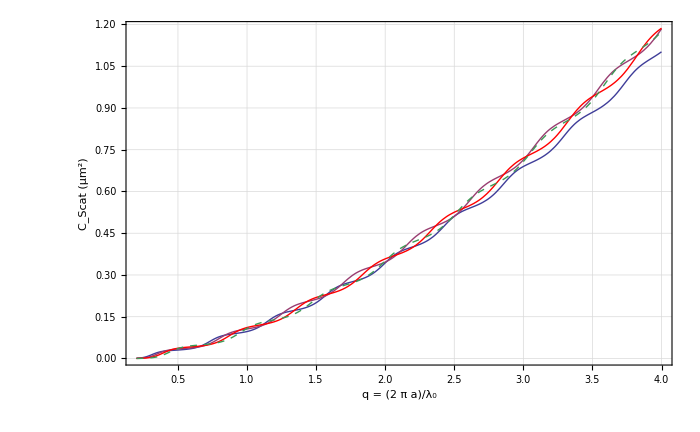

```mathematica
CScatPlotAll = Plot[{CScatα[i Subscript[λ, 0α]/(2π)],CScatβ[i Subscript[λ, 0β]/(2π)],CScatγ[i Subscript[λ, 0γ]/(2π)],CScatδ[i Subscript[λ, 0δ]/(2π)](*,CScatϵ[i Subscript[λ, 0ϵ]/(2π)]*)}, {i,.2,4},  FrameLabel-> {"q = (2  π a)/λ_0", "C_Scat  (μm^2)"},PlotStyle->{Thick,Automatic,Red,Dashed(*,Green*)} ]
```

```mathematica
So by decreasing the wavelegnth (blue)for a given particle size, we increase the size paramater and therefore increase the scattering crossection.
```

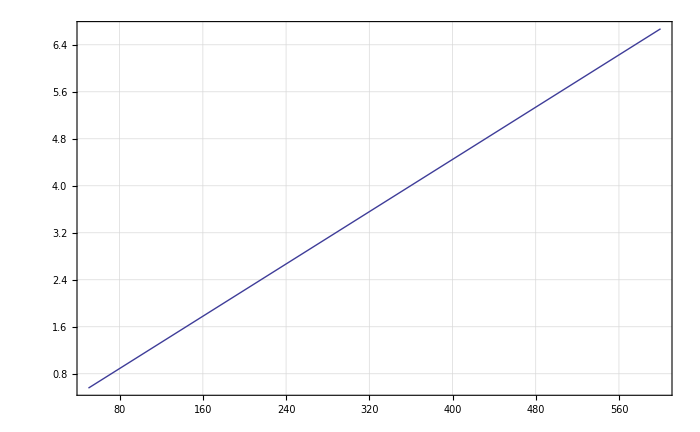

```mathematica
Plot[2*Pi*size/565,{size,50,600}]
```

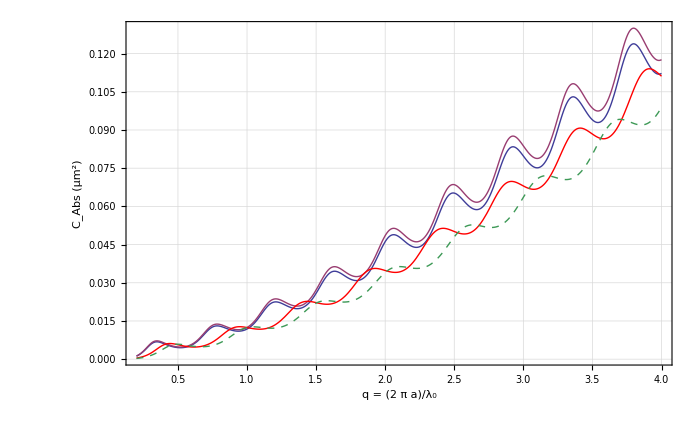

```mathematica
CAbsPlot = Plot[{CAbsα[i Subscript[λ, 0α]/(2π)],CAbsβ[i Subscript[λ, 0β]/(2π)],CAbsγ[i Subscript[λ, 0γ]/(2π)],CAbsδ[i Subscript[λ, 0δ]/(2π)](*CAbsϵ[i Subscript[λ, 0ϵ]/(2π)]*)}, {i, .2, 4}, FrameLabel-> {"q = (2  π a)/λ_0", "C_Abs  (μm^2)"},PlotStyle->{Thick,Automatic,Red,Dashed(*,Green*)}]
```

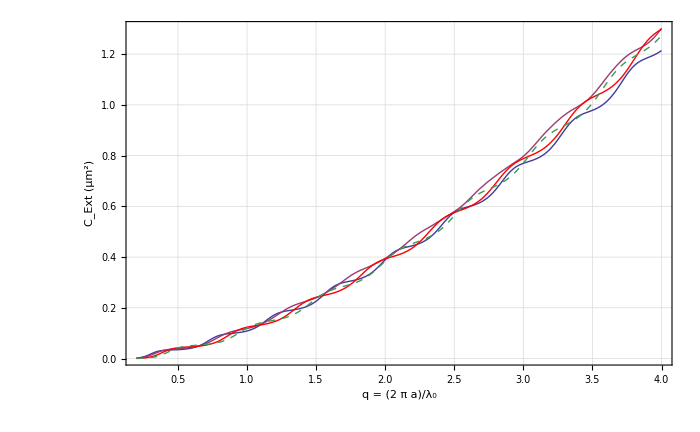

```mathematica
CExtPlot = Plot[{CExtα[i Subscript[λ, 0α]/(2π)],CExtβ[i Subscript[λ, 0β]/(2π)],CExtγ[i Subscript[λ, 0γ]/(2π)],CExtδ[i Subscript[λ, 0δ]/(2π)](*CExtϵ[i Subscript[λ, 0ϵ]/(2π)]*)}, {i, .2, 4}, FrameLabel-> {"q = (2  π a)/λ_0", "C_Ext  (μm^2)"},PlotStyle->{Thick,Automatic,Red,Dashed(*,Green*)}]
```

All three on the same plot.  The first cell creates a legend for the plot.

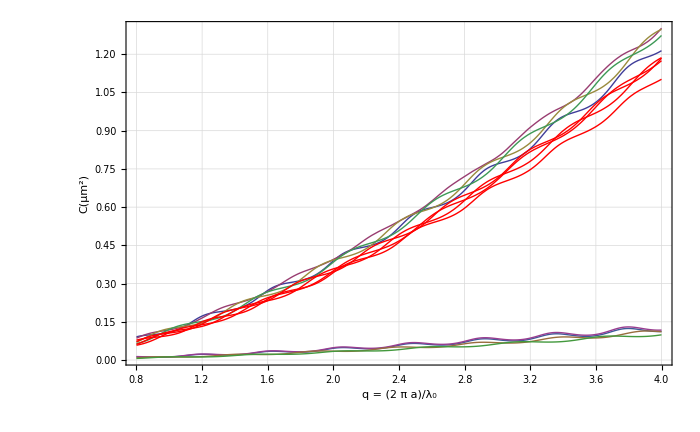

```mathematica
Plot[{CExtα[i Subscript[λ, 0α]/(2π)],CExtβ[i Subscript[λ, 0β]/(2π)],CExtγ[i Subscript[λ, 0γ]/(2π)],CExtδ[i Subscript[λ, 0δ]/(2π)](*CExtϵ[i Subscript[λ, 0ϵ]/(2π)]*),CAbsα[i Subscript[λ, 0α]/(2π)],CAbsβ[i Subscript[λ, 0β]/(2π)],CAbsγ[i Subscript[λ, 0γ]/(2π)],CAbsδ[i Subscript[λ, 0δ]/(2π)](*CAbsϵ[i Subscript[λ, 0ϵ]/(2π)]*),CScatα[i Subscript[λ, 0α]/(2π)],CScatβ[i Subscript[λ, 0β]/(2π)],CScatγ[i Subscript[λ, 0γ]/(2π)],CScatδ[i Subscript[λ, 0δ]/(2π)](*CExtϵ[i Subscript[λ, 0ϵ]/(2π)]*)}, {i, .8,4},PlotStyle->{Thick,Thick, Thick,Thick,(*Thick*)Automatic,Automatic,Automatic,Automatic(*,Automatic*),Red,Red,Red,Red(*Red*)}, FrameLabel-> {"q = (2  π a)/λ_0", "C(μm^2)"}]
```

```mathematica
(* CLegend = {{{RGBColor[1,0,0],"C_scat"},{RGBColor[0,0,1],"C_abs"},{RGBColor[0,0,0],"C_ext"}}, LegendPosition-> {-.55,0.3}, LegendSize-> {0.25,0.25}, LegendShadow-> {0,0}};
```

```mathematica
(* ShowLegend[Show[CScatPlot,CAbsPlot,CExtPlot, DisplayFunction-> Identity], CLegend,DisplayFunction-> $DisplayFunction ];
```

## Calculate and plot the efficiencies

The efficiencies are defined simply as the ratio of the cross sections to the geometrical cross sectional area of the scatterer.

```mathematica
QScatα[a_]:=  CScatα[a]/(π a^2)
QAbsα[a_]:= CAbsα[a]/(π a^2)
QExtα[a_]:=CExtα[a]/(π a^2)
```

```mathematica
QScatβ[a_]:=  CScatβ[a]/(π a^2)
QAbsβ[a_]:= CAbsβ[a]/(π a^2)
QExtβ[a_]:=CExtβ[a]/(π a^2)
```

```mathematica
QScatγ[a_]:=  CScatγ[a]/(π a^2)
QAbsγ[a_]:= CAbsγ[a]/(π a^2)
QExtγ[a_]:=CExtγ[a]/(π a^2)
```

```mathematica
QScatδ[a_]:=  CScatδ[a]/(π a^2)
QAbsδ[a_]:= CAbsδ[a]/(π a^2)
QExtδ[a_]:=CExtδ[a]/(π a^2)
```

```mathematica
QScatϵ[a_]:=  CScatϵ[a]/(π a^2)
QAbsϵ[a_]:= CAbsϵ[a]/(π a^2)
QExtϵ[a_]:=CExtϵ[a]/(π a^2)
```

Print out efficiencies for the default parameters.

```mathematica
Print["Q_Scatα = ",QScatα[Subscript[r, α]]//N,"\nQ_Absα = ",QAbsα[Subscript[r, α]]//N,"\nQ_Extα= ",QExtα[Subscript[r, α]]//N ]
```

Q_Scatα = 4.30262
Q_Absα = 0.670381
Q_Extα= 4.973

```mathematica
Print["Q_Scatβ = ",QScatβ[Subscript[r, β]]//N,"\nQ_Absβ = ",QAbsβ[Subscript[r, β]]//N,"\nQ_Extβ = ",QExtβ[Subscript[r, β]]//N ]
```

Q_Scatβ = 4.06072
Q_Absβ = 0.705634
Q_Extβ = 4.76636

```mathematica
Print["Q_Scatγ = ",QScatγ[Subscript[r, γ]]//N,"\nQ_Absγ = ",QAbsγ[Subscript[r, γ]]//N,"\nQ_Extγ = ",QExtγ[Subscript[r, γ]]//N ]
```

Q_Scatγ = 4.01382
Q_Absγ = 0.390201
Q_Extγ = 4.40402

```mathematica
Print["Q_Scatδ = ",QScatδ[Subscript[r, δ]]//N,"\nQ_Absδ = ",QAbsδ[Subscript[r, δ]]//N,"\nQ_Extδ = ",QExtδ[Subscript[r, δ]]//N ]
```

Q_Scatδ = 4.28268
Q_Absδ = 0.388172
Q_Extδ = 4.67086

```mathematica
Print["Q_Scatϵ = ",QScatϵ[Subscript[r, ϵ]]//N,"\nQ_Absϵ = ",QAbsϵ[Subscript[r, ϵ]]//N,"\nQ_(Ext ϵ) = ",QExtϵ[Subscript[r, ϵ]]//N ]
```

#### Linear plots of size parameter vs. efficiency.

Note that these plots take longer to generate as the size parameter increases.  The multiplicative factor in the argument converts the abscissa variable to q values (rather than radius values).

```mathematica
SetOptions[Plot, Frame-> True, PlotRange-> All, ImageSize-> 700, GridLines-> Automatic,PlotPoints-> 40];
```

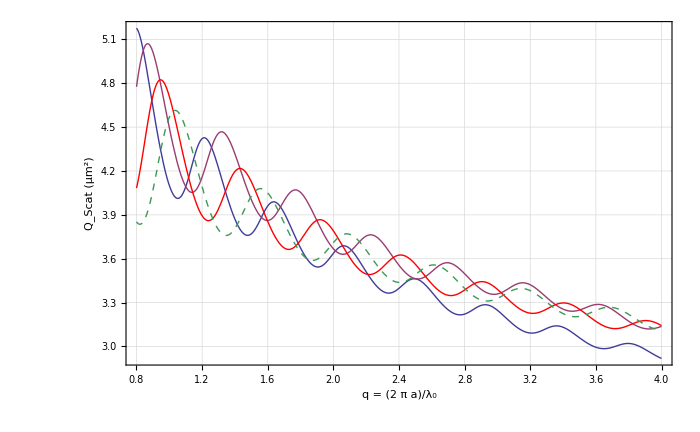

```mathematica
QScatPlot = Plot[{QScatα[i Subscript[λ, 0α]/(2π)],QScatβ[i Subscript[λ, 0β]/(2π)],QScatγ[i Subscript[λ, 0γ]/(2π)],QScatδ[i Subscript[λ, 0δ]/(2π)](*,QScatϵ[i Subscript[λ, 0ϵ]/(2π)]*)}, {i,.8, 4},PlotStyle->{Thick,Automatic,Red,Dashed(*,Green*)},  FrameLabel-> {"q = (2  π a)/λ_0", "Q_Scat  (μm^2)"}]
```

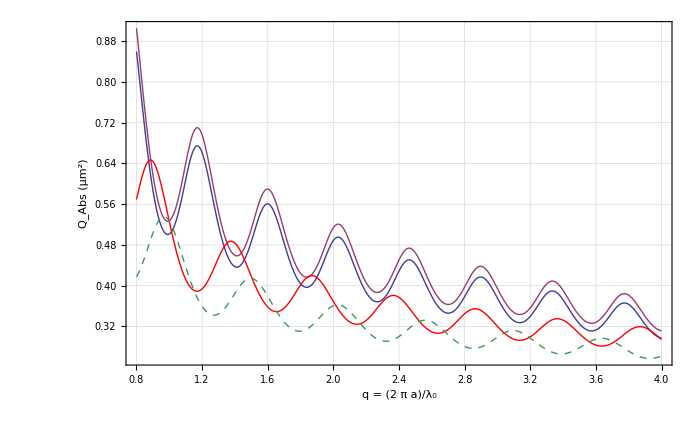

```mathematica
QAbsPlot = Plot[{QAbsα[i Subscript[λ, 0α]/(2π)],QAbsβ[i Subscript[λ, 0β]/(2π)],QAbsγ[i Subscript[λ, 0γ]/(2π)],QAbsδ[i Subscript[λ, 0δ]/(2π)](*,QScatϵ[i Subscript[λ, 0ϵ]/(2π)]*)}, {i,.8, 4},PlotStyle->{Thick,Automatic,Red,Dashed(*,Green*)},  FrameLabel-> {"q = (2  π a)/λ_0", "Q_Abs  (μm^2)"}]
```

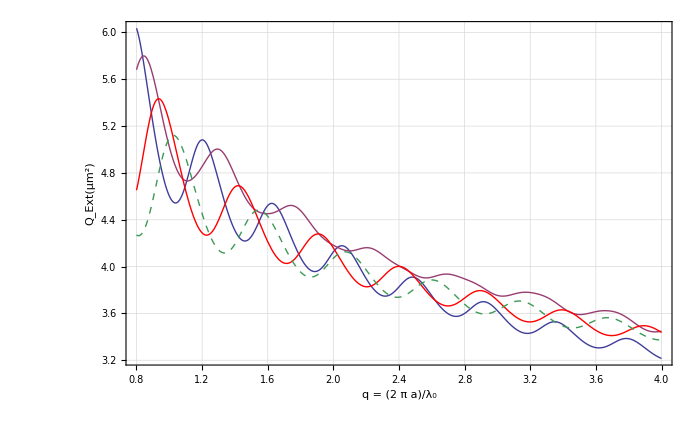

```mathematica
QExtPlot =Plot[{QExtα[i Subscript[λ, 0α]/(2π)],QExtβ[i Subscript[λ, 0β]/(2π)],QExtγ[i Subscript[λ, 0γ]/(2π)],QExtδ[i Subscript[λ, 0δ]/(2π)](*,QScatϵ[i Subscript[λ, 0ϵ]/(2π)]*)}, {i,.8, 4},PlotStyle->{Thick,Automatic,Red,Dashed(*,Green*)},  FrameLabel-> {"q = (2  π a)/λ_0", "Q_Ext(μm^2)"}]
```

All three on the same plot.  The first cell creates a legend for the plot.

```mathematica
(* QLegend = {{{RGBColor[1,0,0],"Q_scat"},{RGBColor[0,0,1],"Q_abs"},{RGBColor[0,0,0],"Q_ext"}}, LegendPosition-> {-.55,0.3}, LegendSize-> {0.25,0.25}, LegendShadow-> {0,0}};
```

```mathematica
(* ShowLegend[Show[QScatPlot,QAbsPlot,QExtPlot, PlotRange-> All,DisplayFunction-> Identity], QLegend,DisplayFunction-> $DisplayFunction ];
```

#### Log-linear plots of size parameter vs. efficiency.

These plots are useful when plotting over a large range of q values, but take longer to generate as the size parameter increases.  The multiplicative factor in the argument converts the abscissa variable to q values (rather than radius values).

All three on the same plot.  The first cell creates a legend for the plot.

```mathematica
QLegend = {{{RGBColor[1,0,0],"Q_scat"},{RGBColor[0,0,1],"Q_abs"},{RGBColor[0,0,0],"Q_ext"}}, LegendPosition-> {-.55,0.3}, LegendSize-> {0.25,0.25}, LegendShadow-> {0,0}};
```

```mathematica
ShowLegend[Show[QScatLogPlot,QAbsLogPlot,QExtLogPlot, PlotRange-> All,DisplayFunction-> Identity], QLegend,DisplayFunction-> $DisplayFunction ];
```

## Calculate and plot the asymmetry factor

The equation for the asymmetry factor comes from Fu and Sun (Applied Optics, Vol. 40, No. 9, 2001, pp. 1354-1361).

```mathematica
gα[a_] := (2∑_(l=1)^LastTermα[a] ((l(l+2))/(l + 1) Re[(anα[l,a]*  SuperStar[anα[l+1,a]]+ bnα[l,a]*SuperStar[bnα[l+1,a]])] + (2l+1)/(l(l + 1)) Re[(anα[l,a] *SuperStar[bnα[l,a]])]))/(∑_(l=1)^LastTermα[a] (2l+1)((Abs[anα[l,a]])^2 + (Abs[bnα[l,a]])^2))
```

```mathematica
gβ[a_] := (2∑_(l=1)^LastTermβ[a] ((l(l+2))/(l + 1) Re[(anβ[l,a]*  SuperStar[anβ[l+1,a]]+ bnβ[l,a]*SuperStar[bnβ[l+1,a]])] + (2l+1)/(l(l + 1)) Re[(anβ[l,a] *SuperStar[bnβ[l,a]])]))/(∑_(l=1)^LastTermβ[a] (2l+1)((Abs[anβ[l,a]])^2 + (Abs[bnβ[l,a]])^2))
```

```mathematica
gγ[a_] := (2∑_(l=1)^LastTermγ[a] ((l(l+2))/(l + 1) Re[(anγ[l,a]*  SuperStar[anγ[l+1,a]]+ bnγ[l,a]*SuperStar[bnγ[l+1,a]])] + (2l+1)/(l(l + 1)) Re[(anγ[l,a] *SuperStar[bnγ[l,a]])]))/(∑_(l=1)^LastTermγ[a] (2l+1)((Abs[anγ[l,a]])^2 + (Abs[bnγ[l,a]])^2))
```

```mathematica
gδ[a_] := (2∑_(l=1)^LastTermδ[a] ((l(l+2))/(l + 1) Re[(anδ[l,a]*  SuperStar[anδ[l+1,a]]+ bnδ[l,a]*SuperStar[bnδ[l+1,a]])] + (2l+1)/(l(l + 1)) Re[(anδ[l,a] *SuperStar[bnδ[l,a]])]))/(∑_(l=1)^LastTermδ[a] (2l+1)((Abs[anδ[l,a]])^2 + (Abs[bnδ[l,a]])^2))
```

```mathematica
gϵ[a_] := (2∑_(l=1)^LastTermϵ[a] ((l(l+2))/(l + 1) Re[(anϵ[l,a]*  SuperStar[anϵ[l+1,a]]+ bnϵ[l,a]*SuperStar[bnϵ[l+1,a]])] + (2l+1)/(l(l + 1)) Re[(anϵ[l,a] *SuperStar[bnϵ[l,a]])]))/(∑_(l=1)^LastTermϵ[a] (2l+1)((Abs[anϵ[l,a]])^2 + (Abs[bnϵ[l,a]])^2))
```

```mathematica
StringJoin["The anisotropy value is g = ", ToString[gα[Subscript[r, α]]//N]]
```

The anisotropy value is g = 0.471659

```mathematica
StringJoin["The anisotropy value is g = ", ToString[gβ[Subscript[r, β]]//N]]
```

The anisotropy value is g = 0.413752

```mathematica
StringJoin["The anisotropy value is g = ", ToString[gγ[Subscript[r, γ]]//N]]
```

The anisotropy value is g = 0.382319

```mathematica
StringJoin["The anisotropy value is g = ", ToString[gδ[Subscript[r, δ]]//N]]
```

The anisotropy value is g = 0.396522

```mathematica
StringJoin["The anisotropy value is g = ", ToString[gϵ[Subscript[r, ϵ]]//N]]
```

The anisotropy value is g =           -11
4.98577 10

#### Create plot of size parameter vs. asymmetry factor.

```mathematica
The assummetry factor denotes the symmetry of the phase function and related whether forward scattering or back scattering is dominant (greater than 1 is forward, less than 1 is backscattering).
```

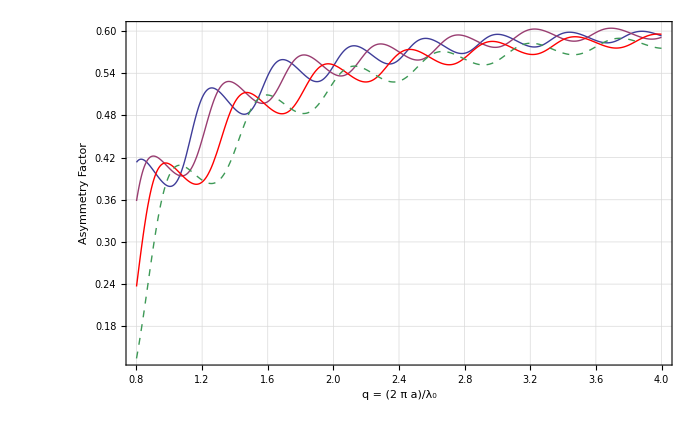

```mathematica
gPlot = Plot[{gα[i Subscript[λ, 0α]/(2π)],gβ[i Subscript[λ, 0β]/(2π)],gγ[i Subscript[λ, 0γ]/(2π)],gδ[i Subscript[λ, 0δ]/(2π)](*gα[i Subscript[λ, 0α]/(2π)]*)}, {i,.8, 4}, Frame-> True, PlotRange-> All, ImageSize-> 700, PlotStyle->{Thick,Automatic,Red,Dashed(*,Green*)}, GridLines-> Automatic, FrameLabel-> {"q = (2  π a)/λ_0", "Asymmetry Factor"}]
```

## Calculate and plot the albedo

The albedo is simply the ratio of the scattering to extinction cross sections.

```mathematica
albedoα[a_] := CScatα[a]/CExtα[a];
StringJoin["The albedo is ", ToString[albedoα[Subscript[r, α]]//N]]
```

The albedo is 0.865196

```mathematica
albedoβ[a_] := CScatβ[a]/CExtβ[a];
StringJoin["The albedo is ", ToString[albedoβ[Subscript[r, β]]//N]]
```

The albedo is 0.851955

```mathematica
albedoγ[a_] := CScatγ[a]/CExtγ[a];
StringJoin["The albedo is ", ToString[albedoγ[Subscript[r, γ]]//N]]
```

The albedo is 0.911399

```mathematica
albedoδ[a_] := CScatδ[a]/CExtδ[a];
StringJoin["The albedo is ", ToString[albedoδ[Subscript[r, δ]]//N]]
```

The albedo is 0.916895

```mathematica
albedoϵ[a_] := CScatϵ[a]/CExtϵ[a];
StringJoin["The albedo is ", ToString[albedoϵ[Subscript[r, ϵ]]//N]]
```

```mathematica
Manipulate[N[albedo[i*Subscript[λ, 0]/(2π)],3],{i,1,6}]
```

#### Create plot of albedo vs. size parameter.

```mathematica
(* SetOptions[LogLinearPlot, Frame-> True, PlotRange-> All, ImageSize-> 700, GridLines-> Automatic,PlotPoints-> 40];
```

```mathematica
(* In the next section of code, i is the size paramater.  *)
```

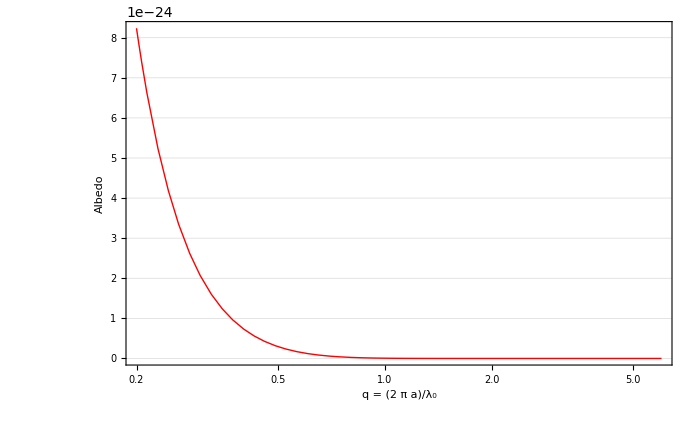

```mathematica
AlbedoPlot = LogLinearPlot[{albedoα[i Subscript[λ, 0α]/(2π)],albedoβ[i Subscript[λ, 0β]/(2π)],albedoγ[i Subscript[λ, 0γ]/(2π)],albedoδ[i (Subscript[λ, 0] δ)/(2π)](*,albedo[i Subscript[λ, 0]/(2π)]*)}, {i,.2, 6}, Frame-> True, PlotRange-> All, ImageSize-> 700, PlotStyle->{Thick,Automatic,Red,Dashed(*,Green*)}, GridLines-> Automatic, FrameLabel-> {"q = (2  π a)/λ_0", "Albedo"}]
```

## Calculate and plot the scattering phase functions

Next, we construct the formulae for intensity as a function of angular position for incident radiation polarized in either of the two linear orthogonal polarization states.  Begin by defining the amplitude matrix elements, S1(r, θ) and S2(r, θ) which simplify the form of the resulting phase function equations a little

```mathematica
S1[a_,θ_]:= ∑_(l=1)^LastTerm[a] ((2 l+1)/(l (l+1)))(an[l,a]pi[l,θ]+bn[l,a]  τ[l,θ]);
S2[a_,θ_]:= ∑_(l=1)^LastTerm[a] ((2 l+1)/(l (l+1)))( an[l,a] τ[l,θ]+bn[l,a]  pi[l,θ] );
```

```mathematica
(* Added by Guy *)
```

```mathematica
(* Look at the phase difference between the scattered beams A and B
```

```mathematica
(* N[(Re[S1[a,θ]]Im[S2[a,θ]]-Re[S2[a,θ]]Im[S1[a, θ]])/(Re[S1[a,θ]]Re[S2[a,θ]]+Im[S1[a,θ]]Im[S2[a, θ]]),3]
```

```mathematica
(*  θ1=ContourPlot[N[(Re[S1[a, θ]]Im[S2[a, θ]]-Re[S2[a, θ]]Im[S1[a, θ]])/(Re[S1[a, θ]]Re[S2[a, θ]]+Im[S1[a, θ]]Im[S2[a, θ]]),3],{a,0,1},{θ,0,.9π}]
```

```mathematica
Look at the scattering amplitude in the forward direction:
```

```mathematica
Cextfor=(Subscript[λ, 0]^2/Pi)*Re[S[1,0]]
```

(296527078849 Re[S[1,0]])/(1000000000000 π)

Here are the phase function equations.  The normalization factor (to insure ∫P(cos(θ))ⅆΩ =  1) is sometime used in the literature (e.g., Fu and Sun) and sometimes neglected (e.g Bohren and Huffman).  Therefore, two separate functions for the unpolarized scattering phase function are created and either one may be used.

```mathematica
Iperp[a_, θ_]:= (Abs[S1[a,θ]])^2;

Ipar[a_, θ_]:= (Abs[S2[a,θ]])^2;

Iunpol[a_, θ_]:= (Iperp[a, θ] + Ipar[a, θ])/2;

Norma[a_]:=∑_(l=1)^LastTerm[a] 2(l + 1)((Abs[an[l,a]])^2 + (Abs[bn[l,a]])^2)

IunpolNorm[a_, θ_]:= (Iperp[a, θ] + Ipar[a, θ])/Norma[a];
```

### Create plots of the phase functions.

#### Log-linear plots of scattered intensity vs. angle.

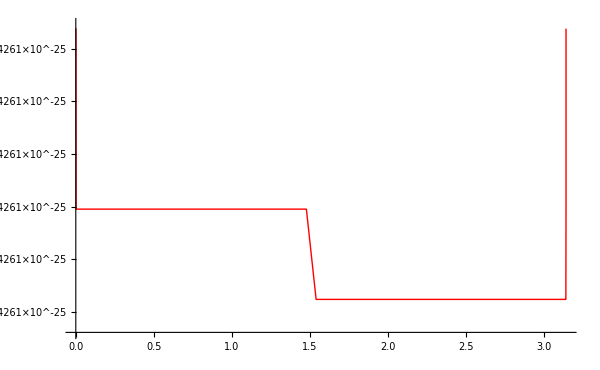

```mathematica
IPerpPlot = LogPlot[Evaluate[Iperp[r, θ]], {θ, 0, π},  PlotStyle-> RGBColor[1,0,0],  FrameLabel-> {"θ (deg)", "I_perp Phase Function"}]
```

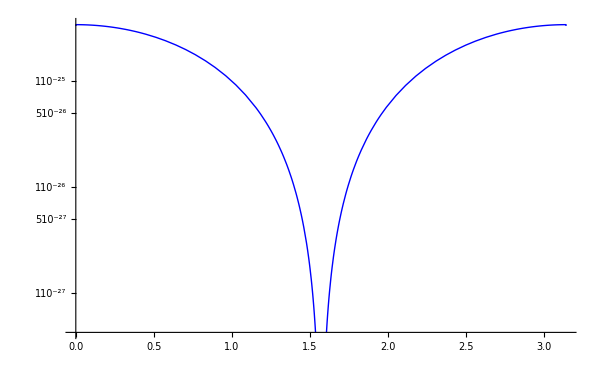

```mathematica
IParPlot = LogPlot[Evaluate[Ipar[r, θ]], {θ, 0, π},  PlotStyle-> RGBColor[0,0,1],  FrameLabel-> {"θ (deg)", "I_par Phase Function"}]
```

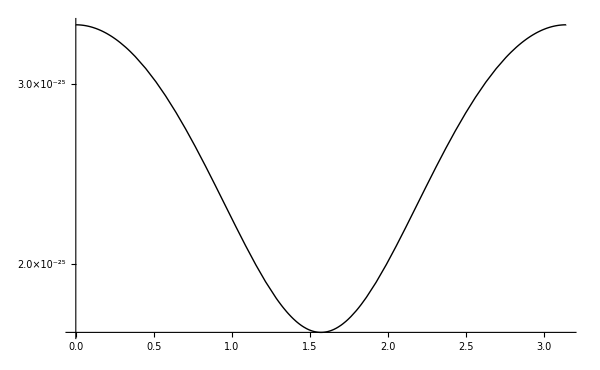

```mathematica
IUnpolPlot = LogPlot[Evaluate[Iunpol[r, θ]], {θ, 0, π},  PlotStyle-> RGBColor[0,0,0],  FrameLabel-> {"θ (deg)", "I_unpol Phase Function"}]
```

All three on the same plot.  The first expression creates a legend for the plot.

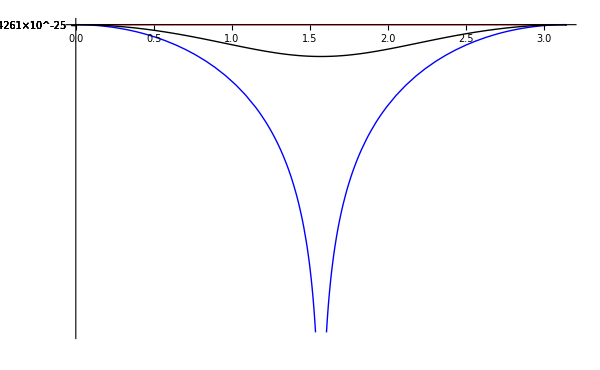

```mathematica
ILegend = {{{RGBColor[1,0,0],"I_perp"},{RGBColor[0,0,1],"I_par"},{RGBColor[0,0,0],"I_unpol"}}, LegendPosition-> {.5,0.3}, LegendSize-> {0.25,0.25}, LegendShadow-> {0,0}};
Show[IPerpPlot,IParPlot,IUnpolPlot, PlotRange-> All,DisplayFunction-> Identity, FrameLabel->{"θ (deg)", "Phase Functions"} ]
```

#### Polar plots of scattered intensity vs. angle.

Begin by defining some additional graphics to make the polar plots look good.  Note that when we normalize the phase functions to the peak value (which is the same for all polarization states), the maximum corresponds to θ = 0.   The PlotMax variable in the next cell permits the user to change the plot range, permitting "zooming" to look at the fine structure close to the particle.

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
MySpokes = Table[Graphics[Line[{{0,0},{Cos[θ Degree], Sin[θ Degree]}}]], {θ, 0, 345, 30}];
MyRings = Graphics[Table[{Dashing[{0.01,0.01}],Circle[{0,0},i]},{i,0,1,0.1}]];
NormFactor = NLimit[Iperp[r,ϕ], ϕ-> 0.01, WorkingPrecision-> 20,Terms->6];
```

```mathematica
N[NormFactor,3]
```

3.4261×10^-25

```mathematica
PlotMax = 1.025;
```

```mathematica
SetOptions[PolarPlot, Frame-> True, PlotRange-> All, ImageSize-> 500,  PlotPoints->30,  AspectRatio-> 1, FrameTicks-> None,PlotRange-> {{-PlotMax,PlotMax}, {-PlotMax,PlotMax}}, DisplayFunction-> Identity ];
```

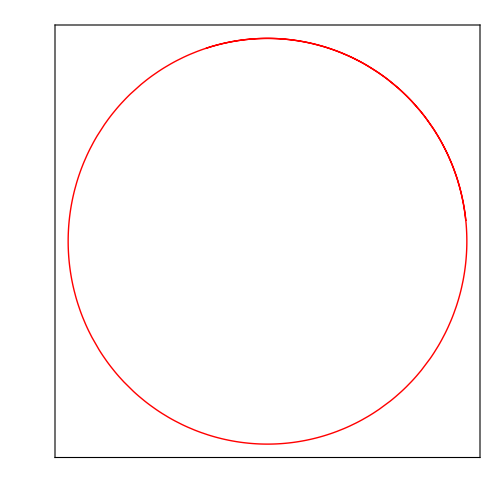

```mathematica
IPolarPerp = PolarPlot[Evaluate[Iperp[r,θ]/NormFactor], {θ,.1,2.6*Pi},PlotStyle-> RGBColor[1,0,0]]
```

I_parvs. θ

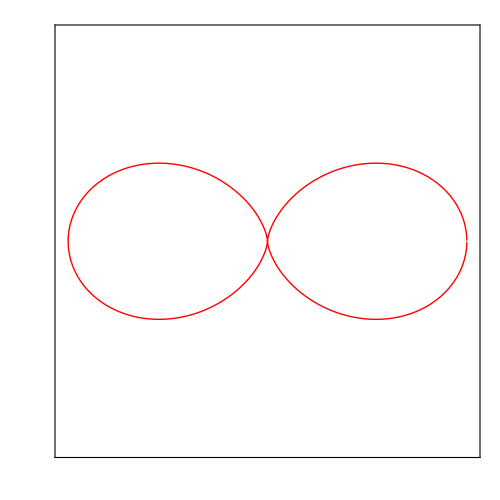

```mathematica
IPolarPar = PolarPlot[Evaluate[Ipar[r,θ]/NormFactor], {θ, π*.001,1.999π},PlotStyle-> RGBColor[1,0,0]]
```

I_unpolvs. θ

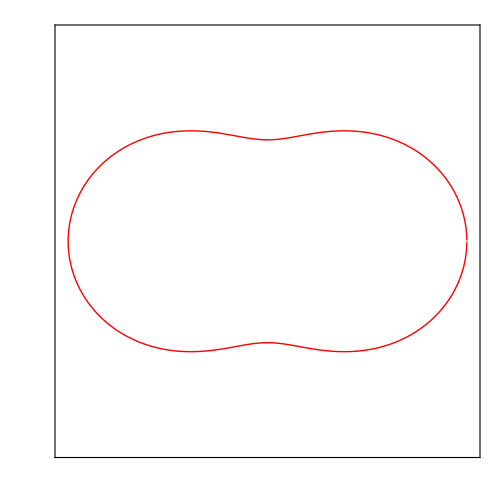

```mathematica
IPolarUnpol = PolarPlot[Evaluate[Iunpol[r,θ]/NormFactor], {θ, π*.001,1.999π},PlotStyle-> RGBColor[1,0,0]]
```

All three on the same plot.  The first expression creates a legend for the plot.

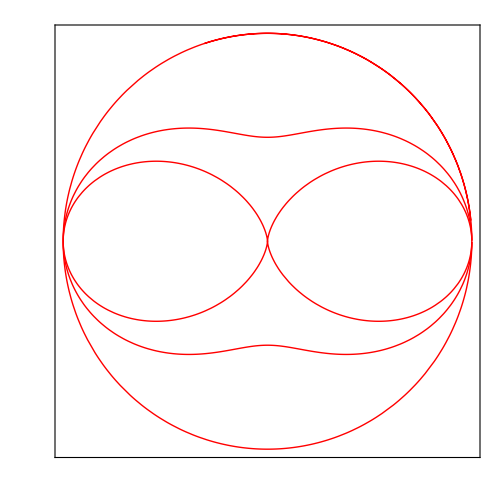

```mathematica
IPolarLegend = {{{RGBColor[1,0,0],"I_perp"},{RGBColor[0,0,1],"I_par"},{RGBColor[0,0,0],"I_unpol"}}, LegendPosition-> {.63,.6}, LegendSize-> {0.25,0.25}, LegendShadow-> {0,0}};
Show[IPolarPerp,IPolarPar,IPolarUnpol, PlotRange-> All,DisplayFunction-> Identity, FrameLabel->{None,None,"Normalized Phase Functions", None} ]
```

#### Log-polar plots of scattered intensity vs. angle.

Begin by defining a few labels and some additional graphics to make the polar plots look good.  Note that I normalize the phase functions to the peak value (which is the same for all polarization states and occurs in the forward direction where θ = 0).

```mathematica
MySpokes = Table[Graphics[Line[{{0,0},{Cos[θ Degree], Sin[θ Degree]}}]], {θ, 0, 345, 30}];
LogRings = Graphics[Table[{Dashing[{0.01,0.01}],Circle[{0,0},Log[10,i]]},{i,1.105171,10,1.1105171}]];
LogNormFactor = NLimit[Log[10,Iperp[r, ϕ]], ϕ-> 0.0, WorkingPrecision-> 20, Terms ->  6];
```

NLimit::noise: Cannot recognize a limiting value.  This may be due to  noise resulting from roundoff errors in which case higher WorkingPrecision,  fewer Terms, or a different Scale might help.

```mathematica
SetOptions[PolarPlot, Frame-> True, PlotRange-> All, ImageSize-> 500,  PlotPoints->30,  AspectRatio-> 1, FrameTicks-> None, Ticks-> None, DisplayFunction-> Identity ];
```

```mathematica
PerpMinValue = FindMinimum[Iperp[r, θ]/NormFactor, {θ,  .75π,π/2}]⟦2,1,2⟧;
ParMinValue = FindMinimum[Ipar[r, θ]/NormFactor, {θ,  .75π,π/2}]⟦2,1,2⟧;
UnpolMinValue = FindMinimum[Iunpol[r, θ]/NormFactor, {θ,  .75π,π/2}]⟦2,1,2⟧;
```

I_perpvs. θ

```mathematica
Timing[ILogPolarPerp = PolarPlot[Evaluate[Log[10,Iperp[r, θ]  + (1-Iperp[r, PerpMinValue])]/LogNormFactor], {θ, 0, 2π}, PlotStyle-> RGBColor[1,0,0], PlotRange-> {{-1,1}, {-1,1}}];]
```

General::ivar: 3.16775 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

NLimit::noise: Cannot recognize a limiting value.  This may be due to  noise resulting from roundoff errors in which case higher WorkingPrecision,  fewer Terms, or a different Scale might help.

General::stop: Further output of NLimit :: noise will be suppressed during this calculation.

Power::infy: Infinite expression 1/√0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity encountered.

Infinity::indet: Indeterminate expression (0.  + 0.\ ⅈ)\ ComplexInfinity
 encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

{0.983,Null}

```mathematica
Show[ILogPolarPerp, MySpokes, LogRings,DisplayFunction-> $DisplayFunction];
```

I_parvs. θ

```mathematica
Timing[ILogPolarPar = PolarPlot[Evaluate[Log[10,Ipar[r, θ]  + (1-Ipar[r, ParMinValue])]/LogNormFactor], {θ, 0, 2π},  PlotStyle-> RGBColor[0,0,1], PlotRange-> {{-1,1}, {-1,1}}];]
```

General::ivar: 1.5708 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

NLimit::noise: Cannot recognize a limiting value.  This may be due to  noise resulting from roundoff errors in which case higher WorkingPrecision,  fewer Terms, or a different Scale might help.

General::stop: Further output of NLimit :: noise will be suppressed during this calculation.

Power::infy: Infinite expression 1/√0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity encountered.

Infinity::indet: Indeterminate expression (0.  + 0.\ ⅈ)\ ComplexInfinity
 encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

{0.983,Null}

```mathematica
Show[ILogPolarPar,  MySpokes, LogRings,DisplayFunction-> $DisplayFunction];
```

I_unpolvs. θ

```mathematica
Timing[ILogPolarUnPol = PolarPlot[Evaluate[Log[10,Iunpol[r, θ]  + (1-Iunpol[r, UnpolMinValue])]/LogNormFactor], {θ, 0, 2π}, PlotStyle-> RGBColor[0,0,0], PlotRange-> {{-1,1}, {-1,1}}];]
```

General::ivar: 1.5708 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

NLimit::noise: Cannot recognize a limiting value.  This may be due to  noise resulting from roundoff errors in which case higher WorkingPrecision,  fewer Terms, or a different Scale might help.

General::stop: Further output of NLimit :: noise will be suppressed during this calculation.

Power::infy: Infinite expression 1/√0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity + ComplexInfinity encountered.

Infinity::indet: Indeterminate expression (0.  + 0.\ ⅈ)\ ComplexInfinity
 encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

{1.108,Null}

```mathematica
Show[ILogPolarUnPol, MySpokes, LogRings,DisplayFunction-> $DisplayFunction];
```

All three on the same plot.  The first expression creates a legend for the plot.

```mathematica
ILogPolarLegend = {{{RGBColor[1,0,0],"I_perp"},{RGBColor[0,0,1],"I_par"},{RGBColor[0,0,0],"I_unpol"}}, LegendPosition-> {.63,.6}, LegendSize-> {0.25,0.25}, LegendShadow-> {0,0}};
ShowLegend[Show[ILogPolarPerp,ILogPolarPar,ILogPolarUnPol,MySpokes, LogRings, PlotRange-> All,DisplayFunction-> Identity, FrameLabel->{None,None,"Log Phase Functions", None} ], ILogPolarLegend,DisplayFunction-> $DisplayFunction ];
```

## Calculate and plot the polarization ratio for unpolarized incident light

Note that this definition applies to an unpolarized incident beam.

```mathematica
PolRatio[a_, θ_]:=(Iperp[a, θ] - Ipar[a, θ])/(Iperp[a, θ] + Ipar[a, θ]);
```

Plot of the polarization ratio vs. angle

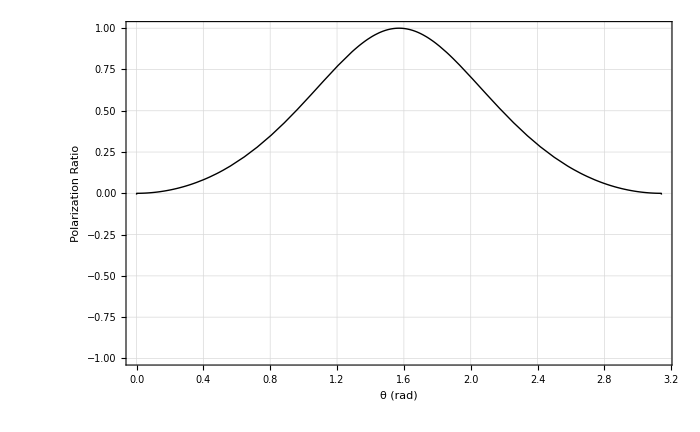

```mathematica
PolRatioPlot = Plot[Evaluate[PolRatio[r, θ]], {θ, 0, π}, Frame-> True, PlotRange-> {-1,1}, ImageSize-> 700, PlotStyle-> RGBColor[0,0,0], GridLines-> Automatic, FrameLabel-> {"θ (rad)","Polarization Ratio", "Polarization Ratio = I_perp/I_perp", None}]
```

## 3-D Plots

Here are some 3 dimensional plots of the phase functions.   These plots are handy because they reveal the asymmetry of the surfaces when a completely polarized input plane wave is incident.  The unpolarized case degenerates into a symmetric surface (about the optical axis).  This first few cells contain the amplitude matrix and intensity functions and were actually defined earlier for the 2D plots.  They are included here in case the cells for the 2D plots have not been evaluated.  Also included are the two possible normalizing factors for the unpolarized case (see above).

```mathematica
S1[a_, θ_]:= ∑_(l=1)^LastTerm[a] ((2 l+1)/(l (l+1)))(an[l,a]*pi[l,θ]+bn[l,a]*τ[l,θ])
S2[a_, θ_]:= ∑_(l=1)^LastTerm[a] ((2 l+1)/(l (l+1)))( an[l, a]*τ[l,θ]+bn[l,a]*pi[l,θ] )
```

```mathematica
S1[a_,θ_]:=( ∑_(l=1)^LastTerm[a] ((2 l+1)/(l (l+1)))(an[l,a]*pi[l,θ]+bn[l,a]* τ[l,θ1]))/.θ1-> θ;
S2[a_,θ_] :=( ∑_(l=1)^LastTerm[a] ((2 l+1)/(l (l+1)))( an[l,a]* τ[l,θ1]+bn[l,a]*pi[l,θ] ))/.θ1-> θ;
AmpMatrix[a_,θ_]:={{S2[a,θ],0},{0,S1[a,θ]}}
```

These are the 3D extensions of the intensity functions.  The ϕ dependence is on sin^2(ϕ) for the perpendicular case and on cos^2(ϕ) for the parallel case.

```mathematica
Iperp3D[a_,θ_,ϕ_]:= (Abs[S1[a,θ]] Sin[ϕ])^2
Ipar3D[a_,θ_,ϕ_]:= (Abs[S2[a,θ]] Cos[ϕ])^2
Iunpol3D[a_,θ_,ϕ_]:= (Iperp3D[a,θ,ϕ] + Ipar3D[a,θ,ϕ])/2
Norma2[a_]:=∑_(l=1)^LastTerm[a] 2(l + 1)((Abs[an[l,a]])^2 + (Abs[bn[l,a]])^2)
IunpolNorm3D[a_, θ_, ϕ_]:= (Iperp3D[a, θ, ϕ] + Ipar3D[a, θ, ϕ])/Norma2[a]
```

```mathematica
By integrating the scattering function for the unpolarized case, I can determine the total amount of scattered light within a certain angular region with respect to the particle.  Of particular region is the fraction of the scattered light that is inside the exit code.  This assumes that the light is normal to the interface and approaching a particle.
```

```mathematica
This can then be modified to deal with light approaching the particle from an angle and therefor the criticale angles will change.
```

```mathematica
NIntegrate[NIntegrate[IunpolNorm3D[r,θ,ϕ],{ θ,0,2Pi}],{ ϕ,0,Pi/20}]
```

NIntegrate::inumr: The integrand 1.64181×10^24\ (Abs[3/2\ Plus[« 2 »] + 5/6\ Plus[« 2 »] + 7/12\ Plus[« 2 »] + 9/20\ Plus[« 2 »] + « 5 » + 21/110\ Plus[« 2 »] + 23/132\ Plus[« 2 »] + 25/156\ Plus[« 2 »] + 27/182\ Plus[« 2 »]]^2\ Cos[ϕ]^2 + Abs[3/2\ Plus[« 2 »] + 5/6\ Plus[« 2 »] + « 9 » + 25/156\ Plus[« 2 »] + 27/182\ Plus[« 2 »]]^2\ Sin[ϕ]^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

0.279854

```mathematica
NIntegrate[NIntegrate[IunpolNorm3D[r,θ,ϕ],{ θ,0,2Pi}],{ ϕ,0,π/2}]
```

NIntegrate::inumr: The integrand 1.64181×10^24\ (Abs[3/2\ Plus[« 2 »] + 5/6\ Plus[« 2 »] + 7/12\ Plus[« 2 »] + 9/20\ Plus[« 2 »] + « 5 » + 21/110\ Plus[« 2 »] + 23/132\ Plus[« 2 »] + 25/156\ Plus[« 2 »] + 27/182\ Plus[« 2 »]]^2\ Cos[ϕ]^2 + Abs[3/2\ Plus[« 2 »] + 5/6\ Plus[« 2 »] + « 9 » + 25/156\ Plus[« 2 »] + 27/182\ Plus[« 2 »]]^2\ Sin[ϕ]^2) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 6.28319}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

$Aborted

Values required to center the particle at the origin.  Note there is no need to consider the ϕ dimension here so I use the 2D equations which evaluate more quickly.

```mathematica
Needs["NumericalCalculus'"]
```

```mathematica
NormFactor = NLimit[Iperp[r, ϕ], ϕ-> 0.01, WorkingPrecision-> 20, Terms ->  6]
LogNormFactor = NLimit[Log[10,Iperp[r, ϕ]], ϕ-> 0.01, WorkingPrecision-> 20, Terms ->  6]
```

35.7233

1.55296

```mathematica
PerpMinValue = FindMinimum[(Abs[S1[r,θ]])^2/NormFactor, {θ,  0.01,π}]
ParMinValue = FindMinimum[(Abs[S2[r,θ]])^2/NormFactor, {θ,  0.01,π}]
UnpolMinValue = FindMinimum[(Iperp[r, θ] + Ipar[r, θ])/(2 NormFactor), {θ,  0.01,π}]
```

{0.022296,{θ→1.63722}}

{0.0530492,{θ→0.790118}}

{0.0195209,{θ→1.84176}}

```mathematica
PerpMinValue=.022296;
ParMinValue=.0530492;
UnpolMinValue=.0195209;
```

#### Plot the phase functions.

Start out by setting up the graphics.

```mathematica
SetOptions[SphericalPlot3D,BoxRatios->{1,1,1}, AspectRatio->1, Axes->True, PlotPoints->40,ViewPoint->{-15,0,0}, Boxed->False,ViewVertical->{0,1,0}, PlotRange-> All , LightSources->{{{1,0,1}, RGBColor[1,0,0]}, {{1,1,1},RGBColor[0,1,0]},{{0,1,1},RGBColor[0,0,1]},{{-1,0,-1},RGBColor[1,0,0]},{{-1,-1,-1},RGBColor[0,1,0]},{{0,-1,-1} ,RGBColor[0,0,1] }}];
```

SetOptions::optnf: LightSources is not a known option for SphericalPlot3D.

These next few cells can take long when the sampling is fine (i.e., when the PlotPoints value is set high).  Have patience.  Also, these plots will crash for angular values of exactly nπ (n = 0, ±1, ±2, ...).  I get around this by choosing plot ranges that only approach these values, rather than redefining the functions as their limiting values for all of these possible cases.  The latter approach, although more thorough, tends to extend the computation time substantially and adequate approximations can be made using the former by adding more digits (zeros or nines) to the arguments.  There are two plots for each phase function, a side view and an end view, and these are helpful in examining the asymmetry of the surfaces.  Start with the perpendicular phase function.

```mathematica
FullSimplify[S1[r,θ]]
```

(1.+0. ⅈ) ((-0.59407+0.434866 ⅈ)-(0.709436+0.270593 ⅈ) Cos[θ]+(0.27407-0.369542 ⅈ) Cos[2 θ]+(0.705927+0.268373 ⅈ) Cos[3 θ]+(0.319869-0.0660574 ⅈ) Cos[4 θ]+(0.0035035+0.00217887 ⅈ) Cos[5 θ]+(0.00013013+0.000731199 ⅈ) Cos[6 θ]+(5.11374×10^-6+0.0000410624 ⅈ) Cos[7 θ]+(1.50008×10^-7+1.36793×10^-6 ⅈ) Cos[8 θ]+(3.28754×10^-9+3.18513×10^-8 ⅈ) Cos[9 θ]+(5.55643×10^-11+5.56843×10^-10 ⅈ) Cos[10 θ]+(7.4577×10^-13+7.63291×10^-12 ⅈ) Cos[11 θ]+(8.14381×10^-15+8.45497×10^-14 ⅈ) Cos[12 θ]+(7.38063×10^-17+7.74215×10^-16 ⅈ) Cos[13 θ]+(5.64363×10^-19+5.96687×10^-18 ⅈ) Cos[14 θ]+(3.48397×10^-21+4.21169×10^-20 ⅈ) Cos[15 θ]) Csc[θ]^3 √(Sin[θ]^2)

```mathematica
FullSimplify[S2[r,θ]]
```

(1.+0. ⅈ) ((0.265097-0.24917 ⅈ)+(0.122181-0.178643 ⅈ) Cos[θ]-(0.823269-0.101959 ⅈ) Cos[2 θ]-(0.571756-0.422855 ⅈ) Cos[3 θ]+(0.553474+0.175246 ⅈ) Cos[4 θ]+(0.449443-0.242947 ⅈ) Cos[5 θ]+(0.00469386-0.0279918 ⅈ) Cos[6 θ]+(0.00013099-0.0012645 ⅈ) Cos[7 θ]+(3.9724×10^-6-0.0000439689 ⅈ) Cos[8 θ]+(9.65208×10^-8-1.14612×10^-6 ⅈ) Cos[9 θ]+(1.84577×10^-9-2.29143×10^-8 ⅈ) Cos[10 θ]+(2.81938×10^-11-3.60928×10^-10 ⅈ) Cos[11 θ]+(3.50314×10^-13-4.58626×10^-12 ⅈ) Cos[12 θ]+(3.60181×10^-15-4.79643×10^-14 ⅈ) Cos[13 θ]+(3.11145×10^-17-4.19915×10^-16 ⅈ) Cos[14 θ]+(2.28802×10^-19-3.12127×10^-18 ⅈ) Cos[15 θ]) Csc[θ]^3 √(Sin[θ]^2)

```mathematica
FullSimplify[Iperp3D[r,b,c]]
```

2. Abs[((-0.420071+0.307497 ⅈ)-(0.501647+0.191338 ⅈ) Cos[b]+(0.193797-0.261305 ⅈ) Cos[2 b]+(0.499166+0.189769 ⅈ) Cos[3 b]+(0.226182-0.0467096 ⅈ) Cos[4 b]+(0.00247735+0.00154069 ⅈ) Cos[5 b]+(0.0000920156+0.000517036 ⅈ) Cos[6 b]+(3.61596×10^-6+0.0000290355 ⅈ) Cos[7 b]+(1.06072×10^-7+9.6727×10^-7 ⅈ) Cos[8 b]+(2.32464×10^-9+2.25223×10^-8 ⅈ) Cos[9 b]+(3.92899×10^-11+3.93747×10^-10 ⅈ) Cos[10 b]+(5.27339×10^-13+5.39728×10^-12 ⅈ) Cos[11 b]+(5.75854×10^-15+5.97857×10^-14 ⅈ) Cos[12 b]+(5.21889×10^-17+5.47453×10^-16 ⅈ) Cos[13 b]+(3.99065×10^-19+4.21921×10^-18 ⅈ) Cos[14 b]+(2.46354×10^-21+2.97811×10^-20 ⅈ) Cos[15 b]) Csc[b]^2]^2 Sin[c]^2

```mathematica
(* Simplify[Evaluate[Log[10,Iperp3D[r,θ,ϕ] +(1-Iperp3D[r,PerpMinValue,ϕ])]/LogNormFactor]]
```

General::ivar: 0.022296 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

{0.279657 Log[1-(Abs[27/182 ((-1.05976×10^-17+1.4457×10^-16 ⅈ)+(1.79327×10^-21+2.16785×10^-20 ⅈ) ∂_{0.022296,{θ→1.63722}} {-2.00616,{(91. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.0322266-2.90039 Cos[θ→1.63722]^2+41.0889 Cos[θ→1.63722]^4-208.184 Cos[θ→1.63722]^6+468.413 Cos[θ→1.63722]^8-478.822 Cos[θ→1.63722]^10+181.372 Cos[θ→1.63722]^12))/(-1.+Cos[θ→1.63722])}})+25/156 ((-1.29249×10^-15+1.74438×10^-14 ⅈ)+(2.84531×10^-19+3.46659×10^-18 ⅈ) ∂_{0.022296,{θ→1.63722}} {-1.72236,{(78. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-3.63798×10^-12-0.451172 Cos[θ→1.63722]-1.16415×10^-10 Cos[θ→1.63722]^2+11.2793 Cos[θ→1.63722]^3-1.16415×10^-10 Cos[θ→1.63722]^4-76.6992 Cos[θ→1.63722]^5-3.63798×10^-11 Cos[θ→1.63722]^6+208.184 Cos[θ→1.63722]^7-242.881 Cos[θ→1.63722]^9+101.568 Cos[θ→1.63722]^11))/(-1.+Cos[θ→1.63722])}})+23/132 ((-1.33009×10^-13+1.77133×10^-12 ⅈ)+(3.87067×10^-17+4.76186×10^-16 ⅈ) ∂_{0.022296,{θ→1.63722}} {-1.45956,{(66. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-0.0410156+2.66602 Cos[θ→1.63722]^2-26.6602 Cos[θ→1.63722]^4+90.6445 Cos[θ→1.63722]^6-123.018 Cos[θ→1.63722]^8+57.4082 Cos[θ→1.63722]^10))/(-1.+Cos[θ→1.63722])}})+21/110 ((-1.13803×10^-11+1.49001×10^-10 ⅈ)+(4.45321×10^-15+5.54629×10^-14 ⅈ) ∂_{0.022296,{θ→1.63722}} {-1.21797,{(55. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.+0.492188 Cos[θ→1.63722]-8.53125 Cos[θ→1.63722]^3-1.81899×10^-12 Cos[θ→1.63722]^4+38.3906 Cos[θ→1.63722]^5-62.1563 Cos[θ→1.63722]^7+32.8047 Cos[θ→1.63722]^9))/(-1.+Cos[θ→1.63722])}})+19/90 ((-7.95823×10^-10+1.0189×10^-8 ⅈ)+(4.26174×10^-13+5.39275×10^-12 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.997763,{(45. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.0546875-2.40625 Cos[θ→1.63722]^2+15.6406 Cos[θ→1.63722]^4-31.2813 Cos[θ→1.63722]^6+18.9922 Cos[θ→1.63722]^8))/(-1.+Cos[θ→1.63722])}})+17/72 ((-4.45991×10^-8+5.53776×10^-7 ⅈ)+(3.32336×10^-11+4.29462×10^-10 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.799105,{(36. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.-0.546875 Cos[θ→1.63722]+6.01563 Cos[θ→1.63722]^3-15.6406 Cos[θ→1.63722]^5+11.1719 Cos[θ→1.63722]^7))/(-1.+Cos[θ→1.63722])}})+15/56 ((-1.96012×10^-6+0.0000232821 ⅈ)+(2.05662×10^-9+2.73493×10^-8 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.622145,{(28. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-0.078125+2.10938 Cos[θ→1.63722]^2-7.73438 Cos[θ→1.63722]^4+6.70313 Cos[θ→1.63722]^6))/(-1.+Cos[θ→1.63722])}})+13/42 ((-0.0000662473+0.000733664 ⅈ)+(9.74738×10^-8+1.34993×10^-6 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.467015,{(21. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.+0.625 Cos[θ→1.63722]-3.75 Cos[θ→1.63722]^3+4.125 Cos[θ→1.63722]^5))/(-1.+Cos[θ→1.63722])}})+11/30 ((-0.00174063+0.0168208 ⅈ)+(3.36367×10^-6+0.0000494682 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.333831,{(15. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.125-1.75 Cos[θ→1.63722]^2+2.625 Cos[θ→1.63722]^4))/(-1.+Cos[θ→1.63722])}})+9/20 ((-0.0476858+0.285054 ⅈ)+(0.0000791525+0.00126049 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.222693,{(10. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.-0.75 Cos[θ→1.63722]+1.75 Cos[θ→1.63722]^3))/(-1.+Cos[θ→1.63722])}})+7/12 ((-3.28675+1.79708 ⅈ)+(0.00141594+0.0198896 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.133682,{(6. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-0.25+1.25 Cos[θ→1.63722]^2))/(-1.+Cos[θ→1.63722])}})+5/6 ((-2.69417-0.538612 ⅈ)+(0.0324621+0.15969 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.066866,{(3. (1.-1. Cos[θ→1.63722]) (0.+1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2))/(-1.+Cos[θ→1.63722])}})+3/2 ((-0.739217+0.40274 ⅈ)+(0.395794+0.473621 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.0222942,{(1. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2))/(-1.+Cos[θ→1.63722])}})])^2 Sin[ϕ]^2+(Abs[3/2 ((-0.739217+0.40274 ⅈ) √(1-Cos[θ]^2) Csc[θ]-((0.395794+0.473621 ⅈ) Cos[θ] Sin[θ])/(√(1-Cos[θ]^2)))+5/6 ((-2.69484-0.538746 ⅈ) √(1-Cos[θ]^2) Cot[θ]+(0.0324621+0.15969 ⅈ) (-(3 Cos[θ]^2 Sin[θ])/(√(1-Cos[θ]^2))+3 √(1-Cos[θ]^2) Sin[θ]))+7/12 ((-0.822199+0.449549 ⅈ) √(1-Cos[θ]^2) (-1+5 Cos[θ]^2) Csc[θ]+(0.00141594+0.0198896 ⅈ) (15 Cos[θ] √(1-Cos[θ]^2) Sin[θ]-(3 Cos[θ] (-1+5 Cos[θ]^2) Sin[θ])/(2 √(1-Cos[θ]^2))))+9/20 ((-0.0119348+0.0713433 ⅈ) √(1-Cos[θ]^2) (-3 Cos[θ]+7 Cos[θ]^3) Csc[θ]+(0.0000791525+0.00126049 ⅈ) (-(5 Cos[θ] (-3 Cos[θ]+7 Cos[θ]^3) Sin[θ])/(2 √(1-Cos[θ]^2))-5/2 √(1-Cos[θ]^2) (3 Sin[θ]-21 Cos[θ]^2 Sin[θ])))+11/30 ((-0.000217958+0.00210626 ⅈ) √(1-Cos[θ]^2) (1-14 Cos[θ]^2+21 Cos[θ]^4) Csc[θ]+(3.36367×10^-6+0.0000494682 ⅈ) (-(15 Cos[θ] (1-14 Cos[θ]^2+21 Cos[θ]^4) Sin[θ])/(8 √(1-Cos[θ]^2))-15/8 √(1-Cos[θ]^2) (28 Cos[θ] Sin[θ]-84 Cos[θ]^3 Sin[θ])))+13/42 ((-8.30153×10^-6+0.0000919363 ⅈ) √(1-Cos[θ]^2) (5 Cos[θ]-30 Cos[θ]^3+33 Cos[θ]^5) Csc[θ]+(9.74738×10^-8+1.34993×10^-6 ⅈ) (-(21 Cos[θ] (5 Cos[θ]-30 Cos[θ]^3+33 Cos[θ]^5) Sin[θ])/(8 √(1-Cos[θ]^2))-21/8 √(1-Cos[θ]^2) (-5 Sin[θ]+90 Cos[θ]^2 Sin[θ]-165 Cos[θ]^4 Sin[θ])))+15/56 ((-3.07298×10^-8+3.65006×10^-7 ⅈ) √(1-Cos[θ]^2) (-5+135 Cos[θ]^2-495 Cos[θ]^4+429 Cos[θ]^6) Csc[θ]+(2.05662×10^-9+2.73493×10^-8 ⅈ) (-(7 Cos[θ] (-5+135 Cos[θ]^2-495 Cos[θ]^4+429 Cos[θ]^6) Sin[θ])/(16 √(1-Cos[θ]^2))-7/16 √(1-Cos[θ]^2) (-270 Cos[θ] Sin[θ]+1980 Cos[θ]^3 Sin[θ]-2574 Cos[θ]^5 Sin[θ])))+17/72 ((-6.99902×10^-10+8.6905×10^-9 ⅈ) √(1-Cos[θ]^2) (-35 Cos[θ]+385 Cos[θ]^3-1001 Cos[θ]^5+715 Cos[θ]^7) Csc[θ]+(3.32336×10^-11+4.29462×10^-10 ⅈ) (-(9 Cos[θ] (-35 Cos[θ]+385 Cos[θ]^3-1001 Cos[θ]^5+715 Cos[θ]^7) Sin[θ])/(16 √(1-Cos[θ]^2))-9/16 √(1-Cos[θ]^2) (35 Sin[θ]-1155 Cos[θ]^2 Sin[θ]+5005 Cos[θ]^4 Sin[θ]-5005 Cos[θ]^6 Sin[θ])))+19/90 ((-6.25149×10^-12+8.00387×10^-11 ⅈ) √(1-Cos[θ]^2) (7-308 Cos[θ]^2+2002 Cos[θ]^4-4004 Cos[θ]^6+2431 Cos[θ]^8) Csc[θ]+(4.26174×10^-13+5.39275×10^-12 ⅈ) (-1/(128 √(1-Cos[θ]^2))45 Cos[θ] (7-308 Cos[θ]^2+2002 Cos[θ]^4-4004 Cos[θ]^6+2431 Cos[θ]^8) Sin[θ]-45/128 √(1-Cos[θ]^2) (616 Cos[θ] Sin[θ]-8008 Cos[θ]^3 Sin[θ]+24024 Cos[θ]^5 Sin[θ]-19448 Cos[θ]^7 Sin[θ])))+21/110 ((-8.95082×10^-14+1.17191×10^-12 ⅈ) √(1-Cos[θ]^2) (63 Cos[θ]-1092 Cos[θ]^3+4914 Cos[θ]^5-7956 Cos[θ]^7+4199 Cos[θ]^9) Csc[θ]+(4.45321×10^-15+5.54629×10^-14 ⅈ) (-1/(128 √(1-Cos[θ]^2))55 Cos[θ] (63 Cos[θ]-1092 Cos[θ]^3+4914 Cos[θ]^5-7956 Cos[θ]^7+4199 Cos[θ]^9) Sin[θ]-55/128 √(1-Cos[θ]^2) (-63 Sin[θ]+3276 Cos[θ]^2 Sin[θ]-24570 Cos[θ]^4 Sin[θ]+55692 Cos[θ]^6 Sin[θ]-37791 Cos[θ]^8 Sin[θ])))+23/132 ((-2.61893×10^-16+3.48774×10^-15 ⅈ) √(1-Cos[θ]^2) (-21+1365 Cos[θ]^2-13650 Cos[θ]^4+46410 Cos[θ]^6-62985 Cos[θ]^8+29393 Cos[θ]^10) Csc[θ]+(3.87067×10^-17+4.76186×10^-16 ⅈ) (-1/(256 √(1-Cos[θ]^2))33 Cos[θ] (-21+1365 Cos[θ]^2-13650 Cos[θ]^4+46410 Cos[θ]^6-62985 Cos[θ]^8+29393 Cos[θ]^10) Sin[θ]-33/256 √(1-Cos[θ]^2) (-2730 Cos[θ] Sin[θ]+54600 Cos[θ]^3 Sin[θ]-278460 Cos[θ]^5 Sin[θ]+503880 Cos[θ]^7 Sin[θ]-293930 Cos[θ]^9 Sin[θ])))+25/156 ((-2.54871×10^-18+3.4398×10^-17 ⅈ) √(1-Cos[θ]^2) (-231 Cos[θ]+5775 Cos[θ]^3-39270 Cos[θ]^5+106590 Cos[θ]^7-124355 Cos[θ]^9+52003 Cos[θ]^11) Csc[θ]+(2.84531×10^-19+3.46659×10^-18 ⅈ) (-1/(256 √(1-Cos[θ]^2))39 Cos[θ] (-231 Cos[θ]+5775 Cos[θ]^3-39270 Cos[θ]^5+106590 Cos[θ]^7-124355 Cos[θ]^9+52003 Cos[θ]^11) Sin[θ]-39/256 √(1-Cos[θ]^2) (231 Sin[θ]-17325 Cos[θ]^2 Sin[θ]+196350 Cos[θ]^4 Sin[θ]-746130 Cos[θ]^6 Sin[θ]+1119195 Cos[θ]^8 Sin[θ]-572033 Cos[θ]^10 Sin[θ])))+27/182 ((-1.04658×10^-20+1.42773×10^-19 ⅈ) √(1-Cos[θ]^2) (33-2970 Cos[θ]^2+42075 Cos[θ]^4-213180 Cos[θ]^6+479655 Cos[θ]^8-490314 Cos[θ]^10+185725 Cos[θ]^12) Csc[θ]+(1.79327×10^-21+2.16785×10^-20 ⅈ) (-(91 Cos[θ] (33-2970 Cos[θ]^2+42075 Cos[θ]^4-213180 Cos[θ]^6+479655 Cos[θ]^8-490314 Cos[θ]^10+185725 Cos[θ]^12) Sin[θ])/(1024 √(1-Cos[θ]^2))-1/1024 91 √(1-Cos[θ]^2) (5940 Cos[θ] Sin[θ]-168300 Cos[θ]^3 Sin[θ]+1279080 Cos[θ]^5 Sin[θ]-3837240 Cos[θ]^7 Sin[θ]+4903140 Cos[θ]^9 Sin[θ]-2228700 Cos[θ]^11 Sin[θ])))])^2 Sin[ϕ]^2],{0.279657 Log[1-(Abs[27/182 (((1.0717×10^-17-1.46199×10^-16 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.0322266-2.90039 Cos[θ→1.63722]^2+41.0889 Cos[θ→1.63722]^4-208.184 Cos[θ→1.63722]^6+468.413 Cos[θ→1.63722]^8-478.822 Cos[θ→1.63722]^10+181.372 Cos[θ→1.63722]^12) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(1.79327×10^-21+2.16785×10^-20 ⅈ) ∂_{0.022296,{θ→1.63722}} {-2.00616,{(91. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.0322266-2.90039 Cos[θ→1.63722]^2+41.0889 Cos[θ→1.63722]^4-208.184 Cos[θ→1.63722]^6+468.413 Cos[θ→1.63722]^8-478.822 Cos[θ→1.63722]^10+181.372 Cos[θ→1.63722]^12))/(-1.+Cos[θ→1.63722])}})+25/156 (((1.30494×10^-15-1.76118×10^-14 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-3.63798×10^-12-0.451172 Cos[θ→1.63722]-1.16415×10^-10 Cos[θ→1.63722]^2+11.2793 Cos[θ→1.63722]^3-1.16415×10^-10 Cos[θ→1.63722]^4-76.6992 Cos[θ→1.63722]^5-3.63798×10^-11 Cos[θ→1.63722]^6+208.184 Cos[θ→1.63722]^7-242.881 Cos[θ→1.63722]^9+101.568 Cos[θ→1.63722]^11) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(2.84531×10^-19+3.46659×10^-18 ⅈ) ∂_{0.022296,{θ→1.63722}} {-1.72236,{(78. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-3.63798×10^-12-0.451172 Cos[θ→1.63722]-1.16415×10^-10 Cos[θ→1.63722]^2+11.2793 Cos[θ→1.63722]^3-1.16415×10^-10 Cos[θ→1.63722]^4-76.6992 Cos[θ→1.63722]^5-3.63798×10^-11 Cos[θ→1.63722]^6+208.184 Cos[θ→1.63722]^7-242.881 Cos[θ→1.63722]^9+101.568 Cos[θ→1.63722]^11))/(-1.+Cos[θ→1.63722])}})+23/132 (((1.34089×10^-13-1.78572×10^-12 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-0.0410156+2.66602 Cos[θ→1.63722]^2-26.6602 Cos[θ→1.63722]^4+90.6445 Cos[θ→1.63722]^6-123.018 Cos[θ→1.63722]^8+57.4082 Cos[θ→1.63722]^10) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(3.87067×10^-17+4.76186×10^-16 ⅈ) ∂_{0.022296,{θ→1.63722}} {-1.45956,{(66. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-0.0410156+2.66602 Cos[θ→1.63722]^2-26.6602 Cos[θ→1.63722]^4+90.6445 Cos[θ→1.63722]^6-123.018 Cos[θ→1.63722]^8+57.4082 Cos[θ→1.63722]^10))/(-1.+Cos[θ→1.63722])}})+21/110 (((1.1457×10^-11-1.50005×10^-10 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.+0.492188 Cos[θ→1.63722]-8.53125 Cos[θ→1.63722]^3-1.81899×10^-12 Cos[θ→1.63722]^4+38.3906 Cos[θ→1.63722]^5-62.1563 Cos[θ→1.63722]^7+32.8047 Cos[θ→1.63722]^9) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(4.45321×10^-15+5.54629×10^-14 ⅈ) ∂_{0.022296,{θ→1.63722}} {-1.21797,{(55. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.+0.492188 Cos[θ→1.63722]-8.53125 Cos[θ→1.63722]^3-1.81899×10^-12 Cos[θ→1.63722]^4+38.3906 Cos[θ→1.63722]^5-62.1563 Cos[θ→1.63722]^7+32.8047 Cos[θ→1.63722]^9))/(-1.+Cos[θ→1.63722])}})+19/90 (((8.0019×10^-10-1.0245×10^-8 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.0546875-2.40625 Cos[θ→1.63722]^2+15.6406 Cos[θ→1.63722]^4-31.2813 Cos[θ→1.63722]^6+18.9922 Cos[θ→1.63722]^8) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(4.26174×10^-13+5.39275×10^-12 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.997763,{(45. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.0546875-2.40625 Cos[θ→1.63722]^2+15.6406 Cos[θ→1.63722]^4-31.2813 Cos[θ→1.63722]^6+18.9922 Cos[θ→1.63722]^8))/(-1.+Cos[θ→1.63722])}})+17/72 (((4.47937×10^-8-5.56192×10^-7 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.-0.546875 Cos[θ→1.63722]+6.01563 Cos[θ→1.63722]^3-15.6406 Cos[θ→1.63722]^5+11.1719 Cos[θ→1.63722]^7) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(3.32336×10^-11+4.29462×10^-10 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.799105,{(36. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.-0.546875 Cos[θ→1.63722]+6.01563 Cos[θ→1.63722]^3-15.6406 Cos[θ→1.63722]^5+11.1719 Cos[θ→1.63722]^7))/(-1.+Cos[θ→1.63722])}})+15/56 (((1.96671×10^-6-0.0000233604 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-0.078125+2.10938 Cos[θ→1.63722]^2-7.73438 Cos[θ→1.63722]^4+6.70313 Cos[θ→1.63722]^6) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(2.05662×10^-9+2.73493×10^-8 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.622145,{(28. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-0.078125+2.10938 Cos[θ→1.63722]^2-7.73438 Cos[θ→1.63722]^4+6.70313 Cos[θ→1.63722]^6))/(-1.+Cos[θ→1.63722])}})+13/42 (((0.0000664122-0.00073549 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.+0.625 Cos[θ→1.63722]-3.75 Cos[θ→1.63722]^3+4.125 Cos[θ→1.63722]^5) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(9.74738×10^-8+1.34993×10^-6 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.467015,{(21. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.+0.625 Cos[θ→1.63722]-3.75 Cos[θ→1.63722]^3+4.125 Cos[θ→1.63722]^5))/(-1.+Cos[θ→1.63722])}})+11/30 (((0.00174367-0.0168501 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.125-1.75 Cos[θ→1.63722]^2+2.625 Cos[θ→1.63722]^4) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(3.36367×10^-6+0.0000494682 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.333831,{(15. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.125-1.75 Cos[θ→1.63722]^2+2.625 Cos[θ→1.63722]^4))/(-1.+Cos[θ→1.63722])}})+9/20 (((0.0477392-0.285373 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.-0.75 Cos[θ→1.63722]+1.75 Cos[θ→1.63722]^3) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(0.0000791525+0.00126049 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.222693,{(10. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.-0.75 Cos[θ→1.63722]+1.75 Cos[θ→1.63722]^3))/(-1.+Cos[θ→1.63722])}})+7/12 (((3.2888-1.7982 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-0.25+1.25 Cos[θ→1.63722]^2) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(0.00141594+0.0198896 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.133682,{(6. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-0.25+1.25 Cos[θ→1.63722]^2))/(-1.+Cos[θ→1.63722])}})+5/6 (((2.69484+0.538746 ⅈ) (1.-1. Cos[θ→1.63722]) (0.+1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(0.0324621+0.15969 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.066866,{(3. (1.-1. Cos[θ→1.63722]) (0.+1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2))/(-1.+Cos[θ→1.63722])}})+3/2 (((0.739217-0.40274 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(0.395794+0.473621 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.0222942,{(1. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2))/(-1.+Cos[θ→1.63722])}})])^2 Sin[ϕ]^2+(Abs[3/2 ((-0.739217+0.40274 ⅈ) √(1-Cos[θ]^2) Csc[θ]-((0.395794+0.473621 ⅈ) Cos[θ] Sin[θ])/(√(1-Cos[θ]^2)))+5/6 ((-2.69484-0.538746 ⅈ) √(1-Cos[θ]^2) Cot[θ]+(0.0324621+0.15969 ⅈ) (-(3 Cos[θ]^2 Sin[θ])/(√(1-Cos[θ]^2))+3 √(1-Cos[θ]^2) Sin[θ]))+7/12 ((-0.822199+0.449549 ⅈ) √(1-Cos[θ]^2) (-1+5 Cos[θ]^2) Csc[θ]+(0.00141594+0.0198896 ⅈ) (15 Cos[θ] √(1-Cos[θ]^2) Sin[θ]-(3 Cos[θ] (-1+5 Cos[θ]^2) Sin[θ])/(2 √(1-Cos[θ]^2))))+9/20 ((-0.0119348+0.0713433 ⅈ) √(1-Cos[θ]^2) (-3 Cos[θ]+7 Cos[θ]^3) Csc[θ]+(0.0000791525+0.00126049 ⅈ) (-(5 Cos[θ] (-3 Cos[θ]+7 Cos[θ]^3) Sin[θ])/(2 √(1-Cos[θ]^2))-5/2 √(1-Cos[θ]^2) (3 Sin[θ]-21 Cos[θ]^2 Sin[θ])))+11/30 ((-0.000217958+0.00210626 ⅈ) √(1-Cos[θ]^2) (1-14 Cos[θ]^2+21 Cos[θ]^4) Csc[θ]+(3.36367×10^-6+0.0000494682 ⅈ) (-(15 Cos[θ] (1-14 Cos[θ]^2+21 Cos[θ]^4) Sin[θ])/(8 √(1-Cos[θ]^2))-15/8 √(1-Cos[θ]^2) (28 Cos[θ] Sin[θ]-84 Cos[θ]^3 Sin[θ])))+13/42 ((-8.30153×10^-6+0.0000919363 ⅈ) √(1-Cos[θ]^2) (5 Cos[θ]-30 Cos[θ]^3+33 Cos[θ]^5) Csc[θ]+(9.74738×10^-8+1.34993×10^-6 ⅈ) (-(21 Cos[θ] (5 Cos[θ]-30 Cos[θ]^3+33 Cos[θ]^5) Sin[θ])/(8 √(1-Cos[θ]^2))-21/8 √(1-Cos[θ]^2) (-5 Sin[θ]+90 Cos[θ]^2 Sin[θ]-165 Cos[θ]^4 Sin[θ])))+15/56 ((-3.07298×10^-8+3.65006×10^-7 ⅈ) √(1-Cos[θ]^2) (-5+135 Cos[θ]^2-495 Cos[θ]^4+429 Cos[θ]^6) Csc[θ]+(2.05662×10^-9+2.73493×10^-8 ⅈ) (-(7 Cos[θ] (-5+135 Cos[θ]^2-495 Cos[θ]^4+429 Cos[θ]^6) Sin[θ])/(16 √(1-Cos[θ]^2))-7/16 √(1-Cos[θ]^2) (-270 Cos[θ] Sin[θ]+1980 Cos[θ]^3 Sin[θ]-2574 Cos[θ]^5 Sin[θ])))+17/72 ((-6.99902×10^-10+8.6905×10^-9 ⅈ) √(1-Cos[θ]^2) (-35 Cos[θ]+385 Cos[θ]^3-1001 Cos[θ]^5+715 Cos[θ]^7) Csc[θ]+(3.32336×10^-11+4.29462×10^-10 ⅈ) (-(9 Cos[θ] (-35 Cos[θ]+385 Cos[θ]^3-1001 Cos[θ]^5+715 Cos[θ]^7) Sin[θ])/(16 √(1-Cos[θ]^2))-9/16 √(1-Cos[θ]^2) (35 Sin[θ]-1155 Cos[θ]^2 Sin[θ]+5005 Cos[θ]^4 Sin[θ]-5005 Cos[θ]^6 Sin[θ])))+19/90 ((-6.25149×10^-12+8.00387×10^-11 ⅈ) √(1-Cos[θ]^2) (7-308 Cos[θ]^2+2002 Cos[θ]^4-4004 Cos[θ]^6+2431 Cos[θ]^8) Csc[θ]+(4.26174×10^-13+5.39275×10^-12 ⅈ) (-1/(128 √(1-Cos[θ]^2))45 Cos[θ] (7-308 Cos[θ]^2+2002 Cos[θ]^4-4004 Cos[θ]^6+2431 Cos[θ]^8) Sin[θ]-45/128 √(1-Cos[θ]^2) (616 Cos[θ] Sin[θ]-8008 Cos[θ]^3 Sin[θ]+24024 Cos[θ]^5 Sin[θ]-19448 Cos[θ]^7 Sin[θ])))+21/110 ((-8.95082×10^-14+1.17191×10^-12 ⅈ) √(1-Cos[θ]^2) (63 Cos[θ]-1092 Cos[θ]^3+4914 Cos[θ]^5-7956 Cos[θ]^7+4199 Cos[θ]^9) Csc[θ]+(4.45321×10^-15+5.54629×10^-14 ⅈ) (-1/(128 √(1-Cos[θ]^2))55 Cos[θ] (63 Cos[θ]-1092 Cos[θ]^3+4914 Cos[θ]^5-7956 Cos[θ]^7+4199 Cos[θ]^9) Sin[θ]-55/128 √(1-Cos[θ]^2) (-63 Sin[θ]+3276 Cos[θ]^2 Sin[θ]-24570 Cos[θ]^4 Sin[θ]+55692 Cos[θ]^6 Sin[θ]-37791 Cos[θ]^8 Sin[θ])))+23/132 ((-2.61893×10^-16+3.48774×10^-15 ⅈ) √(1-Cos[θ]^2) (-21+1365 Cos[θ]^2-13650 Cos[θ]^4+46410 Cos[θ]^6-62985 Cos[θ]^8+29393 Cos[θ]^10) Csc[θ]+(3.87067×10^-17+4.76186×10^-16 ⅈ) (-1/(256 √(1-Cos[θ]^2))33 Cos[θ] (-21+1365 Cos[θ]^2-13650 Cos[θ]^4+46410 Cos[θ]^6-62985 Cos[θ]^8+29393 Cos[θ]^10) Sin[θ]-33/256 √(1-Cos[θ]^2) (-2730 Cos[θ] Sin[θ]+54600 Cos[θ]^3 Sin[θ]-278460 Cos[θ]^5 Sin[θ]+503880 Cos[θ]^7 Sin[θ]-293930 Cos[θ]^9 Sin[θ])))+25/156 ((-2.54871×10^-18+3.4398×10^-17 ⅈ) √(1-Cos[θ]^2) (-231 Cos[θ]+5775 Cos[θ]^3-39270 Cos[θ]^5+106590 Cos[θ]^7-124355 Cos[θ]^9+52003 Cos[θ]^11) Csc[θ]+(2.84531×10^-19+3.46659×10^-18 ⅈ) (-1/(256 √(1-Cos[θ]^2))39 Cos[θ] (-231 Cos[θ]+5775 Cos[θ]^3-39270 Cos[θ]^5+106590 Cos[θ]^7-124355 Cos[θ]^9+52003 Cos[θ]^11) Sin[θ]-39/256 √(1-Cos[θ]^2) (231 Sin[θ]-17325 Cos[θ]^2 Sin[θ]+196350 Cos[θ]^4 Sin[θ]-746130 Cos[θ]^6 Sin[θ]+1119195 Cos[θ]^8 Sin[θ]-572033 Cos[θ]^10 Sin[θ])))+27/182 ((-1.04658×10^-20+1.42773×10^-19 ⅈ) √(1-Cos[θ]^2) (33-2970 Cos[θ]^2+42075 Cos[θ]^4-213180 Cos[θ]^6+479655 Cos[θ]^8-490314 Cos[θ]^10+185725 Cos[θ]^12) Csc[θ]+(1.79327×10^-21+2.16785×10^-20 ⅈ) (-(91 Cos[θ] (33-2970 Cos[θ]^2+42075 Cos[θ]^4-213180 Cos[θ]^6+479655 Cos[θ]^8-490314 Cos[θ]^10+185725 Cos[θ]^12) Sin[θ])/(1024 √(1-Cos[θ]^2))-1/1024 91 √(1-Cos[θ]^2) (5940 Cos[θ] Sin[θ]-168300 Cos[θ]^3 Sin[θ]+1279080 Cos[θ]^5 Sin[θ]-3837240 Cos[θ]^7 Sin[θ]+4903140 Cos[θ]^9 Sin[θ]-2228700 Cos[θ]^11 Sin[θ])))])^2 Sin[ϕ]^2]}}

```mathematica
Re[Evaluate[Log[10,Iperp3D[r,θ,ϕ] +(1-Iperp3D[r,PerpMinValue,ϕ])]/LogNormFactor]]
```

General::ivar: 0.022296 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

{0.279657 Re[Log[1-(Abs[27/182 ((-1.05976×10^-17+1.4457×10^-16 ⅈ)+(1.79327×10^-21+2.16785×10^-20 ⅈ) ∂_{0.022296,{θ→1.63722}} {-2.00616,{(91. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.0322266-2.90039 Cos[θ→1.63722]^2+41.0889 Cos[θ→1.63722]^4-208.184 Cos[θ→1.63722]^6+468.413 Cos[θ→1.63722]^8-478.822 Cos[θ→1.63722]^10+181.372 Cos[θ→1.63722]^12))/(-1.+Cos[θ→1.63722])}})+25/156 ((-1.29249×10^-15+1.74438×10^-14 ⅈ)+(2.84531×10^-19+3.46659×10^-18 ⅈ) ∂_{0.022296,{θ→1.63722}} {-1.72236,{(78. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-3.63798×10^-12-0.451172 Cos[θ→1.63722]-1.16415×10^-10 Cos[θ→1.63722]^2+11.2793 Cos[θ→1.63722]^3-1.16415×10^-10 Cos[θ→1.63722]^4-76.6992 Cos[θ→1.63722]^5-3.63798×10^-11 Cos[θ→1.63722]^6+208.184 Cos[θ→1.63722]^7-242.881 Cos[θ→1.63722]^9+101.568 Cos[θ→1.63722]^11))/(-1.+Cos[θ→1.63722])}})+23/132 ((-1.33009×10^-13+1.77133×10^-12 ⅈ)+(3.87067×10^-17+4.76186×10^-16 ⅈ) ∂_{0.022296,{θ→1.63722}} {-1.45956,{(66. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-0.0410156+2.66602 Cos[θ→1.63722]^2-26.6602 Cos[θ→1.63722]^4+90.6445 Cos[θ→1.63722]^6-123.018 Cos[θ→1.63722]^8+57.4082 Cos[θ→1.63722]^10))/(-1.+Cos[θ→1.63722])}})+21/110 ((-1.13803×10^-11+1.49001×10^-10 ⅈ)+(4.45321×10^-15+5.54629×10^-14 ⅈ) ∂_{0.022296,{θ→1.63722}} {-1.21797,{(55. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.+0.492188 Cos[θ→1.63722]-8.53125 Cos[θ→1.63722]^3-1.81899×10^-12 Cos[θ→1.63722]^4+38.3906 Cos[θ→1.63722]^5-62.1563 Cos[θ→1.63722]^7+32.8047 Cos[θ→1.63722]^9))/(-1.+Cos[θ→1.63722])}})+19/90 ((-7.95823×10^-10+1.0189×10^-8 ⅈ)+(4.26174×10^-13+5.39275×10^-12 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.997763,{(45. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.0546875-2.40625 Cos[θ→1.63722]^2+15.6406 Cos[θ→1.63722]^4-31.2813 Cos[θ→1.63722]^6+18.9922 Cos[θ→1.63722]^8))/(-1.+Cos[θ→1.63722])}})+17/72 ((-4.45991×10^-8+5.53776×10^-7 ⅈ)+(3.32336×10^-11+4.29462×10^-10 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.799105,{(36. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.-0.546875 Cos[θ→1.63722]+6.01563 Cos[θ→1.63722]^3-15.6406 Cos[θ→1.63722]^5+11.1719 Cos[θ→1.63722]^7))/(-1.+Cos[θ→1.63722])}})+15/56 ((-1.96012×10^-6+0.0000232821 ⅈ)+(2.05662×10^-9+2.73493×10^-8 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.622145,{(28. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-0.078125+2.10938 Cos[θ→1.63722]^2-7.73438 Cos[θ→1.63722]^4+6.70313 Cos[θ→1.63722]^6))/(-1.+Cos[θ→1.63722])}})+13/42 ((-0.0000662473+0.000733664 ⅈ)+(9.74738×10^-8+1.34993×10^-6 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.467015,{(21. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.+0.625 Cos[θ→1.63722]-3.75 Cos[θ→1.63722]^3+4.125 Cos[θ→1.63722]^5))/(-1.+Cos[θ→1.63722])}})+11/30 ((-0.00174063+0.0168208 ⅈ)+(3.36367×10^-6+0.0000494682 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.333831,{(15. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.125-1.75 Cos[θ→1.63722]^2+2.625 Cos[θ→1.63722]^4))/(-1.+Cos[θ→1.63722])}})+9/20 ((-0.0476858+0.285054 ⅈ)+(0.0000791525+0.00126049 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.222693,{(10. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.-0.75 Cos[θ→1.63722]+1.75 Cos[θ→1.63722]^3))/(-1.+Cos[θ→1.63722])}})+7/12 ((-3.28675+1.79708 ⅈ)+(0.00141594+0.0198896 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.133682,{(6. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-0.25+1.25 Cos[θ→1.63722]^2))/(-1.+Cos[θ→1.63722])}})+5/6 ((-2.69417-0.538612 ⅈ)+(0.0324621+0.15969 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.066866,{(3. (1.-1. Cos[θ→1.63722]) (0.+1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2))/(-1.+Cos[θ→1.63722])}})+3/2 ((-0.739217+0.40274 ⅈ)+(0.395794+0.473621 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.0222942,{(1. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2))/(-1.+Cos[θ→1.63722])}})])^2 Sin[ϕ]^2+(Abs[3/2 ((-0.739217+0.40274 ⅈ) √(1-Cos[θ]^2) Csc[θ]-((0.395794+0.473621 ⅈ) Cos[θ] Sin[θ])/(√(1-Cos[θ]^2)))+5/6 ((-2.69484-0.538746 ⅈ) √(1-Cos[θ]^2) Cot[θ]+(0.0324621+0.15969 ⅈ) (-(3 Cos[θ]^2 Sin[θ])/(√(1-Cos[θ]^2))+3 √(1-Cos[θ]^2) Sin[θ]))+7/12 ((-0.822199+0.449549 ⅈ) √(1-Cos[θ]^2) (-1+5 Cos[θ]^2) Csc[θ]+(0.00141594+0.0198896 ⅈ) (15 Cos[θ] √(1-Cos[θ]^2) Sin[θ]-(3 Cos[θ] (-1+5 Cos[θ]^2) Sin[θ])/(2 √(1-Cos[θ]^2))))+9/20 ((-0.0119348+0.0713433 ⅈ) √(1-Cos[θ]^2) (-3 Cos[θ]+7 Cos[θ]^3) Csc[θ]+(0.0000791525+0.00126049 ⅈ) (-(5 Cos[θ] (-3 Cos[θ]+7 Cos[θ]^3) Sin[θ])/(2 √(1-Cos[θ]^2))-5/2 √(1-Cos[θ]^2) (3 Sin[θ]-21 Cos[θ]^2 Sin[θ])))+11/30 ((-0.000217958+0.00210626 ⅈ) √(1-Cos[θ]^2) (1-14 Cos[θ]^2+21 Cos[θ]^4) Csc[θ]+(3.36367×10^-6+0.0000494682 ⅈ) (-(15 Cos[θ] (1-14 Cos[θ]^2+21 Cos[θ]^4) Sin[θ])/(8 √(1-Cos[θ]^2))-15/8 √(1-Cos[θ]^2) (28 Cos[θ] Sin[θ]-84 Cos[θ]^3 Sin[θ])))+13/42 ((-8.30153×10^-6+0.0000919363 ⅈ) √(1-Cos[θ]^2) (5 Cos[θ]-30 Cos[θ]^3+33 Cos[θ]^5) Csc[θ]+(9.74738×10^-8+1.34993×10^-6 ⅈ) (-(21 Cos[θ] (5 Cos[θ]-30 Cos[θ]^3+33 Cos[θ]^5) Sin[θ])/(8 √(1-Cos[θ]^2))-21/8 √(1-Cos[θ]^2) (-5 Sin[θ]+90 Cos[θ]^2 Sin[θ]-165 Cos[θ]^4 Sin[θ])))+15/56 ((-3.07298×10^-8+3.65006×10^-7 ⅈ) √(1-Cos[θ]^2) (-5+135 Cos[θ]^2-495 Cos[θ]^4+429 Cos[θ]^6) Csc[θ]+(2.05662×10^-9+2.73493×10^-8 ⅈ) (-(7 Cos[θ] (-5+135 Cos[θ]^2-495 Cos[θ]^4+429 Cos[θ]^6) Sin[θ])/(16 √(1-Cos[θ]^2))-7/16 √(1-Cos[θ]^2) (-270 Cos[θ] Sin[θ]+1980 Cos[θ]^3 Sin[θ]-2574 Cos[θ]^5 Sin[θ])))+17/72 ((-6.99902×10^-10+8.6905×10^-9 ⅈ) √(1-Cos[θ]^2) (-35 Cos[θ]+385 Cos[θ]^3-1001 Cos[θ]^5+715 Cos[θ]^7) Csc[θ]+(3.32336×10^-11+4.29462×10^-10 ⅈ) (-(9 Cos[θ] (-35 Cos[θ]+385 Cos[θ]^3-1001 Cos[θ]^5+715 Cos[θ]^7) Sin[θ])/(16 √(1-Cos[θ]^2))-9/16 √(1-Cos[θ]^2) (35 Sin[θ]-1155 Cos[θ]^2 Sin[θ]+5005 Cos[θ]^4 Sin[θ]-5005 Cos[θ]^6 Sin[θ])))+19/90 ((-6.25149×10^-12+8.00387×10^-11 ⅈ) √(1-Cos[θ]^2) (7-308 Cos[θ]^2+2002 Cos[θ]^4-4004 Cos[θ]^6+2431 Cos[θ]^8) Csc[θ]+(4.26174×10^-13+5.39275×10^-12 ⅈ) (-1/(128 √(1-Cos[θ]^2))45 Cos[θ] (7-308 Cos[θ]^2+2002 Cos[θ]^4-4004 Cos[θ]^6+2431 Cos[θ]^8) Sin[θ]-45/128 √(1-Cos[θ]^2) (616 Cos[θ] Sin[θ]-8008 Cos[θ]^3 Sin[θ]+24024 Cos[θ]^5 Sin[θ]-19448 Cos[θ]^7 Sin[θ])))+21/110 ((-8.95082×10^-14+1.17191×10^-12 ⅈ) √(1-Cos[θ]^2) (63 Cos[θ]-1092 Cos[θ]^3+4914 Cos[θ]^5-7956 Cos[θ]^7+4199 Cos[θ]^9) Csc[θ]+(4.45321×10^-15+5.54629×10^-14 ⅈ) (-1/(128 √(1-Cos[θ]^2))55 Cos[θ] (63 Cos[θ]-1092 Cos[θ]^3+4914 Cos[θ]^5-7956 Cos[θ]^7+4199 Cos[θ]^9) Sin[θ]-55/128 √(1-Cos[θ]^2) (-63 Sin[θ]+3276 Cos[θ]^2 Sin[θ]-24570 Cos[θ]^4 Sin[θ]+55692 Cos[θ]^6 Sin[θ]-37791 Cos[θ]^8 Sin[θ])))+23/132 ((-2.61893×10^-16+3.48774×10^-15 ⅈ) √(1-Cos[θ]^2) (-21+1365 Cos[θ]^2-13650 Cos[θ]^4+46410 Cos[θ]^6-62985 Cos[θ]^8+29393 Cos[θ]^10) Csc[θ]+(3.87067×10^-17+4.76186×10^-16 ⅈ) (-1/(256 √(1-Cos[θ]^2))33 Cos[θ] (-21+1365 Cos[θ]^2-13650 Cos[θ]^4+46410 Cos[θ]^6-62985 Cos[θ]^8+29393 Cos[θ]^10) Sin[θ]-33/256 √(1-Cos[θ]^2) (-2730 Cos[θ] Sin[θ]+54600 Cos[θ]^3 Sin[θ]-278460 Cos[θ]^5 Sin[θ]+503880 Cos[θ]^7 Sin[θ]-293930 Cos[θ]^9 Sin[θ])))+25/156 ((-2.54871×10^-18+3.4398×10^-17 ⅈ) √(1-Cos[θ]^2) (-231 Cos[θ]+5775 Cos[θ]^3-39270 Cos[θ]^5+106590 Cos[θ]^7-124355 Cos[θ]^9+52003 Cos[θ]^11) Csc[θ]+(2.84531×10^-19+3.46659×10^-18 ⅈ) (-1/(256 √(1-Cos[θ]^2))39 Cos[θ] (-231 Cos[θ]+5775 Cos[θ]^3-39270 Cos[θ]^5+106590 Cos[θ]^7-124355 Cos[θ]^9+52003 Cos[θ]^11) Sin[θ]-39/256 √(1-Cos[θ]^2) (231 Sin[θ]-17325 Cos[θ]^2 Sin[θ]+196350 Cos[θ]^4 Sin[θ]-746130 Cos[θ]^6 Sin[θ]+1119195 Cos[θ]^8 Sin[θ]-572033 Cos[θ]^10 Sin[θ])))+27/182 ((-1.04658×10^-20+1.42773×10^-19 ⅈ) √(1-Cos[θ]^2) (33-2970 Cos[θ]^2+42075 Cos[θ]^4-213180 Cos[θ]^6+479655 Cos[θ]^8-490314 Cos[θ]^10+185725 Cos[θ]^12) Csc[θ]+(1.79327×10^-21+2.16785×10^-20 ⅈ) (-(91 Cos[θ] (33-2970 Cos[θ]^2+42075 Cos[θ]^4-213180 Cos[θ]^6+479655 Cos[θ]^8-490314 Cos[θ]^10+185725 Cos[θ]^12) Sin[θ])/(1024 √(1-Cos[θ]^2))-1/1024 91 √(1-Cos[θ]^2) (5940 Cos[θ] Sin[θ]-168300 Cos[θ]^3 Sin[θ]+1279080 Cos[θ]^5 Sin[θ]-3837240 Cos[θ]^7 Sin[θ]+4903140 Cos[θ]^9 Sin[θ]-2228700 Cos[θ]^11 Sin[θ])))])^2 Sin[ϕ]^2]],{0.279657 Re[Log[1-(Abs[27/182 (((1.0717×10^-17-1.46199×10^-16 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.0322266-2.90039 Cos[θ→1.63722]^2+41.0889 Cos[θ→1.63722]^4-208.184 Cos[θ→1.63722]^6+468.413 Cos[θ→1.63722]^8-478.822 Cos[θ→1.63722]^10+181.372 Cos[θ→1.63722]^12) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(1.79327×10^-21+2.16785×10^-20 ⅈ) ∂_{0.022296,{θ→1.63722}} {-2.00616,{(91. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.0322266-2.90039 Cos[θ→1.63722]^2+41.0889 Cos[θ→1.63722]^4-208.184 Cos[θ→1.63722]^6+468.413 Cos[θ→1.63722]^8-478.822 Cos[θ→1.63722]^10+181.372 Cos[θ→1.63722]^12))/(-1.+Cos[θ→1.63722])}})+25/156 (((1.30494×10^-15-1.76118×10^-14 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-3.63798×10^-12-0.451172 Cos[θ→1.63722]-1.16415×10^-10 Cos[θ→1.63722]^2+11.2793 Cos[θ→1.63722]^3-1.16415×10^-10 Cos[θ→1.63722]^4-76.6992 Cos[θ→1.63722]^5-3.63798×10^-11 Cos[θ→1.63722]^6+208.184 Cos[θ→1.63722]^7-242.881 Cos[θ→1.63722]^9+101.568 Cos[θ→1.63722]^11) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(2.84531×10^-19+3.46659×10^-18 ⅈ) ∂_{0.022296,{θ→1.63722}} {-1.72236,{(78. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-3.63798×10^-12-0.451172 Cos[θ→1.63722]-1.16415×10^-10 Cos[θ→1.63722]^2+11.2793 Cos[θ→1.63722]^3-1.16415×10^-10 Cos[θ→1.63722]^4-76.6992 Cos[θ→1.63722]^5-3.63798×10^-11 Cos[θ→1.63722]^6+208.184 Cos[θ→1.63722]^7-242.881 Cos[θ→1.63722]^9+101.568 Cos[θ→1.63722]^11))/(-1.+Cos[θ→1.63722])}})+23/132 (((1.34089×10^-13-1.78572×10^-12 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-0.0410156+2.66602 Cos[θ→1.63722]^2-26.6602 Cos[θ→1.63722]^4+90.6445 Cos[θ→1.63722]^6-123.018 Cos[θ→1.63722]^8+57.4082 Cos[θ→1.63722]^10) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(3.87067×10^-17+4.76186×10^-16 ⅈ) ∂_{0.022296,{θ→1.63722}} {-1.45956,{(66. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-0.0410156+2.66602 Cos[θ→1.63722]^2-26.6602 Cos[θ→1.63722]^4+90.6445 Cos[θ→1.63722]^6-123.018 Cos[θ→1.63722]^8+57.4082 Cos[θ→1.63722]^10))/(-1.+Cos[θ→1.63722])}})+21/110 (((1.1457×10^-11-1.50005×10^-10 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.+0.492188 Cos[θ→1.63722]-8.53125 Cos[θ→1.63722]^3-1.81899×10^-12 Cos[θ→1.63722]^4+38.3906 Cos[θ→1.63722]^5-62.1563 Cos[θ→1.63722]^7+32.8047 Cos[θ→1.63722]^9) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(4.45321×10^-15+5.54629×10^-14 ⅈ) ∂_{0.022296,{θ→1.63722}} {-1.21797,{(55. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.+0.492188 Cos[θ→1.63722]-8.53125 Cos[θ→1.63722]^3-1.81899×10^-12 Cos[θ→1.63722]^4+38.3906 Cos[θ→1.63722]^5-62.1563 Cos[θ→1.63722]^7+32.8047 Cos[θ→1.63722]^9))/(-1.+Cos[θ→1.63722])}})+19/90 (((8.0019×10^-10-1.0245×10^-8 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.0546875-2.40625 Cos[θ→1.63722]^2+15.6406 Cos[θ→1.63722]^4-31.2813 Cos[θ→1.63722]^6+18.9922 Cos[θ→1.63722]^8) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(4.26174×10^-13+5.39275×10^-12 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.997763,{(45. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.0546875-2.40625 Cos[θ→1.63722]^2+15.6406 Cos[θ→1.63722]^4-31.2813 Cos[θ→1.63722]^6+18.9922 Cos[θ→1.63722]^8))/(-1.+Cos[θ→1.63722])}})+17/72 (((4.47937×10^-8-5.56192×10^-7 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.-0.546875 Cos[θ→1.63722]+6.01563 Cos[θ→1.63722]^3-15.6406 Cos[θ→1.63722]^5+11.1719 Cos[θ→1.63722]^7) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(3.32336×10^-11+4.29462×10^-10 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.799105,{(36. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.-0.546875 Cos[θ→1.63722]+6.01563 Cos[θ→1.63722]^3-15.6406 Cos[θ→1.63722]^5+11.1719 Cos[θ→1.63722]^7))/(-1.+Cos[θ→1.63722])}})+15/56 (((1.96671×10^-6-0.0000233604 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-0.078125+2.10938 Cos[θ→1.63722]^2-7.73438 Cos[θ→1.63722]^4+6.70313 Cos[θ→1.63722]^6) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(2.05662×10^-9+2.73493×10^-8 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.622145,{(28. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-0.078125+2.10938 Cos[θ→1.63722]^2-7.73438 Cos[θ→1.63722]^4+6.70313 Cos[θ→1.63722]^6))/(-1.+Cos[θ→1.63722])}})+13/42 (((0.0000664122-0.00073549 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.+0.625 Cos[θ→1.63722]-3.75 Cos[θ→1.63722]^3+4.125 Cos[θ→1.63722]^5) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(9.74738×10^-8+1.34993×10^-6 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.467015,{(21. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.+0.625 Cos[θ→1.63722]-3.75 Cos[θ→1.63722]^3+4.125 Cos[θ→1.63722]^5))/(-1.+Cos[θ→1.63722])}})+11/30 (((0.00174367-0.0168501 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.125-1.75 Cos[θ→1.63722]^2+2.625 Cos[θ→1.63722]^4) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(3.36367×10^-6+0.0000494682 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.333831,{(15. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.125-1.75 Cos[θ→1.63722]^2+2.625 Cos[θ→1.63722]^4))/(-1.+Cos[θ→1.63722])}})+9/20 (((0.0477392-0.285373 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.-0.75 Cos[θ→1.63722]+1.75 Cos[θ→1.63722]^3) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(0.0000791525+0.00126049 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.222693,{(10. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (0.-0.75 Cos[θ→1.63722]+1.75 Cos[θ→1.63722]^3))/(-1.+Cos[θ→1.63722])}})+7/12 (((3.2888-1.7982 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-0.25+1.25 Cos[θ→1.63722]^2) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(0.00141594+0.0198896 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.133682,{(6. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) (-0.25+1.25 Cos[θ→1.63722]^2))/(-1.+Cos[θ→1.63722])}})+5/6 (((2.69484+0.538746 ⅈ) (1.-1. Cos[θ→1.63722]) (0.+1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(0.0324621+0.15969 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.066866,{(3. (1.-1. Cos[θ→1.63722]) (0.+1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2))/(-1.+Cos[θ→1.63722])}})+3/2 (((0.739217-0.40274 ⅈ) (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2) Csc[θ→1.63722])/(-1.+Cos[θ→1.63722])+(0.395794+0.473621 ⅈ) ∂_{0.022296,{θ→1.63722}} {-0.0222942,{(1. (1.-1. Cos[θ→1.63722]) √(1-Cos[θ→1.63722]^2))/(-1.+Cos[θ→1.63722])}})])^2 Sin[ϕ]^2+(Abs[3/2 ((-0.739217+0.40274 ⅈ) √(1-Cos[θ]^2) Csc[θ]-((0.395794+0.473621 ⅈ) Cos[θ] Sin[θ])/(√(1-Cos[θ]^2)))+5/6 ((-2.69484-0.538746 ⅈ) √(1-Cos[θ]^2) Cot[θ]+(0.0324621+0.15969 ⅈ) (-(3 Cos[θ]^2 Sin[θ])/(√(1-Cos[θ]^2))+3 √(1-Cos[θ]^2) Sin[θ]))+7/12 ((-0.822199+0.449549 ⅈ) √(1-Cos[θ]^2) (-1+5 Cos[θ]^2) Csc[θ]+(0.00141594+0.0198896 ⅈ) (15 Cos[θ] √(1-Cos[θ]^2) Sin[θ]-(3 Cos[θ] (-1+5 Cos[θ]^2) Sin[θ])/(2 √(1-Cos[θ]^2))))+9/20 ((-0.0119348+0.0713433 ⅈ) √(1-Cos[θ]^2) (-3 Cos[θ]+7 Cos[θ]^3) Csc[θ]+(0.0000791525+0.00126049 ⅈ) (-(5 Cos[θ] (-3 Cos[θ]+7 Cos[θ]^3) Sin[θ])/(2 √(1-Cos[θ]^2))-5/2 √(1-Cos[θ]^2) (3 Sin[θ]-21 Cos[θ]^2 Sin[θ])))+11/30 ((-0.000217958+0.00210626 ⅈ) √(1-Cos[θ]^2) (1-14 Cos[θ]^2+21 Cos[θ]^4) Csc[θ]+(3.36367×10^-6+0.0000494682 ⅈ) (-(15 Cos[θ] (1-14 Cos[θ]^2+21 Cos[θ]^4) Sin[θ])/(8 √(1-Cos[θ]^2))-15/8 √(1-Cos[θ]^2) (28 Cos[θ] Sin[θ]-84 Cos[θ]^3 Sin[θ])))+13/42 ((-8.30153×10^-6+0.0000919363 ⅈ) √(1-Cos[θ]^2) (5 Cos[θ]-30 Cos[θ]^3+33 Cos[θ]^5) Csc[θ]+(9.74738×10^-8+1.34993×10^-6 ⅈ) (-(21 Cos[θ] (5 Cos[θ]-30 Cos[θ]^3+33 Cos[θ]^5) Sin[θ])/(8 √(1-Cos[θ]^2))-21/8 √(1-Cos[θ]^2) (-5 Sin[θ]+90 Cos[θ]^2 Sin[θ]-165 Cos[θ]^4 Sin[θ])))+15/56 ((-3.07298×10^-8+3.65006×10^-7 ⅈ) √(1-Cos[θ]^2) (-5+135 Cos[θ]^2-495 Cos[θ]^4+429 Cos[θ]^6) Csc[θ]+(2.05662×10^-9+2.73493×10^-8 ⅈ) (-(7 Cos[θ] (-5+135 Cos[θ]^2-495 Cos[θ]^4+429 Cos[θ]^6) Sin[θ])/(16 √(1-Cos[θ]^2))-7/16 √(1-Cos[θ]^2) (-270 Cos[θ] Sin[θ]+1980 Cos[θ]^3 Sin[θ]-2574 Cos[θ]^5 Sin[θ])))+17/72 ((-6.99902×10^-10+8.6905×10^-9 ⅈ) √(1-Cos[θ]^2) (-35 Cos[θ]+385 Cos[θ]^3-1001 Cos[θ]^5+715 Cos[θ]^7) Csc[θ]+(3.32336×10^-11+4.29462×10^-10 ⅈ) (-1/(16 √(1-Cos[θ]^2))9 Cos[θ] (-35 Cos[θ]+385 Cos[θ]^3-1001 Cos[θ]^5+715 Cos[θ]^7) Sin[θ]-9/16 √(1-Cos[θ]^2) (35 Sin[θ]-1155 Cos[θ]^2 Sin[θ]+5005 Cos[θ]^4 Sin[θ]-5005 Cos[θ]^6 Sin[θ])))+19/90 ((-6.25149×10^-12+8.00387×10^-11 ⅈ) √(1-Cos[θ]^2) (7-308 Cos[θ]^2+2002 Cos[θ]^4-4004 Cos[θ]^6+2431 Cos[θ]^8) Csc[θ]+(4.26174×10^-13+5.39275×10^-12 ⅈ) (-(45 Cos[θ] (7-308 Cos[θ]^2+2002 Cos[θ]^4-4004 Cos[θ]^6+2431 Cos[θ]^8) Sin[θ])/(128 √(1-Cos[θ]^2))-45/128 √(1-Cos[θ]^2) (616 Cos[θ] Sin[θ]-8008 Cos[θ]^3 Sin[θ]+24024 Cos[θ]^5 Sin[θ]-19448 Cos[θ]^7 Sin[θ])))+21/110 ((-8.95082×10^-14+1.17191×10^-12 ⅈ) √(1-Cos[θ]^2) (63 Cos[θ]-1092 Cos[θ]^3+4914 Cos[θ]^5-7956 Cos[θ]^7+4199 Cos[θ]^9) Csc[θ]+(4.45321×10^-15+5.54629×10^-14 ⅈ) (-(55 Cos[θ] (63 Cos[θ]-1092 Cos[θ]^3+4914 Cos[θ]^5-7956 Cos[θ]^7+4199 Cos[θ]^9) Sin[θ])/(128 √(1-Cos[θ]^2))-55/128 √(1-Cos[θ]^2) (-63 Sin[θ]+3276 Cos[θ]^2 Sin[θ]-24570 Cos[θ]^4 Sin[θ]+55692 Cos[θ]^6 Sin[θ]-37791 Cos[θ]^8 Sin[θ])))+23/132 ((-2.61893×10^-16+3.48774×10^-15 ⅈ) √(1-Cos[θ]^2) (-21+1365 Cos[θ]^2-13650 Cos[θ]^4+46410 Cos[θ]^6-62985 Cos[θ]^8+29393 Cos[θ]^10) Csc[θ]+(3.87067×10^-17+4.76186×10^-16 ⅈ) (-(33 Cos[θ] (-21+1365 Cos[θ]^2-13650 Cos[θ]^4+46410 Cos[θ]^6-62985 Cos[θ]^8+29393 Cos[θ]^10) Sin[θ])/(256 √(1-Cos[θ]^2))-33/256 √(1-Cos[θ]^2) (-2730 Cos[θ] Sin[θ]+54600 Cos[θ]^3 Sin[θ]-278460 Cos[θ]^5 Sin[θ]+503880 Cos[θ]^7 Sin[θ]-293930 Cos[θ]^9 Sin[θ])))+25/156 ((-2.54871×10^-18+3.4398×10^-17 ⅈ) √(1-Cos[θ]^2) (-231 Cos[θ]+5775 Cos[θ]^3-39270 Cos[θ]^5+106590 Cos[θ]^7-124355 Cos[θ]^9+52003 Cos[θ]^11) Csc[θ]+(2.84531×10^-19+3.46659×10^-18 ⅈ) (-(39 Cos[θ] (-231 Cos[θ]+5775 Cos[θ]^3-39270 Cos[θ]^5+106590 Cos[θ]^7-124355 Cos[θ]^9+52003 Cos[θ]^11) Sin[θ])/(256 √(1-Cos[θ]^2))-39/256 √(1-Cos[θ]^2) (231 Sin[θ]-17325 Cos[θ]^2 Sin[θ]+196350 Cos[θ]^4 Sin[θ]-746130 Cos[θ]^6 Sin[θ]+1119195 Cos[θ]^8 Sin[θ]-572033 Cos[θ]^10 Sin[θ])))+27/182 ((-1.04658×10^-20+1.42773×10^-19 ⅈ) √(1-Cos[θ]^2) (33-2970 Cos[θ]^2+42075 Cos[θ]^4-213180 Cos[θ]^6+479655 Cos[θ]^8-490314 Cos[θ]^10+185725 Cos[θ]^12) Csc[θ]+(1.79327×10^-21+2.16785×10^-20 ⅈ) (-(91 Cos[θ] (33-2970 Cos[θ]^2+42075 Cos[θ]^4-213180 Cos[θ]^6+479655 Cos[θ]^8-490314 Cos[θ]^10+185725 Cos[θ]^12) Sin[θ])/(1024 √(1-Cos[θ]^2))-1/1024 91 √(1-Cos[θ]^2) (5940 Cos[θ] Sin[θ]-168300 Cos[θ]^3 Sin[θ]+1279080 Cos[θ]^5 Sin[θ]-3837240 Cos[θ]^7 Sin[θ]+4903140 Cos[θ]^9 Sin[θ]-2228700 Cos[θ]^11 Sin[θ])))])^2 Sin[ϕ]^2]]}}

```mathematica
SphericalPlotPerp = SphericalPlot3D[Evaluate[Log[10,Iperp3D[r,θ,ϕ]+(1-Iperp3D[r,PerpMinValue,ϕ])]/LogNormFactor], {θ, 0.1,0.9π}, {ϕ,0.1 , 1.9π},DisplayFunction-> Identity]
```

General::ivar: 0.022296 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

-Graphics3D-

```mathematica
SideViewPerp = Show[SphericalPlotPerp,DisplayFunction-> $DisplayFunction]
```

-Graphics3D-

```mathematica
EndOnViewPerp = Show[SphericalPlotPerp,DisplayFunction-> $DisplayFunction,ViewPoint->{0,0, -15}]
```

-Graphics3D-

Plot the parallel phase function.  The same warnings as the last plot apply here.

```mathematica
SphericalPlotPar = SphericalPlot3D[Evaluate[Log[10,Ipar3D[r, θ, ϕ]  + (1-Ipar3D[r, ParMinValue, ϕ])]/LogNormFactor], {θ, 0.0001,0.99999π}, {ϕ,0.0001 , 1.99999π},DisplayFunction-> Identity]
```

General::ivar: 0.0530492 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

-Graphics3D-

```mathematica
SideViewPar = Show[SphericalPlotPar,DisplayFunction-> $DisplayFunction, PlotRange-> All]
```

-Graphics3D-

```mathematica
EndOnViewPar = Show[SphericalPlotPar,DisplayFunction-> $DisplayFunction, PlotRange-> All,ViewPoint->{0, 0, -15}]
```

-Graphics3D-

Plot the unpolarized phase function.  The same warnings as the first plot also apply here.

```mathematica
SphericalPlotUnpol = SphericalPlot3D[Evaluate[Log[10,Iunpol3D[r, θ, ϕ]  + (1-Iunpol3D[r, UnpolMinValue, ϕ])]/LogNormFactor], {θ, 0.0001,0.99999π}, {ϕ,0.0001 , 1.99999π},DisplayFunction-> Identity]
```

General::ivar: 0.0195209 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

-Graphics3D-

```mathematica
SideViewUnpol = Show[SphericalPlotUnpol,DisplayFunction-> $DisplayFunction, PlotRange-> All];
```

```mathematica
EndOnViewUnpol = Show[SphericalPlotUnpol,DisplayFunction-> $DisplayFunction, PlotRange-> All,ViewPoint->{0, 0, -15}];
```

## Amplitude scattering matrix and Mueller matrix

The off diagonal elements of the amplitude scattering matrix for a spherical scatterer go to zero so we simply need to determine S_1(r,θ) and S_2(r, θ).  This has been done already in the phase function sections above and these function have simply been copied from there.

```mathematica
S1[a_,θ_]:=( ∑_(l=1)^LastTerm[a] ((2 l+1)/(l (l+1)))(an[l,a]*pi[l,θ]+bn[l,a]* τ[l,θ1]))/.θ1-> θ;
S2[a_,θ_] :=( ∑_(l=1)^LastTerm[a] ((2 l+1)/(l (l+1)))( an[l,a]* τ[l,θ1]+bn[l,a]*pi[l,θ] ))/.θ1-> θ;
AmpMatrix[a_,θ_]:={{S2[a,θ],0},{0,S1[a,θ]}}
```

Display the amplitude scattering matrix for light in the forward direction.

```mathematica
(OnAxisScatteringMatrix = AmpMatrix[r,0.000001])//Chop//MatrixForm
```

(-5.97511+0.153599 ⅈ | 0
0 | -5.97552+0.153823 ⅈ)

#### Mueller matrix

The Mueller matrix elements may be obtained from the amplitude scattering matrix.  The relationships used here come from Bohren and Huffman's text.  Using the fact that S_3(r, θ) = S_4(r, θ) = 0 simplifies things substantially.  We are left with 8 nonzero elements, only 3 of which are independent.  I prefer the usual Mueller matrix notation, representing each element as m_ijwhere i and j range from 0 to 3.   That is;

			M = (m_00 | m_10 | m_20 | m_30
m_10 | m_11 | m_12 | m_13
m_20 | m_21 | m_22 | m_23
m_30 | m_31 | m_32 | m_33)
					
In that case, the elements are defined as follows;

```mathematica
m00[a_, θ_] := 1/2((Abs[S1[a,θ]])^2+ (Abs[S2[a,θ]])^2)
m01[a_, θ_] := 1/2((Abs[S2[a,θ]])^2- (Abs[S1[a,θ]])^2)
m10[a_, θ_] := m01[a, θ]
m11[a_, θ_] := m00[a, θ]

m22[a_, θ_] := 1/2(SuperStar[S2[a,θ]] S1[a,θ]+ S2[a,θ] SuperStar[S1[a,θ]])
m23[a_, θ_] := 1/2(SuperStar[S2[a,θ]] S1[a,θ]- S2[a,θ] SuperStar[S1[a,θ]])
m32[a_, θ_] := -m23[a, θ]
m33[a_, θ_] := m22[a, θ]

m02[a_, θ_]=0; m03[a_, θ_]=0;m12[a_, θ_]=0;m13[a_, θ_]=0;
m20[a_, θ_]=0; m21[a_, θ_]=0;m30[a_, θ_]=0;m31[a_, θ_]=0;
```

```mathematica
MuellerMatrix[a_, θ_] := {{m00[a,θ], m01[a,θ], m02[a,θ], m03[a,θ]},{m10[a,θ], m11[a,θ], m12[a,θ], m13[a,θ]},{m20[a,θ], m21[a,θ], m22[a,θ], m23[a,θ]},{m30[a,θ], m31[a,θ], m32[a,θ], m33[a,θ]}}
```

```mathematica
(AxialMM = MuellerMatrix[r,0.0000001])//Chop//MatrixForm
```

(35.728 | 0.0223598 | 0 | 0
0.0223598 | 35.728 | 0 | 0
0 | 0 | 35.728 | 0.+0.0114928 ⅈ
0 | 0 | 0.-0.0114928 ⅈ | 35.728)

```mathematica
NormalizedAxialMM = AxialMM/AxialMM⟦1,1⟧//Chop//MatrixForm
```

(1. | 0.000625834 | 0 | 0
0.000625834 | 1. | 0 | 0
0 | 0 | 1. | 0.+0.000321675 ⅈ
0 | 0 | 0.-0.000321675 ⅈ | 1.)

```mathematica
Interrupt[]
```

## Coated Sphere.

### Note that this code has not been written to account for the possibility of an absorbing external medium. As well, it does not include all of the plots generated for the uncoated case. These can be created in an analogous fashion to the ones generated in that case.

This section considers scattering by a spherical core particle with a uniform shell around, and in contact with it.  To start, we're going to need the optical and geometrical parameters of the core, coating, and external medium.   We next must calculate the relative indices, the size parameters of the core and the coating, and finally the final term taken in the series solution.  Note that all parameters which have analogies in the homogeneous sphere case above now have a "c" tacked onto their name to indicate this is a "coated sphere" calculation.  This way, the old variables remain for later comparison between the two cases.

### Enter known parameters.

The parameters used here correspond roughly to a spherical human red blood cell with a 7 nm thick cell membrane surrounding it.

```mathematica
Subscript[λ, 0] = 0.632830 * 10^-6               (* vacuum wavelength in meters *)

Subscript[n, core] = 1.402530            (* Real part of refractive index of core *)
Subscript[n, coating] = 1.3630;             (* Real part of refractive index of coating *)
Subscript[n, outside]= 1            (* Real part of refractive index outside particle *)

Subscript[k, core] = 5.5430*10^-6          (* Extinction coefficient of core *)
Subscript[k, coating] = 5.5430*10^-8    (* Extinction coefficient of coating*)
Subscript[k, outside] = 0     (* Extinction coefficient outside particle *)


Subscript[λ, core] =Subscript[λ, 0]/(Subscript[n, core] + I Subscript[k, core])                   (* wavelength in core *)

Subscript[λ, coating] =Subscript[λ, 0]/(Subscript[n, coating] + I Subscript[k, coating])                   (* wavelength in coating *)
Subscript[λ, outside] =Subscript[λ, 0]/(Subscript[n, outside] + I Subscript[k, outside])          (* wavelength in external medium *)



a = 2.7`30 * 10^-6   ;                       (* Core radius in meters *)
b = 2.707`30 * 10^-6   ;                  (* Coating radius in meters *)


Subscript[m, 1] = (Subscript[n, core]+ I Subscript[k, core])/(Subscript[n, outside]+ I Subscript[k, outside])      (* Relative refractive index of core *)
Subscript[m, 2] = (Subscript[n, coating]+ I Subscript[k, coating])/(Subscript[n, outside]+ I Subscript[k, outside])     (* Relative refractive index of coating *)


Subscript[q, c1] = (2 π)/Subscript[λ, outside] a                                  (* Size parameter for core *)
Subscript[q, c2] = (2 π)/Subscript[λ, outside] b                                 (* Size parameter for coating *)
LastTermc = Ceiling[Subscript[q, c2] + 4 (Subscript[q, c2])^(1/3) +2]
```

6.3283×10^-7

1.40253

1

5.543×10^-6

5.543×10^-8

0

4.51206×10^-7-1.78323×10^-12 ⅈ

4.64292×10^-7-1.88817×10^-14 ⅈ

6.3283×10^-7

1.40253+5.543×10^-6 ⅈ

1.363+5.543×10^-8 ⅈ

26.8075

26.877

41

### Calculate series coefficients

```mathematica
Subscript[A, n][l_]:= (Subscript[m, 2] ψPrime [ l,Subscript[m, 1] Subscript[q, c1]] ψ[l,Subscript[m, 2] Subscript[q, c1]] - Subscript[m, 1] ψ[l,Subscript[m, 1] Subscript[q, c1]] ψPrime[ l,Subscript[m, 2] Subscript[q, c1]])/(Subscript[m, 2] ψPrime [ l,Subscript[m, 1] Subscript[q, c1]] χ[l,Subscript[m, 2] Subscript[q, c1]] - Subscript[m, 1] ψ[l,Subscript[m, 1] Subscript[q, c1]] χPrime[ l,Subscript[m, 2] Subscript[q, c1]])
Subscript[B, n][l_]:= (Subscript[m, 2] ψPrime [ l,Subscript[m, 2] Subscript[q, c1]] ψ[l,Subscript[m, 1] Subscript[q, c1]] - Subscript[m, 1] ψ[l,Subscript[m, 2] Subscript[q, c1]] ψPrime[ l,Subscript[m, 1] Subscript[q, c1]])/(Subscript[m, 2] χPrime [ l,Subscript[m, 2] Subscript[q, c1]] ψ[l,Subscript[m, 1] Subscript[q, c1]] - Subscript[m, 1] χ[l,Subscript[m, 2] Subscript[q, c1]] ψPrime[ l,Subscript[m, 1] Subscript[q, c1]])
Subscript[a, nc][l_] :=  (ψ[l,Subscript[q, c2]](ψPrime[ l,Subscript[m, 2] Subscript[q, c2]] - Subscript[A, n][l] χPrime[ l,Subscript[m, 2] Subscript[q, c2]]) - Subscript[m, 2] ψPrime[ l,Subscript[q, c2]](ψ[l,Subscript[m, 2] Subscript[q, c2]] - Subscript[A, n][l] χ[ l,Subscript[m, 2] Subscript[q, c2]]))/(ζ[l,Subscript[q, c2]](ψPrime[ l,Subscript[m, 2] Subscript[q, c2]] - Subscript[A, n][l] χPrime[ l,Subscript[m, 2] Subscript[q, c2]]) - Subscript[m, 2] ζPrime[ l,Subscript[q, c2]](ψ[l,Subscript[m, 2] Subscript[q, c2]] - Subscript[A, n][l] χ[ l,Subscript[m, 2] Subscript[q, c2]]))
Subscript[b, nc][l_] := (Subscript[m, 2] ψ[l,Subscript[q, c2]](ψPrime[ l,Subscript[m, 2] Subscript[q, c2]] - Subscript[B, n][l] χPrime[ l,Subscript[m, 2] Subscript[q, c2]]) -  ψPrime[ l,Subscript[q, c2]](ψ[l,Subscript[m, 2] Subscript[q, c2]] - Subscript[B, n][l] χ[ l,Subscript[m, 2] Subscript[q, c2]]))/(Subscript[m, 2] ζ[l,Subscript[q, c2]](ψPrime[ l,Subscript[m, 2] Subscript[q, c2]] - Subscript[B, n][l] χPrime[ l,Subscript[m, 2] Subscript[q, c2]]) - ζPrime[ l,Subscript[q, c2]](ψ[l,Subscript[m, 2] Subscript[q, c2]] - Subscript[B, n][l] χ[ l,Subscript[m, 2] Subscript[q, c2]]))
```

### Calculate the Cross Sections and Efficiencies

```mathematica
Subscript[C, Scatc] = N[Subscript[λ, outside]^2/(2π)∑_(l=1)^LastTermc   (2 l+1)((Abs[Subscript[a, nc][l]])^2 + (Abs[Subscript[b, nc][l]])^2),4];

Subscript[C, Extc] = N[Subscript[λ, outside]^2/(2π) Re[∑_(l=1)^LastTermc (2l+1) (Subscript[a, nc][l] + Subscript[b, nc][l])],4];

Subscript[C, Absc] = N[Subscript[C, Extc] - Subscript[C, Scatc],4];
```

```mathematica
Subscript[Q, Extc] = Subscript[C, Extc]/(π b^2);
Subscript[Q, Scatc] = Subscript[C, Scatc]/(π b^2)   ;
Subscript[Q, Absc] = Subscript[C, Absc]/(π b^2);
```

```mathematica
Print["C_Scat = ", Simplify[Subscript[C, Scatc]//N], "        Q_Scat = ",Simplify[Subscript[Q, Scatc]//N ], 
	  , Simplify[Subscript[C, Extc]//N],"        SubscriptBox[Q,Ext\\\ \\\ ] = ",Simplify[Subscript[Q, Extc]//N ], 
	  , Simplify[Subscript[C, Absc]//N],"        SubscriptBox[Q,Abs\\\ \\\ ] = ",Simplify[Subscript[Q, Absc]//N ]];
```

### Calculate the anisotropy (i.e., the g factor)

See the section above for a homogeneous sphere for a description of this section.  Note that the anisotropy expression is the same as before except that now we use the new coefficients from the Mie series.

```mathematica
gc = 4/(Subscript[Q, Scatc] Subscript[q, c2]^2)(Re[∑_(l=1)^LastTermc (l(l+2))/(l + 1) (Subscript[a, nc][l]  SuperStar[Subscript[a, nc][l+1]]+ Subscript[b, nc][l] SuperStar[Subscript[b, nc][l+1]])] + Re[∑_(l=1)^LastTermc (2l+1)/(l(l + 1)) (Subscript[a, nc][l]  SuperStar[Subscript[b, nc][l]])]);
```

```mathematica
StringJoin["The anisotropy value is g = ", ToString[gc]]
```

«2067101»

### Calculate the Intensity distributions (i.e., phase functions) for the 2 orthogonal polarization states for subsequent plotting

```mathematica
Timing[IntensityParallelC[θ_, r_, ϕ_]:= Subscript[λ, outside]^2/(4 π^2 r^2)(Abs[∑_(l=1)^LastTermc ((2 l+1)/(l (l+1)))(Subscript[a, nc][l] τ[l, θ] +    Subscript[b, nc][l] pi[l, θ])])^2 * (Cos[ϕ])^2;

IntensityPerpendicularC[θ_, r_, ϕ_]= Subscript[λ, outside]^2/(4 π^2 r^2)(Abs[∑_(l=1)^LastTermc ((2 l+1)/(l (l+1)))(Subscript[a, nc][l] pi[l, θ] +    Subscript[b, nc][l] τ[l, θ])])^2* (Sin[ϕ])^2;]
```

{1.436,Null}

```mathematica
Timing[cIntParallelC = Compile[{θ, r, ϕ}, Evaluate[IntensityParallelC[θ, r, ϕ]]];
cIntPerpendicularC = Compile[{θ, r, ϕ}, Evaluate[IntensityPerpendicularC[θ, r, ϕ]]];]
```

{1.466,Null}

### Plot the phase function in log-polar format.

Generate lists of the phase function data for both polarizations and the average.  Then shift the data to center the plots on the axes.  The first cell here tales a long time to evaluate with an angular sampling of 0.1 degree and large size parameters (say > 100).  Increase the sampling increment to speed it up.

```mathematica
Timing[
parListNormC = Table[Log[10,cIntParallelC[θ Degree,1.0,0]],{θ,0.000001,360, 0.1}];
  perListNormC = Table[Log[10,cIntPerpendicularC[θ Degree,1.0,π/2]] ,{θ ,0.000001,360,0.1}];
]
```

CompiledFunction::cfex: Could not complete external evaluation at instruction 8; proceeding with uncompiled evaluation.

General::stop: Further output of CompiledFunction :: cfex will be suppressed during this calculation.

{34.086,Null}

```mathematica
Interrupt[]
```

```mathematica
parPlotListC = parListNormC + Abs[Min[parListNormC]];
perPlotListC = perListNormC + Abs[Min[perListNormC]];
avgPlotListC = (parPlotListC + perPlotListC)/2;
```

$Aborted

```mathematica
PeakC = Max[{Max[parPlotListC], Max[perPlotListC] }];
```

Normalize the data to the max value across all three lists and generate the plots

```mathematica
avgPhaseFunctionC = PolarListPlot[avgPlotListC/PeakC,PlotJoined->True, AspectRatio->1, PlotPoints->60, PlotStyle->RGBColor[0,0,0], Axes->True, DisplayFunction->Identity];
ParPhaseFunctionC = PolarListPlot[parPlotListC/PeakC,PlotJoined->True, PlotPoints->60, PlotStyle->RGBColor[1,0,0], DisplayFunction->Identity];
PerpPhaseFunctionC = PolarListPlot[perPlotListC/PeakC,PlotJoined->True, PlotPoints->60, PlotStyle->RGBColor[0,0,1], DisplayFunction->Identity];
```

Set up the plot parameters and display normalized phase functions.  Note that the particle resides at the origin and the incident field is from the left side.

```mathematica
MyLabel3 = Graphics[Text[StyleForm["
StyleBox[\"Blue\",\nFontSize->11,\nFontColor->RGBColor[0, 0, 1]]
StyleBox[\":\",\nFontSize->11]
StyleBox[\" \",\nFontSize->11]
StyleBox[\"perpendicular\",\nFontSize->11]\n
StyleBox[\"Red\",\nFontSize->11,\nFontColor->RGBColor[1, 0, 0]]
StyleBox[\":\",\nFontSize->11]
StyleBox[\" \",\nFontSize->11]
StyleBox[\"parallel\",\nFontSize->11]\n
StyleBox[\"Black\",\nFontSize->11]
StyleBox[\":\",\nFontSize->11]
StyleBox[\" \",\nFontSize->11]
StyleBox[\"average\",\nFontSize->11] ", FontSize->12],{0.8, 0.875} ] ];
MyAxesLabel = Graphics[{Text[StyleForm["1", FontSize->16],{-0.05, 1} ] ,Text[StyleForm["10^-2", FontSize->16],{-0.075, 0.8} ],Text[StyleForm["10^-4", FontSize->16],{-0.075, 0.6} ], Text[StyleForm["10^-6", FontSize->16],{-0.075, 0.4} ]}];
```

```mathematica
MySpokes = Table[Graphics[Line[{{0,0},{Cos[θ Degree], Sin[θ Degree]}}]], {θ, 0, 345, 30}];
```

```mathematica
PagePlot = Show[{PerpPhaseFunctionC,ParPhaseFunctionC,avgPhaseFunctionC,MyLabel3,MyAxesLabel,MySpokes,Graphics[Table[{Dashing[{0.01,0.01}],Circle[{0,0},i]},{i,0,1,0.1}]],Graphics[Circle[{0,0},1]]}, AspectRatio->1, FrameTicks->None, Frame->True, PlotRange->{{-1,1},{-1,1}}, ImageSize->500, Ticks->None,FrameLabel->{None, None,None, None},DisplayFunction->$DisplayFunction];
```

Show::gcomb: Could not combine the graphics objects in ….

### Plot the phase function in log - linear format.

```mathematica
DataPeak = Max[{Max[cIntParallelC[0.000001,1.0,0]], Max[cIntParallelC[0.000001,1.0,π/2]]}];
```

```mathematica
MyTickLabels = Table[{i, ToString[i /Degree]}, {i, 0.0, π, π/12}];
```

```mathematica
MyLabel4 = Graphics[Text[StyleForm["
StyleBox[\"Blue\",\nFontSize->11,\nFontColor->RGBColor[0, 0, 1]]
StyleBox[\":\",\nFontSize->11]
StyleBox[\" \",\nFontSize->11]
StyleBox[\"perpendicular\",\nFontSize->11]\n
StyleBox[\"Red\",\nFontSize->11,\nFontColor->RGBColor[1, 0, 0]]
StyleBox[\":\",\nFontSize->11]
StyleBox[\" \",\nFontSize->11]
StyleBox[\"parallel\",\nFontSize->11]\n
StyleBox[\"Black\",\nFontSize->11]
StyleBox[\":\",\nFontSize->11]
StyleBox[\" \",\nFontSize->11]
StyleBox[\"average\",\nFontSize->11] ", FontSize->12],{2.1,-0.6} ] ];
```

Normalize the data to the max value across all three lists and generate the plots.  This cell takes a couple of minutes.

```mathematica
ParPhaseFunction3=Plot[Log[10,cIntParallelC[θ ,1,0]/DataPeak], {θ,0.00000001,π}, DisplayFunction-> Identity, PlotStyle-> RGBColor[1,0,0],PlotPoints->50];
PerPhaseFunction3=Plot[Log[10,cIntPerpendicularC[θ,1,π/2]/DataPeak],{θ,0.00000001,π}, DisplayFunction-> Identity, PlotStyle-> RGBColor[0,0,1],PlotPoints->50];
avgPhaseFunction3=Plot[Log[10,((cIntParallelC[θ ,1,0] + cIntPerpendicularC[θ ,1, π/2])/(2 DataPeak))],{θ,0,π},  DisplayFunction-> Identity, PlotStyle-> RGBColor[0,0,0],PlotPoints->50];
```

Display normalized phase functions where again, the particle resides at the origin and the incident field is from the left side.  Limit the plot range to examine the fine structure of the functions.

```mathematica
Show[{ParPhaseFunction3,PerPhaseFunction3,avgPhaseFunction3, MyLabel4}, DisplayFunction->$DisplayFunction, Frame->True,Axes->False,FrameLabel->{"θ (deg)","Log  [Normalized Intensity]"},DefaultFont->{"Times",10}, FrameTicks->{MyTickLabels, Automatic, None, None}, PlotRange->All, ImageSize->700, GridLines->{MyTickLabels, Automatic}];
```

## Spectral Calculations

### Note that this part of the code has not been updated to account for absorbing external media yet. It works for external media with known refractive index dispersion where the imaginary part is zero at all wavelengths. Of course the particle may have nonzero spectral absorption. Also, this section is not as extensive as the monochromatic case in terms of the number and breath of plots displayed (partially because the spectral calculations can take very long). Plots analogous to those for the monochromatic case can all be generated if desired, as can the spectral Mueller matrices, scattering matrices, etc. Finally, notice that you must choose one of two way to load the spectral data . The first way is to read the raw data from a file. In this case, interpolations to the data are generated and used for calculation of the spectral scattering properties. The second method is to directly load the interpolations from a file which was generated previously, and tends to be faster for large data sets.

### Obtain dispersion data from files.

#### First, set the directory to that containing the dispersion data files. Begin by loading up the dispersion data for the scatterer. The files are assumed to be ASCII format and to contain seven lines of header information followed by the data in triads of the form (λ, n, k). Different file formats will require modification of the ReadList[ ] call in the next cell. The wavelength units are assumed to be nm.

```mathematica
SetDirectory["c:\\Art\\Notebooks\\Scatterometer\\Mie Theory\\Dispersion Data"];
```

Read in the scatterer dispersion data.

```mathematica
MyStream = OpenRead["H2O Optical Constants.DAT"];
DataFileHeader==Read[MyStream, {String, String, String, String,String, String, String}]
ScattererDispersionData = ReadList[MyStream, {Number,Number,Number}];
Close[MyStream];
```

#### Once the data is loaded, it is transposed so that interpolating polynomials to the n(λ) and k(λ) data can be generated. These functions can then be used in subsequent calculations for any value of λ in the range. Note that high frequency structure in the dispersion data (e.g., noise) can cause a high order interpolating polynomial to oscillate between these points, resulting in bad (i.e, complex) values at certain wavelengths. This can be avoided by using a low order (e.g., linear or quadratic) piecewise interpolation, by simply lowering the InterpolationOrder option. For high resolution data, this should be an acceptable solution.

```mathematica
nScat = Interpolation[Transpose[Take[Transpose[ScattererDispersionData],2]], InterpolationOrder->3];
kScat = Interpolation[Transpose[Take[Transpose[ScattererDispersionData],{1,3,2}]], InterpolationOrder->3];
```

Plot it up to make sure all is well.

```mathematica
nPlots = Plot[nScat[λ], {λ, 200, 10000}, PlotStyle->{{RGBColor[1,0,0],Dashing[{0.01}]},{RGBColor[0,0,1], Dashing[{0.05}]}}, FrameLabel->{"wavelength (nm)", "n (unitless)", "n(λ)", None}, GridLines->Automatic,PlotRange->All,DisplayFunction->Identity];
kPlots = Plot[kScat[λ], {λ,200, 10000}, PlotRange->All, FrameLabel->{"wavelength (nm)", "k (unitless)", "k(λ)", None},GridLines->Automatic,DisplayFunction->Identity];
Show[GraphicsArray[{nPlots, kPlots}], DisplayFunction->$DisplayFunction, ImageSize->900];
```

Read in the medium data.  Same as above.

```mathematica
MyStream = OpenRead["Air Optical Constants2.dat"];
DataFileHeader==Read[MyStream, {String, String, String, String,String, String, String}]
MediumDispersionData = ReadList[MyStream, {Number, Number, Number}];
Close[MyStream];
```

Create a pair of interpolating functions for the medium data.

```mathematica
nMed = Interpolation[Transpose[Take[Transpose[MediumDispersionData],2]], InterpolationOrder->3]
kMed = Interpolation[Transpose[Take[Transpose[MediumDispersionData],{1,3,2}]], InterpolationOrder->3]
```

```mathematica
nPlots = Plot[nMed[λ], {λ, 200, 10000}, PlotStyle->{{RGBColor[1,0,0],Dashing[{0.01}]},{RGBColor[0,0,1], Dashing[{0.05}]}}, FrameLabel->{"wavelength (nm)", "n (unitless)", "n(λ)", None}, GridLines->Automatic,PlotRange->All,DisplayFunction->Identity];
kPlots = Plot[kMed[λ], {λ,200, 10000}, PlotRange->All, FrameLabel->{"wavelength (nm)", "k (unitless)", "k(λ)", None},GridLines->Automatic,DisplayFunction->Identity];
Show[GraphicsArray[{nPlots, kPlots}], DisplayFunction->$DisplayFunction, ImageSize->900];
```

#### Plot all of the interpolation functions to make sure all is well up to this point. Examine the plots showing the fits to the data to make sure the interpolations are reasonable.

```mathematica
RealPartDispersion = Plot[{nScat[λ],nMed[λ]}, {λ,200,10000},PlotStyle->{RGBColor[1,0,0], RGBColor[0,0,1]}, PlotRange->All, FrameLabel->{"λ (nm)", "n (unitless)", "n(λ) for \!\(\*
StyleBox[\"scatterer\",\nFontColor->RGBColor[1, 0, 0]]\) and \!\(\*
StyleBox[\"medium\",\nFontColor->RGBColor[0, 0, 1]]\)", None}, GridLines->Automatic,DisplayFunction->Identity];
ImaginaryPartDispersion = LogPlot[{kScat[λ], kMed[λ]}, {λ,200, 10000},PlotStyle->{RGBColor[1,0,0], RGBColor[0,0,1]}, PlotRange->Automatic, FrameLabel->{"λ (nm)", "k  (unitless)", "k(λ) for \!\(\*
StyleBox[\"scatterer\",\nFontColor->RGBColor[1, 0, 0]]\) and \!\(\*
StyleBox[\"medium\",\nFontColor->RGBColor[0, 0, 1]]\)", None}, GridLines->Automatic,DisplayFunction->Identity];

Show[GraphicsArray[{RealPartDispersion,ImaginaryPartDispersion }, DisplayFunction->$DisplayFunction], ImageSize->900];
```

### Obtain dispersion data from previously saved interpolating functions.

#### If you have already saved the interpolating functions approximating the dispersion data these may be loaded here. Don't forget to set the directory to that containing the interpolations file.

```mathematica
SetDirectory["c:\\Art\\Notebooks\\Scatterometer\\Mie Theory\\Dispersion Data"];
```

```mathematica
nScat  = Get["HbIndexInterpolations.m"]⟦2⟧;
kScat  = Get["HbIndexInterpolations.m"]⟦3⟧;
```

```mathematica
nMed  = Get["H2OIndexInterpolations.m"]⟦2⟧;
kMed  = Get["H2OIndexInterpolations.m"]⟦3⟧;
```

```mathematica
nPlots = Plot[{nScat[λ], nMed[λ]}, {λ, 400, 760}, PlotStyle->{{RGBColor[1,0,0],Dashing[{0.01}]},{RGBColor[0,0,1], Dashing[{0.05}]}}, FrameLabel->{"wavelength (nm)", "n (unitless)", "Plot of n vs. λ", None}, GridLines->Automatic,PlotRange->Automatic,DisplayFunction->Identity];
kPlots = LogPlot[{kScat[λ], kMed[λ]}, {λ,250, 1000}, PlotRange->Automatic, FrameLabel->{"wavelength (nm)", "n (unitless)", "Plot of k vs. λ", None},GridLines->Automatic,DisplayFunction->Identity];
Show[GraphicsArray[{nPlots, kPlots}], DisplayFunction->$DisplayFunction, ImageSize->900];
```

### Now define the a_n and b_n coefficients and the spectral cross sections. These are the same as those used in the monochromatic case except that the spectral nature of this calculation requires certain variables to be redefined as functions of λ. Namely, the relative refractive index and the q parameter. Also, the limit of the series that defines a_n and b_n depends on q so it too is recast to produce the correct number of series terms for each wavelength.

```mathematica
radius = 1 ;     (* units are μm *)
nRel[λ_] = (nScat[λ] + I kScat[λ])/(nMed[λ] + I kMed[λ]);

qSpec[λ_] = (2 π)/λ (nMed[λ] + I kMed[λ]) (radius * 1000) ;

MaxTerm[λ_]:=Ceiling[Re[qSpec[λ]] + 4 Re[qSpec[λ]^(1/3) ]+2]
```

Now, set up the Mie coefficient functions.

```mathematica
aCoeff[l_, λ_] :=( nRel[λ] ψPrime [ l,qSpec[λ]] ψ[l,nRel[λ] qSpec[λ]] - ψ[l,qSpec[λ]] ψPrime [ l,nRel[λ] qSpec[λ]])/(nRel[λ] ζPrime[l, qSpec[λ]] ψ[l, nRel[λ] qSpec[λ]] - ζ[l,qSpec[λ]] ψPrime[l, nRel[λ] qSpec[λ]]  );

bCoeff[l_, λ_] :=(nRel[λ] ψPrime [ l,nRel[λ] qSpec[λ]] ψ[l, qSpec[λ]] - ψ[l,nRel[λ] qSpec[λ]] ψPrime [ l,qSpec[λ]])/(nRel[λ]ζ[l,qSpec[λ]] ψPrime[l,nRel[λ] qSpec[λ]] - ζPrime[l, qSpec[λ]] ψ[l, nRel[λ] qSpec[λ]]);
```

Calculate the cross sections.

```mathematica
CScat[λ_]:= λ^2/(2 π (Abs[(nMed[λ] + I kMed[λ])])^2) ∑_(l=1)^MaxTerm[λ] (2l+1)((Abs[aCoeff[l, λ]])^2+(Abs[bCoeff[l, λ]])^2);  
CExt[λ_]:= λ^2/(2 π( Abs[(nMed[λ] + I kMed[λ])])^2)∑_(l=1)^MaxTerm[λ] (2l+1)Re[(aCoeff[l, λ]+bCoeff[l, λ])];  

CAbs[λ_]:=CExt[λ] - CScat[λ];
```

Compiling these functions seems to speed things up a little.

```mathematica
SpeedyCScat = Compile[{{ψ, _Real}}, CScat[ψ], {{CScat[_], _Real}}];
SpeedyCAbs = Compile[{{ψ, _Real}}, CAbs[ψ], {{CAbs[_], _Real}}];
SpeedyCExt = Compile[{{ψ, _Real}}, CExt[ψ], {{CExt[_], _Real}}];
```

### Plot up the spectral cross sections. The division by 10^6gets us back to units of μm^2. Note that these cells take a long time to evaluate.

```mathematica
Timing[Subscript[σ, s] = Table[{λ, SpeedyCScat[λ]/10^6}, {λ, 400, 1000, 1}];]
```

```mathematica
Subscript[σ, sPlot] = ListPlot[Subscript[σ, s],  PlotJoined->True,PlotRange->All,PlotStyle->RGBColor[1,0,0],  FrameLabel->{"λ (nm)", "σ_s (μm^2)", "Scattering cross section", None}, GridLines->Automatic, ImageSize-> 500];
```

```mathematica
Timing[Subscript[σ, a] = Table[{λ, SpeedyCAbs[λ]/10^6}, {λ, 400, 750, 1}];]
```

```mathematica
Subscript[σ, aPlot] =ListPlot[Subscript[σ, a],  PlotJoined->True,PlotRange->All,PlotStyle->RGBColor[0,0,1],  FrameLabel->{"λ (nm)", "σ_a (μm^2)", "Absorption cross section", None}, GridLines->Automatic, ImageSize-> 500];
```

```mathematica
Timing[Subscript[σ, ext] = Table[{λ, SpeedyCExt[λ]/10^6}, {λ, 200, 10000, 0.4}];]
```

```mathematica
Subscript[σ, extPlot] =ListPlot[Subscript[σ, ext],  PlotJoined->True,PlotRange->{{200, 10000},All}, FrameLabel->{"λ (nm)", "σ_ext (μm^2)", "Extinction cross section", None}, GridLines->Automatic, ImageSize-> 500];
```

### Plot up the spectral efficiencies.

```mathematica
Subscript[Q, s] = Transpose[Transpose[Subscript[σ, s]]/{1,π radius^2}];
```

```mathematica
Subscript[Q, sPlot] = ListPlot[Subscript[Q, s],  PlotJoined->True,PlotRange->All,PlotStyle->RGBColor[1,0,0], GridLines->Automatic, ImageSize-> 500,  FrameLabel->{"λ (nm)", "Q_s (unitless)"}];
```

```mathematica
Subscript[Q, a] = Transpose[Transpose[Subscript[σ, a]]/{1,π radius^2}];
```

```mathematica
Subscript[Q, aPlot] = ListPlot[Subscript[Q, a],  PlotJoined->True,PlotRange->All,PlotStyle->RGBColor[0,0,1],  FrameLabel->{"λ (nm)", "Q_a (unitless)", "Absorption  efficiency", None}, GridLines->Automatic, ImageSize-> 500];
```

```mathematica
Subscript[Q, ext] = Transpose[Transpose[Subscript[σ, ext]]/{1,π radius^2}];
```

```mathematica
Subscript[Q, extPlot] = LogLinearListPlot[Subscript[Q, ext],  PlotJoined->True,PlotRange->All, FrameLabel->{"λ (nm)", "Q_ext (unitless)", "Extinction efficiency", None}, GridLines->Automatic, ImageSize-> 500];
```

```mathematica
Test = Transpose[{1000(Transpose[Subscript[Q, ext]][[1]])^-1,Transpose[Subscript[Q, ext]][[2]]}];
```

```mathematica
Subscript[Q, extPlot2] = ListPlot[Test,  PlotJoined->True,PlotRange->{All, All}, FrameLabel->{"λ (nm)", "Q_ext (unitless)", "Extinction efficiency", None}, GridLines->Automatic, ImageSize-> 450, AspectRatio-> 1.25];
```

### Create interpolations to the results and export them.

#### Since the previous interpolating functions can take a long time to generate, here is some code to save them to file. They can then be read in short order as compared to having to regenerate them.

```mathematica
HbScatCrossSection = Interpolation[Subscript[σ, s]];
HbAbsCrossSection = Interpolation[Subscript[σ, a]];
HbExtCrossSection = Interpolation[Subscript[σ, ext]];
```

```mathematica
HbScatEfficiency = Interpolation[Subscript[Q, s]];
HbAbsEfficiency = Interpolation[Subscript[Q, a]];
HbExtEfficiency = Interpolation[Subscript[Q, ext]];
```

```mathematica
SetDirectory["C:\\Art\\Notebooks\\Scatterometer\\Mie Theory\\Dispersion Data"];
```

```mathematica
HbO2Header = "Interpolations of σ_s, σ_a, σ_ext, Q_s, Q_a, and Q_ext for oxygenated hemoglobin.";
HbHeader = "Interpolations of σ_s, σ_a, σ_ext, Q_s, Q_a, and Q_ext for deoxygenated hemoglobin.";
```

```mathematica
Put[{HbHeader,HbScatCrossSection, HbAbsCrossSection, HbExtCrossSection,HbScatEfficiency, HbAbsEfficiency, HbExtEfficiency }, "Hb XSections and Q Interpolations.m"]
```